## Generate optimized energy, gradient, and Hessian expressions for molecular mechanics.

```mathematica
Directory[]
```

/Users/meister/Development/cando/extensions/cando/src/mathematica

```mathematica
SetDirectory["/Users/meister/Development/Cando/extensions/cando/src/mathematica"]
```

/Users/meister/Development/cando/extensions/cando/src/mathematica

## Setup to generate code that is embeded within CANDO

```mathematica
Needs["optimizeExpressions`"]
```

# Staple rigid-body energy term

```mathematica
Clear[x1,y1,z1,x2,y2,z2];
```

```mathematica
myrot[a_,b_,c_,d_,x_,y_,z_]:= ({{a^2+b^2+c^2+d^2, 2*b*c-2*a*d, 2*b*d+2*a*c, x}, {2*b*c+2*a*d, a^2-b^2+c^2-d^2, 2*c*d-2*a*b, y}, {2*b*d-2*a*c, 2*c*d-2*a*b, a^2-b^2-c^2+d^2, z}, {0, 0, 0, 1}})
```

```mathematica
rotk = myrot[ak,bk,ck,dk,xk,yk,zk]
```

{{ak^2+bk^2+ck^2+dk^2,2 bk ck-2 ak dk,2 ak ck+2 bk dk,xk},{2 bk ck+2 ak dk,ak^2-bk^2+ck^2-dk^2,-2 ak bk+2 ck dk,yk},{-2 ak ck+2 bk dk,-2 ak bk+2 ck dk,ak^2-bk^2-ck^2+dk^2,zk},{0,0,0,1}}

```mathematica
rotl = myrot[al,bl,cl,dl,xl,yl,zl]
```

{{al^2+bl^2+cl^2+dl^2,2 bl cl-2 al dl,2 al cl+2 bl dl,xl},{2 bl cl+2 al dl,al^2-bl^2+cl^2-dl^2,-2 al bl+2 cl dl,yl},{-2 al cl+2 bl dl,-2 al bl+2 cl dl,al^2-bl^2-cl^2+dl^2,zl},{0,0,0,1}}

```mathematica
ba = { xh1, yh1, zh1 };
bb = { xh2, yh2, zh2 };
```

```mathematica
eba = Flatten[{ba,1}];
ebb = Flatten[{bb,1}];
```

```mathematica
stapleDeviation = Sqrt[(rotk.eba-rotl.ebb).(rotk.eba-rotl.ebb)] - r0
```

-r0+√(((ak^2+bk^2+ck^2+dk^2) xh1-(al^2+bl^2+cl^2+dl^2) xh2+xk-xl+(2 bk ck-2 ak dk) yh1-(2 bl cl-2 al dl) yh2+(2 ak ck+2 bk dk) zh1-(2 al cl+2 bl dl) zh2)^2+((2 bk ck+2 ak dk) xh1-(2 bl cl+2 al dl) xh2+(ak^2-bk^2+ck^2-dk^2) yh1-(al^2-bl^2+cl^2-dl^2) yh2+yk-yl+(-2 ak bk+2 ck dk) zh1-(-2 al bl+2 cl dl) zh2)^2+((-2 ak ck+2 bk dk) xh1-(-2 al cl+2 bl dl) xh2+(-2 ak bk+2 ck dk) yh1-(-2 al bl+2 cl dl) yh2+(ak^2-bk^2-ck^2+dk^2) zh1-(al^2-bl^2-cl^2+dl^2) zh2+zk-zl)^2)

```mathematica
stapleEnergyFn = ks (stapleDeviation)^2
```

ks (-r0+√(((ak^2+bk^2+ck^2+dk^2) xh1-(al^2+bl^2+cl^2+dl^2) xh2+xk-xl+(2 bk ck-2 ak dk) yh1-(2 bl cl-2 al dl) yh2+(2 ak ck+2 bk dk) zh1-(2 al cl+2 bl dl) zh2)^2+((2 bk ck+2 ak dk) xh1-(2 bl cl+2 al dl) xh2+(ak^2-bk^2+ck^2-dk^2) yh1-(al^2-bl^2+cl^2-dl^2) yh2+yk-yl+(-2 ak bk+2 ck dk) zh1-(-2 al bl+2 cl dl) zh2)^2+((-2 ak ck+2 bk dk) xh1-(-2 al cl+2 bl dl) xh2+(-2 ak bk+2 ck dk) yh1-(-2 al bl+2 cl dl) yh2+(ak^2-bk^2-ck^2+dk^2) zh1-(al^2-bl^2-cl^2+dl^2) zh2+zk-zl)^2))^2

```mathematica
stapleVarNames = { 
{ak,a,I1,0},
{bk,b,I1,1},
{ck,c,I1,2},
{dk,d,I1,3},
{xk,x,I1,4},
{yk,y,I1,5},
{zk,z,I1,6},
{al,a,I2,0},
{bl,b,I2,1},
{cl,c,I2,2},
{dl,d,I2,3},
{xl,x,I2,4},
{yl,y,I2,5},
{zl,z,I2,6}
};
```

```mathematica
stapleSetupRules = {};
AppendTo[stapleSetupRules,CCode["STAPLE_SET_PARAMETER(I1,rigidBodyA);"]];
AppendTo[stapleSetupRules,CCode["STAPLE_SET_PARAMETER(I2,rigidBodyB);"]];
```

```mathematica
For[i=1,i≤Length[stapleVarNames],i++,
str = "STAPLE_SET_POSITION("<>ToString[stapleVarNames[[i]][[1]]]<>","<>ToString[stapleVarNames[[i]][[3]]]<>","<>ToString[stapleVarNames[[i]][[4]]]<>");";
(*Print[str];*)
AppendTo[stapleSetupRules,CCode[str]];
];
```

```mathematica
AppendTo[stapleSetupRules, CCode["STAPLE_SET_POINT(xh1,pointA,getX());"]];
AppendTo[stapleSetupRules, CCode["STAPLE_SET_POINT(yh1,pointA,getY());"]];
AppendTo[stapleSetupRules, CCode["STAPLE_SET_POINT(zh1,pointA,getZ());"]];
AppendTo[stapleSetupRules, CCode["STAPLE_SET_POINT(xh2,pointB,getX());"]];
AppendTo[stapleSetupRules, CCode["STAPLE_SET_POINT(yh2,pointB,getY());"]];
AppendTo[stapleSetupRules, CCode["STAPLE_SET_POINT(zh2,pointB,getZ());"]];
```

```mathematica
stapleSetupRules//MatrixForm
```

(CCode[STAPLE_SET_PARAMETER(I1,rigidBodyA);]
CCode[STAPLE_SET_PARAMETER(I2,rigidBodyB);]
CCode[STAPLE_SET_POSITION(ak,I1,0);]
CCode[STAPLE_SET_POSITION(bk,I1,1);]
CCode[STAPLE_SET_POSITION(ck,I1,2);]
CCode[STAPLE_SET_POSITION(dk,I1,3);]
CCode[STAPLE_SET_POSITION(xk,I1,4);]
CCode[STAPLE_SET_POSITION(yk,I1,5);]
CCode[STAPLE_SET_POSITION(zk,I1,6);]
CCode[STAPLE_SET_POSITION(al,I2,0);]
CCode[STAPLE_SET_POSITION(bl,I2,1);]
CCode[STAPLE_SET_POSITION(cl,I2,2);]
CCode[STAPLE_SET_POSITION(dl,I2,3);]
CCode[STAPLE_SET_POSITION(xl,I2,4);]
CCode[STAPLE_SET_POSITION(yl,I2,5);]
CCode[STAPLE_SET_POSITION(zl,I2,6);]
CCode[STAPLE_SET_POINT(xh1,pointA,getX());]
CCode[STAPLE_SET_POINT(yh1,pointA,getY());]
CCode[STAPLE_SET_POINT(zh1,pointA,getZ());]
CCode[STAPLE_SET_POINT(xh2,pointB,getX());]
CCode[STAPLE_SET_POINT(yh2,pointB,getY());]
CCode[STAPLE_SET_POINT(zh2,pointB,getZ());])

```mathematica
stapleEnergyRules = {};
stapleOutputs = {};
AppendTo[stapleEnergyRules,Assign[Energy,stapleEnergyFn]];
AppendTo[stapleEnergyRules,EnergyAccumulate["STAPLE",Energy]];
AppendTo[stapleOutputs,Energy];
```

## Append the Gradient rules

```mathematica
stapleEnergyFn
```

ks (-r0+√(((ak^2+bk^2+ck^2+dk^2) xh1-(al^2+bl^2+cl^2+dl^2) xh2+xk-xl+(2 bk ck-2 ak dk) yh1-(2 bl cl-2 al dl) yh2+(2 ak ck+2 bk dk) zh1-(2 al cl+2 bl dl) zh2)^2+((2 bk ck+2 ak dk) xh1-(2 bl cl+2 al dl) xh2+(ak^2-bk^2+ck^2-dk^2) yh1-(al^2-bl^2+cl^2-dl^2) yh2+yk-yl+(-2 ak bk+2 ck dk) zh1-(-2 al bl+2 cl dl) zh2)^2+((-2 ak ck+2 bk dk) xh1-(-2 al cl+2 bl dl) xh2+(-2 ak bk+2 ck dk) yh1-(-2 al bl+2 cl dl) yh2+(ak^2-bk^2-ck^2+dk^2) zh1-(al^2-bl^2-cl^2+dl^2) zh2+zk-zl)^2))^2

```mathematica
stapleForceRules = {};
```

```mathematica
AppendGradientAndForce["STAPLE",stapleEnergyRules,stapleOutputs,stapleEnergyFn,stapleVarNames];
```

```mathematica
stapleOutputs
```

{Energy,fak,fbk,fck,fdk,fxk,fyk,fzk,fal,fbl,fcl,fdl,fxl,fyl,fzl}

### Collect terms and convert to C code

```mathematica
stapleAllRules ={
stapleSetupRules,
stapleEnergyRules};
```

```mathematica
stapleRules = Flatten[stapleAllRules];
```

```mathematica
stapleRules
```

{CCode[STAPLE_SET_PARAMETER(I1,rigidBodyA);],CCode[STAPLE_SET_PARAMETER(I2,rigidBodyB);],CCode[STAPLE_SET_POSITION(ak,I1,0);],«61»,-gzl→fzl,CCode[STAPLE_FORCE_ACCUMULATE(I2, 6, fzl );]}

```mathematica
stapleInput = { ak,bk,ck,dk,xk,yk,zk, al,bl,cl,dl,xl,yl,zl };
```

```mathematica
AppendTo[stapleOutputs,stapleDeviation];
```

### Assemble the rules, the name of the energy term, the independant variable names, etc. into what passes for a structure in Mathematica (I call it a Pack)

```mathematica
staplePack0 = {
Name->"STAPLE",
AdditionalCDeclares->"",
DerivativeVariables->stapleInput,
Rules->stapleRules,
Input->stapleInput,
Output->stapleOutputs
};
```

```mathematica
writeOutputVariablesForDebugging[staplePack0];
```

Writing finite difference debug code to: _STAPLE_debugFiniteDifference.cc

Writing debug variable declares to: _STAPLE_debugEvalDeclares.cc

Writing xml output debug code to: _STAPLE_debugEvalSerialize.cc

Writing set variables debug code to: _STAPLE_debugEvalSet.cc

staplePack = Block[{PrintTemporary = Print}, packOptimize[staplePack0]];

### Put the pedal to the metal and generate "C" code.

```mathematica
staplePack = packOptimize[staplePack0];
```

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, stapleDeviation}

There were no trivial rules

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, stapleDeviation}

There were no trivial rules

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, stapleDeviation}

There were no trivial rules

trivialRules>> triv = {tzz318 -> gxk, tzz317 -> gyk, tzz316 -> gzk}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, stapleDeviation}

Trivial rules are being removed: tzz318 -> gxk

tzz317 -> gyk

tzz316 -> gzk

After removal: CCode[STAPLE_SET_PARAMETER(I1,0);]

CCode[STAPLE_SET_PARAMETER(I2,2);]

CCode[STAPLE_SET_POSITION(ak,I1,0);]

CCode[STAPLE_SET_POSITION(bk,I1,1);]

CCode[STAPLE_SET_POSITION(ck,I1,2);]

CCode[STAPLE_SET_POSITION(dk,I1,3);]

CCode[STAPLE_SET_POSITION(xk,I1,4);]

CCode[STAPLE_SET_POSITION(yk,I1,5);]

CCode[STAPLE_SET_POSITION(zk,I1,6);]

CCode[STAPLE_SET_POSITION(al,I2,0);]

CCode[STAPLE_SET_POSITION(bl,I2,1);]

CCode[STAPLE_SET_POSITION(cl,I2,2);]

CCode[STAPLE_SET_POSITION(dl,I2,3);]

CCode[STAPLE_SET_POSITION(xl,I2,4);]

CCode[STAPLE_SET_POSITION(yl,I2,5);]

CCode[STAPLE_SET_POSITION(zl,I2,6);]

CCode[STAPLE_SET_POINT(xh1,1,0);]

CCode[STAPLE_SET_POINT(yh1,1,1);]

CCode[STAPLE_SET_POINT(zh1,1,2);]

CCode[STAPLE_SET_POINT(xh2,3,0);]

CCode[STAPLE_SET_POINT(yh2,3,1);]

CCode[STAPLE_SET_POINT(zh2,3,2);]

power2[bk] -> tx156

power2[bl] -> tx157

power2[ck] -> tx158

power2[cl] -> tx159

power2[dk] -> tx160

power2[dl] -> tx161

power2[ak] -> tx162

power2[al] -> tx163

-2. ak -> tzz313

bk tzz313 -> tx164

-2. al -> tzz312

bl tzz312 -> tx165

ck tzz313 -> tx166

2. ck -> tzz315

ak tzz315 -> tx167

bk tzz315 -> tx168

cl tzz312 -> tx169

2. cl -> tzz314

al tzz314 -> tx170

bl tzz314 -> tx171

dk tzz313 -> tx172

2. dk -> tzz311

ak tzz311 -> tx173

bk tzz311 -> tx174

ck tzz311 -> tx175

dl tzz312 -> tx176

2. al -> tzz319

dl tzz319 -> tx177

2. bl -> tzz320

dl tzz320 -> tx178

dl tzz314 -> tx179

-tx156 -> tx180

-tx157 -> tx181

-tx158 -> tx182

-tx159 -> tx183

-tx160 -> tx184

-tx161 -> tx185

tx156 + tx158 + tx160 + tx162 -> tx186

tx157 + tx159 + tx161 + tx163 -> tx187

tx168 + tx172 -> tx188

tx168 + tx173 -> tx189

tx166 + tx174 -> tx190

tx167 + tx174 -> tx191

tx164 + tx175 -> tx192

tx171 + tx176 -> tx193

tx171 + tx177 -> tx194

tx169 + tx178 -> tx195

tx170 + tx178 -> tx196

tx165 + tx179 -> tx197

tx160 + tx162 + tx180 + tx182 -> tx198

tx161 + tx163 + tx181 + tx183 -> tx199

tx158 + tx162 + tx180 + tx184 -> tx200

tx159 + tx163 + tx181 + tx185 -> tx201

tx186 xh1 -> tx202

tx189 xh1 -> tx203

tx190 xh1 -> tx204

-xh2 -> tzz325

tx187 tzz325 -> tx205

tx194 tzz325 -> tx206

tx195 tzz325 -> tx207

-xl -> tx208

tx188 yh1 -> tx209

tx192 yh1 -> tx210

tx200 yh1 -> tx211

-yh2 -> tzz324

tx193 tzz324 -> tx212

tx197 tzz324 -> tx213

tx201 tzz324 -> tx214

-yl -> tx215

tx191 zh1 -> tx216

tx192 zh1 -> tx217

tx198 zh1 -> tx218

-zh2 -> tzz323

tx196 tzz323 -> tx219

tx197 tzz323 -> tx220

tx199 tzz323 -> tx221

-zl -> tx222

tx202 + tx205 + tx208 + tx209 + tx212 + tx216 + tx219 + xk -> tx223

tx203 + tx206 + tx211 + tx214 + tx215 + tx217 + tx220 + yk -> tx224

tx204 + tx207 + tx210 + tx213 + tx218 + tx221 + tx222 + zk -> tx225

power2[tx223] -> tx226

power2[tx224] -> tx227

power2[tx225] -> tx228

tx226 + tx227 + tx228 -> Energy

CCode[STAPLE_ENERGY_ACCUMULATE(Energy);]

2. ak -> tzz322

tzz322 xh1 -> tx229

-2. ck xh1 -> tx230

tzz311 xh1 -> tx231

tzz322 yh1 -> tx232

-2. yh1 -> tzz330

bk tzz330 -> tx233

dk tzz330 -> tx234

tzz322 zh1 -> tx235

-2. zh1 -> tzz329

bk tzz329 -> tx236

tzz315 zh1 -> tx237

tx230 + tx233 + tx235 -> tx238

tx231 + tx232 + tx236 -> tx239

tx229 + tx234 + tx237 -> tx240

2. tx225 -> tzz316

tx238 tzz316 -> tx241

2. tx224 -> tzz317

tx239 tzz317 -> tx242

2. tx223 -> tzz318

tx240 tzz318 -> tx243

tx241 + tx242 + tx243 -> gak

-gak -> fak

CCode[STAPLE_FORCE_ACCUMULATE(I1, 0, fak );]

2. bk -> tzz321

tzz321 xh1 -> tx244

tzz315 xh1 -> tx245

tzz313 yh1 -> tx246

tzz315 yh1 -> tx247

tzz313 zh1 -> tx248

tzz311 zh1 -> tx249

tx231 + tx236 + tx246 -> tx250

tx233 + tx245 + tx248 -> tx251

tx244 + tx247 + tx249 -> tx252

tx250 tzz316 -> tx253

tx251 tzz317 -> tx254

tx252 tzz318 -> tx255

tx253 + tx254 + tx255 -> gbk

-gbk -> fbk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 1, fbk );]

tzz313 xh1 -> tx256

tzz321 yh1 -> tx257

tzz311 yh1 -> tx258

ck tzz329 -> tx259

tx235 + tx245 + tx257 -> tx260

tx256 + tx258 + tx259 -> tx261

tx252 tzz317 -> tx262

tx260 tzz318 -> tx263

tx261 tzz316 -> tx264

tx262 + tx263 + tx264 -> gck

-gck -> fck

CCode[STAPLE_FORCE_ACCUMULATE(I1, 2, fck );]

tzz321 zh1 -> tx265

tx231 + tx246 + tx265 -> tx266

tx240 tzz317 -> tx267

tx252 tzz316 -> tx268

tx266 tzz318 -> tx269

tx267 + tx268 + tx269 -> gdk

-gdk -> fdk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 3, fdk );]

tzz318 -> gxk

-gxk -> fxk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 4, fxk );]

tzz317 -> gyk

-gyk -> fyk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 5, fyk );]

tzz316 -> gzk

-gzk -> fzk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 6, fzk );]

tzz312 xh2 -> tx270

tzz314 xh2 -> tx271

-2. xh2 -> tzz328

dl tzz328 -> tx272

tzz312 yh2 -> tx273

tzz320 yh2 -> tx274

2. dl yh2 -> tx275

tzz312 zh2 -> tx276

tzz320 zh2 -> tx277

-2. zh2 -> tzz326

cl tzz326 -> tx278

tx271 + tx274 + tx276 -> tx279

tx272 + tx273 + tx277 -> tx280

tx270 + tx275 + tx278 -> tx281

gzk tx279 -> tx282

gyk tx280 -> tx283

gxk tx281 -> tx284

tx282 + tx283 + tx284 -> gal

-gal -> fal

CCode[STAPLE_FORCE_ACCUMULATE(I2, 0, fal );]

bl tzz328 -> tx285

cl tzz328 -> tx286

tzz319 yh2 -> tx287

-2. yh2 -> tzz327

cl tzz327 -> tx288

tzz319 zh2 -> tx289

dl tzz326 -> tx290

tx272 + tx277 + tx287 -> tx291

tx274 + tx286 + tx289 -> tx292

tx285 + tx288 + tx290 -> tx293

gzk tx291 -> tx294

gyk tx292 -> tx295

gxk tx293 -> tx296

tx294 + tx295 + tx296 -> gbl

-gbl -> fbl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 1, fbl );]

tzz319 xh2 -> tx297

bl tzz327 -> tx298

dl tzz327 -> tx299

tzz314 zh2 -> tx300

tx276 + tx286 + tx298 -> tx301

tx297 + tx299 + tx300 -> tx302

gyk tx293 -> tx303

gxk tx301 -> tx304

gzk tx302 -> tx305

tx303 + tx304 + tx305 -> gcl

-gcl -> fcl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 2, fcl );]

bl tzz326 -> tx306

tx272 + tx287 + tx306 -> tx307

gyk tx281 -> tx308

gzk tx293 -> tx309

gxk tx307 -> tx310

tx308 + tx309 + tx310 -> gdl

-gdl -> fdl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 3, fdl );]

-2. tx223 -> gxl

-gxl -> fxl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 4, fxl );]

-2. tx224 -> gyl

-gyl -> fyl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 5, fyl );]

-2. tx225 -> gzl

-gzl -> fzl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 6, fzl );]

eliminateTrivialRules

trivialRules>> triv = {tzz318 -> gxk, tzz317 -> gyk, tzz316 -> gzk}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, stapleDeviation}

Trivial rules are being removed: tzz318 -> gxk

tzz317 -> gyk

tzz316 -> gzk

After removal: CCode[STAPLE_SET_PARAMETER(I1,0);]

CCode[STAPLE_SET_PARAMETER(I2,2);]

CCode[STAPLE_SET_POSITION(ak,I1,0);]

CCode[STAPLE_SET_POSITION(bk,I1,1);]

CCode[STAPLE_SET_POSITION(ck,I1,2);]

CCode[STAPLE_SET_POSITION(dk,I1,3);]

CCode[STAPLE_SET_POSITION(xk,I1,4);]

CCode[STAPLE_SET_POSITION(yk,I1,5);]

CCode[STAPLE_SET_POSITION(zk,I1,6);]

CCode[STAPLE_SET_POSITION(al,I2,0);]

CCode[STAPLE_SET_POSITION(bl,I2,1);]

CCode[STAPLE_SET_POSITION(cl,I2,2);]

CCode[STAPLE_SET_POSITION(dl,I2,3);]

CCode[STAPLE_SET_POSITION(xl,I2,4);]

CCode[STAPLE_SET_POSITION(yl,I2,5);]

CCode[STAPLE_SET_POSITION(zl,I2,6);]

CCode[STAPLE_SET_POINT(xh1,1,0);]

CCode[STAPLE_SET_POINT(yh1,1,1);]

CCode[STAPLE_SET_POINT(zh1,1,2);]

CCode[STAPLE_SET_POINT(xh2,3,0);]

CCode[STAPLE_SET_POINT(yh2,3,1);]

CCode[STAPLE_SET_POINT(zh2,3,2);]

power2[bk] -> tx156

power2[bl] -> tx157

power2[ck] -> tx158

power2[cl] -> tx159

power2[dk] -> tx160

power2[dl] -> tx161

power2[ak] -> tx162

power2[al] -> tx163

-2. ak -> tzz313

bk tzz313 -> tx164

-2. al -> tzz312

bl tzz312 -> tx165

ck tzz313 -> tx166

2. ck -> tzz315

ak tzz315 -> tx167

bk tzz315 -> tx168

cl tzz312 -> tx169

2. cl -> tzz314

al tzz314 -> tx170

bl tzz314 -> tx171

dk tzz313 -> tx172

2. dk -> tzz311

ak tzz311 -> tx173

bk tzz311 -> tx174

ck tzz311 -> tx175

dl tzz312 -> tx176

2. al -> tzz319

dl tzz319 -> tx177

2. bl -> tzz320

dl tzz320 -> tx178

dl tzz314 -> tx179

-tx156 -> tx180

-tx157 -> tx181

-tx158 -> tx182

-tx159 -> tx183

-tx160 -> tx184

-tx161 -> tx185

tx156 + tx158 + tx160 + tx162 -> tx186

tx157 + tx159 + tx161 + tx163 -> tx187

tx168 + tx172 -> tx188

tx168 + tx173 -> tx189

tx166 + tx174 -> tx190

tx167 + tx174 -> tx191

tx164 + tx175 -> tx192

tx171 + tx176 -> tx193

tx171 + tx177 -> tx194

tx169 + tx178 -> tx195

tx170 + tx178 -> tx196

tx165 + tx179 -> tx197

tx160 + tx162 + tx180 + tx182 -> tx198

tx161 + tx163 + tx181 + tx183 -> tx199

tx158 + tx162 + tx180 + tx184 -> tx200

tx159 + tx163 + tx181 + tx185 -> tx201

tx186 xh1 -> tx202

tx189 xh1 -> tx203

tx190 xh1 -> tx204

-xh2 -> tzz325

tx187 tzz325 -> tx205

tx194 tzz325 -> tx206

tx195 tzz325 -> tx207

-xl -> tx208

tx188 yh1 -> tx209

tx192 yh1 -> tx210

tx200 yh1 -> tx211

-yh2 -> tzz324

tx193 tzz324 -> tx212

tx197 tzz324 -> tx213

tx201 tzz324 -> tx214

-yl -> tx215

tx191 zh1 -> tx216

tx192 zh1 -> tx217

tx198 zh1 -> tx218

-zh2 -> tzz323

tx196 tzz323 -> tx219

tx197 tzz323 -> tx220

tx199 tzz323 -> tx221

-zl -> tx222

tx202 + tx205 + tx208 + tx209 + tx212 + tx216 + tx219 + xk -> tx223

tx203 + tx206 + tx211 + tx214 + tx215 + tx217 + tx220 + yk -> tx224

tx204 + tx207 + tx210 + tx213 + tx218 + tx221 + tx222 + zk -> tx225

power2[tx223] -> tx226

power2[tx224] -> tx227

power2[tx225] -> tx228

tx226 + tx227 + tx228 -> Energy

CCode[STAPLE_ENERGY_ACCUMULATE(Energy);]

2. ak -> tzz322

tzz322 xh1 -> tx229

-2. ck xh1 -> tx230

tzz311 xh1 -> tx231

tzz322 yh1 -> tx232

-2. yh1 -> tzz330

bk tzz330 -> tx233

dk tzz330 -> tx234

tzz322 zh1 -> tx235

-2. zh1 -> tzz329

bk tzz329 -> tx236

tzz315 zh1 -> tx237

tx230 + tx233 + tx235 -> tx238

tx231 + tx232 + tx236 -> tx239

tx229 + tx234 + tx237 -> tx240

2. tx225 -> tzz316

tx238 tzz316 -> tx241

2. tx224 -> tzz317

tx239 tzz317 -> tx242

2. tx223 -> tzz318

tx240 tzz318 -> tx243

tx241 + tx242 + tx243 -> gak

-gak -> fak

CCode[STAPLE_FORCE_ACCUMULATE(I1, 0, fak );]

2. bk -> tzz321

tzz321 xh1 -> tx244

tzz315 xh1 -> tx245

tzz313 yh1 -> tx246

tzz315 yh1 -> tx247

tzz313 zh1 -> tx248

tzz311 zh1 -> tx249

tx231 + tx236 + tx246 -> tx250

tx233 + tx245 + tx248 -> tx251

tx244 + tx247 + tx249 -> tx252

tx250 tzz316 -> tx253

tx251 tzz317 -> tx254

tx252 tzz318 -> tx255

tx253 + tx254 + tx255 -> gbk

-gbk -> fbk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 1, fbk );]

tzz313 xh1 -> tx256

tzz321 yh1 -> tx257

tzz311 yh1 -> tx258

ck tzz329 -> tx259

tx235 + tx245 + tx257 -> tx260

tx256 + tx258 + tx259 -> tx261

tx252 tzz317 -> tx262

tx260 tzz318 -> tx263

tx261 tzz316 -> tx264

tx262 + tx263 + tx264 -> gck

-gck -> fck

CCode[STAPLE_FORCE_ACCUMULATE(I1, 2, fck );]

tzz321 zh1 -> tx265

tx231 + tx246 + tx265 -> tx266

tx240 tzz317 -> tx267

tx252 tzz316 -> tx268

tx266 tzz318 -> tx269

tx267 + tx268 + tx269 -> gdk

-gdk -> fdk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 3, fdk );]

tzz318 -> gxk

-gxk -> fxk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 4, fxk );]

tzz317 -> gyk

-gyk -> fyk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 5, fyk );]

tzz316 -> gzk

-gzk -> fzk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 6, fzk );]

tzz312 xh2 -> tx270

tzz314 xh2 -> tx271

-2. xh2 -> tzz328

dl tzz328 -> tx272

tzz312 yh2 -> tx273

tzz320 yh2 -> tx274

2. dl yh2 -> tx275

tzz312 zh2 -> tx276

tzz320 zh2 -> tx277

-2. zh2 -> tzz326

cl tzz326 -> tx278

tx271 + tx274 + tx276 -> tx279

tx272 + tx273 + tx277 -> tx280

tx270 + tx275 + tx278 -> tx281

gzk tx279 -> tx282

gyk tx280 -> tx283

gxk tx281 -> tx284

tx282 + tx283 + tx284 -> gal

-gal -> fal

CCode[STAPLE_FORCE_ACCUMULATE(I2, 0, fal );]

bl tzz328 -> tx285

cl tzz328 -> tx286

tzz319 yh2 -> tx287

-2. yh2 -> tzz327

cl tzz327 -> tx288

tzz319 zh2 -> tx289

dl tzz326 -> tx290

tx272 + tx277 + tx287 -> tx291

tx274 + tx286 + tx289 -> tx292

tx285 + tx288 + tx290 -> tx293

gzk tx291 -> tx294

gyk tx292 -> tx295

gxk tx293 -> tx296

tx294 + tx295 + tx296 -> gbl

-gbl -> fbl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 1, fbl );]

tzz319 xh2 -> tx297

bl tzz327 -> tx298

dl tzz327 -> tx299

tzz314 zh2 -> tx300

tx276 + tx286 + tx298 -> tx301

tx297 + tx299 + tx300 -> tx302

gyk tx293 -> tx303

gxk tx301 -> tx304

gzk tx302 -> tx305

tx303 + tx304 + tx305 -> gcl

-gcl -> fcl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 2, fcl );]

bl tzz326 -> tx306

tx272 + tx287 + tx306 -> tx307

gyk tx281 -> tx308

gzk tx293 -> tx309

gxk tx307 -> tx310

tx308 + tx309 + tx310 -> gdl

-gdl -> fdl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 3, fdl );]

-2. tx223 -> gxl

-gxl -> fxl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 4, fxl );]

-2. tx224 -> gyl

-gyl -> fyl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 5, fyl );]

-2. tx225 -> gzl

-gzl -> fzl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 6, fzl );]

trivialRules>> triv = {tzz318 -> gxk, tzz317 -> gyk, tzz316 -> gzk}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, stapleDeviation}

Trivial rules are being removed: tzz318 -> gxk

tzz317 -> gyk

tzz316 -> gzk

After removal: CCode[STAPLE_SET_PARAMETER(I1,0);]

CCode[STAPLE_SET_PARAMETER(I2,2);]

CCode[STAPLE_SET_POSITION(ak,I1,0);]

CCode[STAPLE_SET_POSITION(bk,I1,1);]

CCode[STAPLE_SET_POSITION(ck,I1,2);]

CCode[STAPLE_SET_POSITION(dk,I1,3);]

CCode[STAPLE_SET_POSITION(xk,I1,4);]

CCode[STAPLE_SET_POSITION(yk,I1,5);]

CCode[STAPLE_SET_POSITION(zk,I1,6);]

CCode[STAPLE_SET_POSITION(al,I2,0);]

CCode[STAPLE_SET_POSITION(bl,I2,1);]

CCode[STAPLE_SET_POSITION(cl,I2,2);]

CCode[STAPLE_SET_POSITION(dl,I2,3);]

CCode[STAPLE_SET_POSITION(xl,I2,4);]

CCode[STAPLE_SET_POSITION(yl,I2,5);]

CCode[STAPLE_SET_POSITION(zl,I2,6);]

CCode[STAPLE_SET_POINT(xh1,1,0);]

CCode[STAPLE_SET_POINT(yh1,1,1);]

CCode[STAPLE_SET_POINT(zh1,1,2);]

CCode[STAPLE_SET_POINT(xh2,3,0);]

CCode[STAPLE_SET_POINT(yh2,3,1);]

CCode[STAPLE_SET_POINT(zh2,3,2);]

power2[bk] -> tx156

power2[bl] -> tx157

power2[ck] -> tx158

power2[cl] -> tx159

power2[dk] -> tx160

power2[dl] -> tx161

power2[ak] -> tx162

power2[al] -> tx163

-2. ak -> tzz313

bk tzz313 -> tx164

-2. al -> tzz312

bl tzz312 -> tx165

ck tzz313 -> tx166

2. ck -> tzz315

ak tzz315 -> tx167

bk tzz315 -> tx168

cl tzz312 -> tx169

2. cl -> tzz314

al tzz314 -> tx170

bl tzz314 -> tx171

dk tzz313 -> tx172

2. dk -> tzz311

ak tzz311 -> tx173

bk tzz311 -> tx174

ck tzz311 -> tx175

dl tzz312 -> tx176

2. al -> tzz319

dl tzz319 -> tx177

2. bl -> tzz320

dl tzz320 -> tx178

dl tzz314 -> tx179

-tx156 -> tx180

-tx157 -> tx181

-tx158 -> tx182

-tx159 -> tx183

-tx160 -> tx184

-tx161 -> tx185

tx156 + tx158 + tx160 + tx162 -> tx186

tx157 + tx159 + tx161 + tx163 -> tx187

tx168 + tx172 -> tx188

tx168 + tx173 -> tx189

tx166 + tx174 -> tx190

tx167 + tx174 -> tx191

tx164 + tx175 -> tx192

tx171 + tx176 -> tx193

tx171 + tx177 -> tx194

tx169 + tx178 -> tx195

tx170 + tx178 -> tx196

tx165 + tx179 -> tx197

tx162 + tx180 -> tzz334

tx160 + tx182 + tzz334 -> tx198

tx163 + tx181 -> tzz333

tx161 + tx183 + tzz333 -> tx199

tx158 + tx184 + tzz334 -> tx200

tx159 + tx185 + tzz333 -> tx201

tx186 xh1 -> tx202

tx189 xh1 -> tx203

tx190 xh1 -> tx204

-xh2 -> tzz325

tx187 tzz325 -> tx205

tx194 tzz325 -> tx206

tx195 tzz325 -> tx207

-xl -> tx208

tx188 yh1 -> tx209

tx192 yh1 -> tx210

tx200 yh1 -> tx211

-yh2 -> tzz324

tx193 tzz324 -> tx212

tx197 tzz324 -> tx213

tx201 tzz324 -> tx214

-yl -> tx215

tx191 zh1 -> tx216

tx192 zh1 -> tx217

tx198 zh1 -> tx218

-zh2 -> tzz323

tx196 tzz323 -> tx219

tx197 tzz323 -> tx220

tx199 tzz323 -> tx221

-zl -> tx222

tx202 + tx205 + tx208 + tx209 + tx212 + tx216 + tx219 + xk -> tx223

tx203 + tx206 + tx211 + tx214 + tx215 + tx217 + tx220 + yk -> tx224

tx204 + tx207 + tx210 + tx213 + tx218 + tx221 + tx222 + zk -> tx225

power2[tx223] -> tx226

power2[tx224] -> tx227

power2[tx225] -> tx228

tx226 + tx227 + tx228 -> Energy

CCode[STAPLE_ENERGY_ACCUMULATE(Energy);]

2. ak -> tzz322

tzz322 xh1 -> tx229

-2. ck xh1 -> tx230

tzz311 xh1 -> tx231

tzz322 yh1 -> tx232

-2. yh1 -> tzz330

bk tzz330 -> tx233

dk tzz330 -> tx234

tzz322 zh1 -> tx235

-2. zh1 -> tzz329

bk tzz329 -> tx236

tzz315 zh1 -> tx237

tx230 + tx233 + tx235 -> tx238

tx231 + tx232 + tx236 -> tx239

tx229 + tx234 + tx237 -> tx240

2. tx225 -> tzz316

tx238 tzz316 -> tx241

2. tx224 -> tzz317

tx239 tzz317 -> tx242

2. tx223 -> tzz318

tx240 tzz318 -> tx243

tx241 + tx242 + tx243 -> gak

-gak -> fak

CCode[STAPLE_FORCE_ACCUMULATE(I1, 0, fak );]

2. bk -> tzz321

tzz321 xh1 -> tx244

tzz315 xh1 -> tx245

tzz313 yh1 -> tx246

tzz315 yh1 -> tx247

tzz313 zh1 -> tx248

tzz311 zh1 -> tx249

tx231 + tx246 -> tzz332

tx236 + tzz332 -> tx250

tx233 + tx245 + tx248 -> tx251

tx244 + tx247 + tx249 -> tx252

tx250 tzz316 -> tx253

tx251 tzz317 -> tx254

tx252 tzz318 -> tx255

tx253 + tx254 + tx255 -> gbk

-gbk -> fbk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 1, fbk );]

tzz313 xh1 -> tx256

tzz321 yh1 -> tx257

tzz311 yh1 -> tx258

ck tzz329 -> tx259

tx235 + tx245 + tx257 -> tx260

tx256 + tx258 + tx259 -> tx261

tx252 tzz317 -> tx262

tx260 tzz318 -> tx263

tx261 tzz316 -> tx264

tx262 + tx263 + tx264 -> gck

-gck -> fck

CCode[STAPLE_FORCE_ACCUMULATE(I1, 2, fck );]

tzz321 zh1 -> tx265

tx265 + tzz332 -> tx266

tx240 tzz317 -> tx267

tx252 tzz316 -> tx268

tx266 tzz318 -> tx269

tx267 + tx268 + tx269 -> gdk

-gdk -> fdk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 3, fdk );]

tzz318 -> gxk

-gxk -> fxk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 4, fxk );]

tzz317 -> gyk

-gyk -> fyk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 5, fyk );]

tzz316 -> gzk

-gzk -> fzk

CCode[STAPLE_FORCE_ACCUMULATE(I1, 6, fzk );]

tzz312 xh2 -> tx270

tzz314 xh2 -> tx271

-2. xh2 -> tzz328

dl tzz328 -> tx272

tzz312 yh2 -> tx273

tzz320 yh2 -> tx274

2. dl yh2 -> tx275

tzz312 zh2 -> tx276

tzz320 zh2 -> tx277

-2. zh2 -> tzz326

cl tzz326 -> tx278

tx271 + tx274 + tx276 -> tx279

tx272 + tx273 + tx277 -> tx280

tx270 + tx275 + tx278 -> tx281

gzk tx279 -> tx282

gyk tx280 -> tx283

gxk tx281 -> tx284

tx282 + tx283 + tx284 -> gal

-gal -> fal

CCode[STAPLE_FORCE_ACCUMULATE(I2, 0, fal );]

bl tzz328 -> tx285

cl tzz328 -> tx286

tzz319 yh2 -> tx287

-2. yh2 -> tzz327

cl tzz327 -> tx288

tzz319 zh2 -> tx289

dl tzz326 -> tx290

tx272 + tx287 -> tzz331

tx277 + tzz331 -> tx291

tx274 + tx286 + tx289 -> tx292

tx285 + tx288 + tx290 -> tx293

gzk tx291 -> tx294

gyk tx292 -> tx295

gxk tx293 -> tx296

tx294 + tx295 + tx296 -> gbl

-gbl -> fbl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 1, fbl );]

tzz319 xh2 -> tx297

bl tzz327 -> tx298

dl tzz327 -> tx299

tzz314 zh2 -> tx300

tx276 + tx286 + tx298 -> tx301

tx297 + tx299 + tx300 -> tx302

gyk tx293 -> tx303

gxk tx301 -> tx304

gzk tx302 -> tx305

tx303 + tx304 + tx305 -> gcl

-gcl -> fcl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 2, fcl );]

bl tzz326 -> tx306

tx306 + tzz331 -> tx307

gyk tx281 -> tx308

gzk tx293 -> tx309

gxk tx307 -> tx310

tx308 + tx309 + tx310 -> gdl

-gdl -> fdl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 3, fdl );]

-2. tx223 -> gxl

-gxl -> fxl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 4, fxl );]

-2. tx224 -> gyl

-gyl -> fyl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 5, fyl );]

-2. tx225 -> gzl

-gzl -> fzl

CCode[STAPLE_FORCE_ACCUMULATE(I2, 6, fzl );]

Writing declares to file: _STAPLE_termDeclares.cc

Writing code to file: _STAPLE_termCode.cc

Set TimesSimplify and PlusSimplify to turn these simplifications off and on

PlusOptimize = True

TimesOptimize = True

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs =                                                                                               2     2     2     2           2     2     2     2                                                                                                                        2                                                           2     2     2     2           2     2     2     2                                                                      2                                                                                                                   2     2     2     2           2     2     2     2                2
{Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, -r0 + Sqrt[((ak  + bk  + ck  + dk ) xh1 - (al  + bl  + cl  + dl ) xh2 + xk - xl + (2 bk ck - 2 ak dk) yh1 - (2 bl cl - 2 al dl) yh2 + (2 ak ck + 2 bk dk) zh1 - (2 al cl + 2 bl dl) zh2)  + ((2 bk ck + 2 ak dk) xh1 - (2 bl cl + 2 al dl) xh2 + (ak  - bk  + ck  - dk ) yh1 - (al  - bl  + cl  - dl ) yh2 + yk - yl + (-2 ak bk + 2 ck dk) zh1 - (-2 al bl + 2 cl dl) zh2)  + ((-2 ak ck + 2 bk dk) xh1 - (-2 al cl + 2 bl dl) xh2 + (-2 ak bk + 2 ck dk) yh1 - (-2 al bl + 2 cl dl) yh2 + (ak  - bk  - ck  + dk ) zh1 - (al  - bl  - cl  + dl ) zh2 + zk - zl) ]}

There were no trivial rules

Collecting terms

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs =                                                                                               2     2     2     2           2     2     2     2                                                                                                                        2                                                           2     2     2     2           2     2     2     2                                                                      2                                                                                                                   2     2     2     2           2     2     2     2                2
{Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, -r0 + Sqrt[((ak  + bk  + ck  + dk ) xh1 - (al  + bl  + cl  + dl ) xh2 + xk - xl + (2 bk ck - 2 ak dk) yh1 - (2 bl cl - 2 al dl) yh2 + (2 ak ck + 2 bk dk) zh1 - (2 al cl + 2 bl dl) zh2)  + ((2 bk ck + 2 ak dk) xh1 - (2 bl cl + 2 al dl) xh2 + (ak  - bk  + ck  - dk ) yh1 - (al  - bl  + cl  - dl ) yh2 + yk - yl + (-2 ak bk + 2 ck dk) zh1 - (-2 al bl + 2 cl dl) zh2)  + ((-2 ak ck + 2 bk dk) xh1 - (-2 al cl + 2 bl dl) xh2 + (-2 ak bk + 2 ck dk) yh1 - (-2 al bl + 2 cl dl) yh2 + (ak  - bk  - ck  + dk ) zh1 - (al  - bl  - cl  + dl ) zh2 + zk - zl) ]}

There were no trivial rules

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs =                                                                                               2     2     2     2           2     2     2     2                                                                                                                        2                                                           2     2     2     2           2     2     2     2                                                                      2                                                                                                                   2     2     2     2           2     2     2     2                2
{Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, -r0 + Sqrt[((ak  + bk  + ck  + dk ) xh1 - (al  + bl  + cl  + dl ) xh2 + xk - xl + (2 bk ck - 2 ak dk) yh1 - (2 bl cl - 2 al dl) yh2 + (2 ak ck + 2 bk dk) zh1 - (2 al cl + 2 bl dl) zh2)  + ((2 bk ck + 2 ak dk) xh1 - (2 bl cl + 2 al dl) xh2 + (ak  - bk  + ck  - dk ) yh1 - (al  - bl  + cl  - dl ) yh2 + yk - yl + (-2 ak bk + 2 ck dk) zh1 - (-2 al bl + 2 cl dl) zh2)  + ((-2 ak ck + 2 bk dk) xh1 - (-2 al cl + 2 bl dl) xh2 + (-2 ak bk + 2 ck dk) yh1 - (-2 al bl + 2 cl dl) yh2 + (ak  - bk  - ck  + dk ) zh1 - (al  - bl  - cl  + dl ) zh2 + zk - zl) ]}

There were no trivial rules

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs =                                                                                               2     2     2     2           2     2     2     2                                                                                                                        2                                                           2     2     2     2           2     2     2     2                                                                      2                                                                                                                   2     2     2     2           2     2     2     2                2
{Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, -r0 + Sqrt[((ak  + bk  + ck  + dk ) xh1 - (al  + bl  + cl  + dl ) xh2 + xk - xl + (2 bk ck - 2 ak dk) yh1 - (2 bl cl - 2 al dl) yh2 + (2 ak ck + 2 bk dk) zh1 - (2 al cl + 2 bl dl) zh2)  + ((2 bk ck + 2 ak dk) xh1 - (2 bl cl + 2 al dl) xh2 + (ak  - bk  + ck  - dk ) yh1 - (al  - bl  + cl  - dl ) yh2 + yk - yl + (-2 ak bk + 2 ck dk) zh1 - (-2 al bl + 2 cl dl) zh2)  + ((-2 ak ck + 2 bk dk) xh1 - (-2 al cl + 2 bl dl) xh2 + (-2 ak bk + 2 ck dk) yh1 - (-2 al bl + 2 cl dl) yh2 + (ak  - bk  - ck  + dk ) zh1 - (al  - bl  - cl  + dl ) zh2 + zk - zl) ]}

There were no trivial rules

trivialRules>> triv = {}

trivialRules>> outs =                                                                                               2     2     2     2           2     2     2     2                                                                                                                        2                                                           2     2     2     2           2     2     2     2                                                                      2                                                                                                                   2     2     2     2           2     2     2     2                2
{Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, -r0 + Sqrt[((ak  + bk  + ck  + dk ) xh1 - (al  + bl  + cl  + dl ) xh2 + xk - xl + (2 bk ck - 2 ak dk) yh1 - (2 bl cl - 2 al dl) yh2 + (2 ak ck + 2 bk dk) zh1 - (2 al cl + 2 bl dl) zh2)  + ((2 bk ck + 2 ak dk) xh1 - (2 bl cl + 2 al dl) xh2 + (ak  - bk  + ck  - dk ) yh1 - (al  - bl  + cl  - dl ) yh2 + yk - yl + (-2 ak bk + 2 ck dk) zh1 - (-2 al bl + 2 cl dl) zh2)  + ((-2 ak ck + 2 bk dk) xh1 - (-2 al cl + 2 bl dl) xh2 + (-2 ak bk + 2 ck dk) yh1 - (-2 al bl + 2 cl dl) yh2 + (ak  - bk  - ck  + dk ) zh1 - (al  - bl  - cl  + dl ) zh2 + zk - zl) ]}

There were no trivial rules

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs =                                                                                               2     2     2     2           2     2     2     2                                                                                                                        2                                                           2     2     2     2           2     2     2     2                                                                      2                                                                                                                   2     2     2     2           2     2     2     2                2
{Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, -r0 + Sqrt[((ak  + bk  + ck  + dk ) xh1 - (al  + bl  + cl  + dl ) xh2 + xk - xl + (2 bk ck - 2 ak dk) yh1 - (2 bl cl - 2 al dl) yh2 + (2 ak ck + 2 bk dk) zh1 - (2 al cl + 2 bl dl) zh2)  + ((2 bk ck + 2 ak dk) xh1 - (2 bl cl + 2 al dl) xh2 + (ak  - bk  + ck  - dk ) yh1 - (al  - bl  + cl  - dl ) yh2 + yk - yl + (-2 ak bk + 2 ck dk) zh1 - (-2 al bl + 2 cl dl) zh2)  + ((-2 ak ck + 2 bk dk) xh1 - (-2 al cl + 2 bl dl) xh2 + (-2 ak bk + 2 ck dk) yh1 - (-2 al bl + 2 cl dl) yh2 + (ak  - bk  - ck  + dk ) zh1 - (al  - bl  - cl  + dl ) zh2 + zk - zl) ]}

There were no trivial rules

trivialRules>> triv = {}

trivialRules>> outs =                                                                                               2     2     2     2           2     2     2     2                                                                                                                        2                                                           2     2     2     2           2     2     2     2                                                                      2                                                                                                                   2     2     2     2           2     2     2     2                2
{Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, -r0 + Sqrt[((ak  + bk  + ck  + dk ) xh1 - (al  + bl  + cl  + dl ) xh2 + xk - xl + (2 bk ck - 2 ak dk) yh1 - (2 bl cl - 2 al dl) yh2 + (2 ak ck + 2 bk dk) zh1 - (2 al cl + 2 bl dl) zh2)  + ((2 bk ck + 2 ak dk) xh1 - (2 bl cl + 2 al dl) xh2 + (ak  - bk  + ck  - dk ) yh1 - (al  - bl  + cl  - dl ) yh2 + yk - yl + (-2 ak bk + 2 ck dk) zh1 - (-2 al bl + 2 cl dl) zh2)  + ((-2 ak ck + 2 bk dk) xh1 - (-2 al cl + 2 bl dl) xh2 + (-2 ak bk + 2 ck dk) yh1 - (-2 al bl + 2 cl dl) yh2 + (ak  - bk  - ck  + dk ) zh1 - (al  - bl  - cl  + dl ) zh2 + zk - zl) ]}

There were no trivial rules

Writing declares to file: _STAPLE_termDeclares.cc

Writing code to file: _STAPLE_termCode.cc

Set TimesSimplify and PlusSimplify to turn these simplifications off and on

PlusOptimize = True

TimesOptimize = True

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs =                                                                                               2     2     2     2           2     2     2     2                                                                                                                        2                                                           2     2     2     2           2     2     2     2                                                                      2                                                                                                                   2     2     2     2           2     2     2     2                2
{Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, -r0 + Sqrt[((ak  + bk  + ck  + dk ) xh1 - (al  + bl  + cl  + dl ) xh2 + xk - xl + (2 bk ck - 2 ak dk) yh1 - (2 bl cl - 2 al dl) yh2 + (2 ak ck + 2 bk dk) zh1 - (2 al cl + 2 bl dl) zh2)  + ((2 bk ck + 2 ak dk) xh1 - (2 bl cl + 2 al dl) xh2 + (ak  - bk  + ck  - dk ) yh1 - (al  - bl  + cl  - dl ) yh2 + yk - yl + (-2 ak bk + 2 ck dk) zh1 - (-2 al bl + 2 cl dl) zh2)  + ((-2 ak ck + 2 bk dk) xh1 - (-2 al cl + 2 bl dl) xh2 + (-2 ak bk + 2 ck dk) yh1 - (-2 al bl + 2 cl dl) yh2 + (ak  - bk  - ck  + dk ) zh1 - (al  - bl  - cl  + dl ) zh2 + zk - zl) ]}

There were no trivial rules

Collecting terms

Set::write: Tag Times in Null\ {Name → "STAPLE", AdditionalCDeclares → "", DerivativeVariables → {ak, bk, ck, dk, xk, yk, zk, al, bl, cl, dl, xl, yl, zl}, Rules → {CCode["STAPLE_SET_PARAMETER(I1,rigidBodyA);"], CCode["STAPLE_SET_PARAMETER(I2,rigidBodyB);"], CCode["STAPLE_SET_POSITION(ak,I1,0);"], « 46 », -gbl → fbl, « 16 »}, Input → {ak, bk, ck, dk, xk, yk, zk, al, bl, cl, dl, xl, yl, zl}, Output → {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, -r0 + √Power[« 2 »] + Power[« 2 »] + Power[« 2 »]}} is Protected.

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs =                                                                                               2     2     2     2           2     2     2     2                                                                                                                        2                                                           2     2     2     2           2     2     2     2                                                                      2                                                                                                                   2     2     2     2           2     2     2     2                2
{Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, -r0 + Sqrt[((ak  + bk  + ck  + dk ) xh1 - (al  + bl  + cl  + dl ) xh2 + xk - xl + (2 bk ck - 2 ak dk) yh1 - (2 bl cl - 2 al dl) yh2 + (2 ak ck + 2 bk dk) zh1 - (2 al cl + 2 bl dl) zh2)  + ((2 bk ck + 2 ak dk) xh1 - (2 bl cl + 2 al dl) xh2 + (ak  - bk  + ck  - dk ) yh1 - (al  - bl  + cl  - dl ) yh2 + yk - yl + (-2 ak bk + 2 ck dk) zh1 - (-2 al bl + 2 cl dl) zh2)  + ((-2 ak ck + 2 bk dk) xh1 - (-2 al cl + 2 bl dl) xh2 + (-2 ak bk + 2 ck dk) yh1 - (-2 al bl + 2 cl dl) yh2 + (ak  - bk  - ck  + dk ) zh1 - (al  - bl  - cl  + dl ) zh2 + zk - zl) ]}

There were no trivial rules

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs =                                                                                               2     2     2     2           2     2     2     2                                                                                                                        2                                                           2     2     2     2           2     2     2     2                                                                      2                                                                                                                   2     2     2     2           2     2     2     2                2
{Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, -r0 + Sqrt[((ak  + bk  + ck  + dk ) xh1 - (al  + bl  + cl  + dl ) xh2 + xk - xl + (2 bk ck - 2 ak dk) yh1 - (2 bl cl - 2 al dl) yh2 + (2 ak ck + 2 bk dk) zh1 - (2 al cl + 2 bl dl) zh2)  + ((2 bk ck + 2 ak dk) xh1 - (2 bl cl + 2 al dl) xh2 + (ak  - bk  + ck  - dk ) yh1 - (al  - bl  + cl  - dl ) yh2 + yk - yl + (-2 ak bk + 2 ck dk) zh1 - (-2 al bl + 2 cl dl) zh2)  + ((-2 ak ck + 2 bk dk) xh1 - (-2 al cl + 2 bl dl) xh2 + (-2 ak bk + 2 ck dk) yh1 - (-2 al bl + 2 cl dl) yh2 + (ak  - bk  - ck  + dk ) zh1 - (al  - bl  - cl  + dl ) zh2 + zk - zl) ]}

There were no trivial rules

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs =                                                                                               2     2     2     2           2     2     2     2                                                                                                                        2                                                           2     2     2     2           2     2     2     2                                                                      2                                                                                                                   2     2     2     2           2     2     2     2                2
{Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, -r0 + Sqrt[((ak  + bk  + ck  + dk ) xh1 - (al  + bl  + cl  + dl ) xh2 + xk - xl + (2 bk ck - 2 ak dk) yh1 - (2 bl cl - 2 al dl) yh2 + (2 ak ck + 2 bk dk) zh1 - (2 al cl + 2 bl dl) zh2)  + ((2 bk ck + 2 ak dk) xh1 - (2 bl cl + 2 al dl) xh2 + (ak  - bk  + ck  - dk ) yh1 - (al  - bl  + cl  - dl ) yh2 + yk - yl + (-2 ak bk + 2 ck dk) zh1 - (-2 al bl + 2 cl dl) zh2)  + ((-2 ak ck + 2 bk dk) xh1 - (-2 al cl + 2 bl dl) xh2 + (-2 ak bk + 2 ck dk) yh1 - (-2 al bl + 2 cl dl) yh2 + (ak  - bk  - ck  + dk ) zh1 - (al  - bl  - cl  + dl ) zh2 + zk - zl) ]}

There were no trivial rules

trivialRules>> triv = {}

trivialRules>> outs =                                                                                               2     2     2     2           2     2     2     2                                                                                                                        2                                                           2     2     2     2           2     2     2     2                                                                      2                                                                                                                   2     2     2     2           2     2     2     2                2
{Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, -r0 + Sqrt[((ak  + bk  + ck  + dk ) xh1 - (al  + bl  + cl  + dl ) xh2 + xk - xl + (2 bk ck - 2 ak dk) yh1 - (2 bl cl - 2 al dl) yh2 + (2 ak ck + 2 bk dk) zh1 - (2 al cl + 2 bl dl) zh2)  + ((2 bk ck + 2 ak dk) xh1 - (2 bl cl + 2 al dl) xh2 + (ak  - bk  + ck  - dk ) yh1 - (al  - bl  + cl  - dl ) yh2 + yk - yl + (-2 ak bk + 2 ck dk) zh1 - (-2 al bl + 2 cl dl) zh2)  + ((-2 ak ck + 2 bk dk) xh1 - (-2 al cl + 2 bl dl) xh2 + (-2 ak bk + 2 ck dk) yh1 - (-2 al bl + 2 cl dl) yh2 + (ak  - bk  - ck  + dk ) zh1 - (al  - bl  - cl  + dl ) zh2 + zk - zl) ]}

There were no trivial rules

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs =                                                                                               2     2     2     2           2     2     2     2                                                                                                                        2                                                           2     2     2     2           2     2     2     2                                                                      2                                                                                                                   2     2     2     2           2     2     2     2                2
{Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, -r0 + Sqrt[((ak  + bk  + ck  + dk ) xh1 - (al  + bl  + cl  + dl ) xh2 + xk - xl + (2 bk ck - 2 ak dk) yh1 - (2 bl cl - 2 al dl) yh2 + (2 ak ck + 2 bk dk) zh1 - (2 al cl + 2 bl dl) zh2)  + ((2 bk ck + 2 ak dk) xh1 - (2 bl cl + 2 al dl) xh2 + (ak  - bk  + ck  - dk ) yh1 - (al  - bl  + cl  - dl ) yh2 + yk - yl + (-2 ak bk + 2 ck dk) zh1 - (-2 al bl + 2 cl dl) zh2)  + ((-2 ak ck + 2 bk dk) xh1 - (-2 al cl + 2 bl dl) xh2 + (-2 ak bk + 2 ck dk) yh1 - (-2 al bl + 2 cl dl) yh2 + (ak  - bk  - ck  + dk ) zh1 - (al  - bl  - cl  + dl ) zh2 + zk - zl) ]}

There were no trivial rules

trivialRules>> triv = {}

trivialRules>> outs =                                                                                               2     2     2     2           2     2     2     2                                                                                                                        2                                                           2     2     2     2           2     2     2     2                                                                      2                                                                                                                   2     2     2     2           2     2     2     2                2
{Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, -r0 + Sqrt[((ak  + bk  + ck  + dk ) xh1 - (al  + bl  + cl  + dl ) xh2 + xk - xl + (2 bk ck - 2 ak dk) yh1 - (2 bl cl - 2 al dl) yh2 + (2 ak ck + 2 bk dk) zh1 - (2 al cl + 2 bl dl) zh2)  + ((2 bk ck + 2 ak dk) xh1 - (2 bl cl + 2 al dl) xh2 + (ak  - bk  + ck  - dk ) yh1 - (al  - bl  + cl  - dl ) yh2 + yk - yl + (-2 ak bk + 2 ck dk) zh1 - (-2 al bl + 2 cl dl) zh2)  + ((-2 ak ck + 2 bk dk) xh1 - (-2 al cl + 2 bl dl) xh2 + (-2 ak bk + 2 ck dk) yh1 - (-2 al bl + 2 cl dl) yh2 + (ak  - bk  - ck  + dk ) zh1 - (al  - bl  - cl  + dl ) zh2 + zk - zl) ]}

There were no trivial rules

Writing declares to file: _STAPLE_termDeclares.cc

Writing code to file: _STAPLE_termCode.cc

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, stapleDeviation}

There were no trivial rules

Collecting terms

Set::write: Tag Times in Null\ {Name → "CONNECT", AdditionalCDeclares → "", DerivativeVariables → {x1, y1, z1, x2, y2, z2}, Rules → {CCode["CONNECT_SET_PARAMETER(I1);"], CCode["CONNECT_SET_PARAMETER(I2);"], CCode["CONNECT_SET_POSITION(ak,I1,0);"], « 45 », 2\ Plus[« 3 »]\ Plus[« 8 »] + 2\ Plus[« 3 »]\ Plus[« 8 »] + 2\ Plus[« 3 »]\ Plus[« 8 »] → gdl, -gdl → fdl, « 10 »}, Input → {ak, bk, ck, dk, xk, yk, zk, ak, bk, ck, dk, xk, yk, zk}, Output → {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, connectDeviation}} is Protected.

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, stapleDeviation}

There were no trivial rules

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, stapleDeviation}

There were no trivial rules

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, stapleDeviation}

There were no trivial rules

trivialRules>> triv = {tzz318 -> gxk, tzz317 -> gyk, tzz316 -> gzk}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, stapleDeviation}

Trivial rules are being removed: tzz318 -> gxk

tzz317 -> gyk

tzz316 -> gzk

After removal: CCode[STAPLE_SET_PARAMETER(I1);]\n\nCCode[STAPLE_SET_PARAMETER(I2);]\n\nCCode[STAPLE_SET_POSITION(ak,I1,0);]\n\nCCode[STAPLE_SET_POSITION(bk,I1,1);]\n\nCCode[STAPLE_SET_POSITION(ck,I1,2);]\n\nCCode[STAPLE_SET_POSITION(dk,I1,3);]\n\nCCode[STAPLE_SET_POSITION(xk,I1,4);]\n\nCCode[STAPLE_SET_POSITION(yk,I1,5);]\n\nCCode[STAPLE_SET_POSITION(zk,I1,6);]\n\nCCode[STAPLE_SET_POSITION(al,I2,0);]\n\nCCode[STAPLE_SET_POSITION(bl,I2,1);]\n\nCCode[STAPLE_SET_POSITION(cl,I2,2);]\n\nCCode[STAPLE_SET_POSITION(dl,I2,3);]\n\nCCode[STAPLE_SET_POSITION(xl,I2,4);]\n\nCCode[STAPLE_SET_POSITION(yl,I2,5);]\n\nCCode[STAPLE_SET_POSITION(zl,I2,6);]\n\npower2[bk] -> tx156\n\npower2[bl] -> tx157\n\npower2[ck] -> tx158\n\npower2[cl] -> tx159\n\npower2[dk] -> tx160\n\npower2[dl] -> tx161\n\npower2[ak] -> tx162\n\npower2[al] -> tx163\n\n-2. ak -> tzz313\n\nbk tzz313 -> tx164\n\n-2. al -> tzz312\n\nbl tzz312 -> tx165\n\nck tzz313 -> tx166\n\n2. ck -> tzz315\n\nak tzz315 -> tx167\n\nbk tzz315 -> tx168\n\ncl tzz312 -> tx169\n\n2. cl -> tzz314\n\nal tzz314 -> tx170\n\nbl tzz314 -> tx171\n\ndk tzz313 -> tx172\n\n2. dk -> tzz311\n\nak tzz311 -> tx173\n\nbk tzz311 -> tx174\n\nck tzz311 -> tx175\n\ndl tzz312 -> tx176\n\n2. al -> tzz319\n\ndl tzz319 -> tx177\n\n2. bl -> tzz320\n\ndl tzz320 -> tx178\n\ndl tzz314 -> tx179\n\n-tx156 -> tx180\n\n-tx157 -> tx181\n\n-tx158 -> tx182\n\n-tx159 -> tx183\n\n-tx160 -> tx184\n\n-tx161 -> tx185\n\ntx156 + tx158 + tx160 + tx162 -> tx186\n\ntx157 + tx159 + tx161 + tx163 -> tx187\n\ntx168 + tx172 -> tx188\n\ntx168 + tx173 -> tx189\n\ntx166 + tx174 -> tx190\n\ntx167 + tx174 -> tx191\n\ntx164 + tx175 -> tx192\n\ntx171 + tx176 -> tx193\n\ntx171 + tx177 -> tx194\n\ntx169 + tx178 -> tx195\n\ntx170 + tx178 -> tx196\n\ntx165 + tx179 -> tx197\n\ntx160 + tx162 + tx180 + tx182 -> tx198\n\ntx161 + tx163 + tx181 + tx183 -> tx199\n\ntx158 + tx162 + tx180 + tx184 -> tx200\n\ntx159 + tx163 + tx181 + tx185 -> tx201\n\ntx186 x1 -> tx202\n\ntx189 x1 -> tx203\n\ntx190 x1 -> tx204\n\n-x2 -> tzz325\n\ntx187 tzz325 -> tx205\n\ntx194 tzz325 -> tx206\n\ntx195 tzz325 -> tx207\n\n-xl -> tx208\n\ntx188 y1 -> tx209\n\ntx192 y1 -> tx210\n\ntx200 y1 -> tx211\n\n-y2 -> tzz324\n\ntx193 tzz324 -> tx212\n\ntx197 tzz324 -> tx213\n\ntx201 tzz324 -> tx214\n\n-yl -> tx215\n\ntx191 z1 -> tx216\n\ntx192 z1 -> tx217\n\ntx198 z1 -> tx218\n\n-z2 -> tzz323\n\ntx196 tzz323 -> tx219\n\ntx197 tzz323 -> tx220\n\ntx199 tzz323 -> tx221\n\n-zl -> tx222\n\ntx202 + tx205 + tx208 + tx209 + tx212 + tx216 + tx219 + xk -> tx223\n\ntx203 + tx206 + tx211 + tx214 + tx215 + tx217 + tx220 + yk -> tx224\n\ntx204 + tx207 + tx210 + tx213 + tx218 + tx221 + tx222 + zk -> tx225\n\npower2[tx223] -> tx226\n\npower2[tx224] -> tx227\n\npower2[tx225] -> tx228\n\ntx226 + tx227 + tx228 -> Energy\n\nCCode[staple_ENERGY_ACCUMULATE(Energy);]\n\n2. ak -> tzz322\n\ntzz322 x1 -> tx229\n\n-2. ck x1 -> tx230\n\ntzz311 x1 -> tx231\n\ntzz322 y1 -> tx232\n\n-2. y1 -> tzz330\n\nbk tzz330 -> tx233\n\ndk tzz330 -> tx234\n\ntzz322 z1 -> tx235\n\n-2. z1 -> tzz329\n\nbk tzz329 -> tx236\n\ntzz315 z1 -> tx237\n\ntx230 + tx233 + tx235 -> tx238\n\ntx231 + tx232 + tx236 -> tx239\n\ntx229 + tx234 + tx237 -> tx240\n\n2. tx225 -> tzz316\n\ntx238 tzz316 -> tx241\n\n2. tx224 -> tzz317\n\ntx239 tzz317 -> tx242\n\n2. tx223 -> tzz318\n\ntx240 tzz318 -> tx243\n\ntx241 + tx242 + tx243 -> gak\n\n-gak -> fak\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 0, fak );]\n\n2. bk -> tzz321\n\ntzz321 x1 -> tx244\n\ntzz315 x1 -> tx245\n\ntzz313 y1 -> tx246\n\ntzz315 y1 -> tx247\n\ntzz313 z1 -> tx248\n\ntzz311 z1 -> tx249\n\ntx231 + tx236 + tx246 -> tx250\n\ntx233 + tx245 + tx248 -> tx251\n\ntx244 + tx247 + tx249 -> tx252\n\ntx250 tzz316 -> tx253\n\ntx251 tzz317 -> tx254\n\ntx252 tzz318 -> tx255\n\ntx253 + tx254 + tx255 -> gbk\n\n-gbk -> fbk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 1, fbk );]\n\ntzz313 x1 -> tx256\n\ntzz321 y1 -> tx257\n\ntzz311 y1 -> tx258\n\nck tzz329 -> tx259\n\ntx235 + tx245 + tx257 -> tx260\n\ntx256 + tx258 + tx259 -> tx261\n\ntx252 tzz317 -> tx262\n\ntx260 tzz318 -> tx263\n\ntx261 tzz316 -> tx264\n\ntx262 + tx263 + tx264 -> gck\n\n-gck -> fck\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 2, fck );]\n\ntzz321 z1 -> tx265\n\ntx231 + tx246 + tx265 -> tx266\n\ntx240 tzz317 -> tx267\n\ntx252 tzz316 -> tx268\n\ntx266 tzz318 -> tx269\n\ntx267 + tx268 + tx269 -> gdk\n\n-gdk -> fdk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 3, fdk );]\n\ntzz318 -> gxk\n\n-gxk -> fxk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 4, fxk );]\n\ntzz317 -> gyk\n\n-gyk -> fyk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 5, fyk );]\n\ntzz316 -> gzk\n\n-gzk -> fzk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 6, fzk );]\n\ntzz312 x2 -> tx270\n\ntzz314 x2 -> tx271\n\n-2. x2 -> tzz328\n\ndl tzz328 -> tx272\n\ntzz312 y2 -> tx273\n\ntzz320 y2 -> tx274\n\n2. dl y2 -> tx275\n\ntzz312 z2 -> tx276\n\ntzz320 z2 -> tx277\n\n-2. z2 -> tzz326\n\ncl tzz326 -> tx278\n\ntx271 + tx274 + tx276 -> tx279\n\ntx272 + tx273 + tx277 -> tx280\n\ntx270 + tx275 + tx278 -> tx281\n\ngzk tx279 -> tx282\n\ngyk tx280 -> tx283\n\ngxk tx281 -> tx284\n\ntx282 + tx283 + tx284 -> gal\n\n-gal -> fal\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 0, fal );]\n\nbl tzz328 -> tx285\n\ncl tzz328 -> tx286\n\ntzz319 y2 -> tx287\n\n-2. y2 -> tzz327\n\ncl tzz327 -> tx288\n\ntzz319 z2 -> tx289\n\ndl tzz326 -> tx290\n\ntx272 + tx277 + tx287 -> tx291\n\ntx274 + tx286 + tx289 -> tx292\n\ntx285 + tx288 + tx290 -> tx293\n\ngzk tx291 -> tx294\n\ngyk tx292 -> tx295\n\ngxk tx293 -> tx296\n\ntx294 + tx295 + tx296 -> gbl\n\n-gbl -> fbl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 1, fbl );]\n\ntzz319 x2 -> tx297\n\nbl tzz327 -> tx298\n\ndl tzz327 -> tx299\n\ntzz314 z2 -> tx300\n\ntx276 + tx286 + tx298 -> tx301\n\ntx297 + tx299 + tx300 -> tx302\n\ngyk tx293 -> tx303\n\ngxk tx301 -> tx304\n\ngzk tx302 -> tx305\n\ntx303 + tx304 + tx305 -> gcl\n\n-gcl -> fcl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 2, fcl );]\n\nbl tzz326 -> tx306\n\ntx272 + tx287 + tx306 -> tx307\n\ngyk tx281 -> tx308\n\ngzk tx293 -> tx309\n\ngxk tx307 -> tx310\n\ntx308 + tx309 + tx310 -> gdl\n\n-gdl -> fdl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 3, fdl );]\n\n-2. tx223 -> gxl\n\n-gxl -> fxl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 4, fxl );]\n\n-2. tx224 -> gyl\n\n-gyl -> fyl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 5, fyl );]\n\n-2. tx225 -> gzl\n\n-gzl -> fzl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 6, fzl );]

eliminateTrivialRules

trivialRules>> triv = {tzz318 -> gxk, tzz317 -> gyk, tzz316 -> gzk}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, stapleDeviation}

Trivial rules are being removed: tzz318 -> gxk

tzz317 -> gyk

tzz316 -> gzk

After removal: CCode[STAPLE_SET_PARAMETER(I1);]\n\nCCode[STAPLE_SET_PARAMETER(I2);]\n\nCCode[STAPLE_SET_POSITION(ak,I1,0);]\n\nCCode[STAPLE_SET_POSITION(bk,I1,1);]\n\nCCode[STAPLE_SET_POSITION(ck,I1,2);]\n\nCCode[STAPLE_SET_POSITION(dk,I1,3);]\n\nCCode[STAPLE_SET_POSITION(xk,I1,4);]\n\nCCode[STAPLE_SET_POSITION(yk,I1,5);]\n\nCCode[STAPLE_SET_POSITION(zk,I1,6);]\n\nCCode[STAPLE_SET_POSITION(al,I2,0);]\n\nCCode[STAPLE_SET_POSITION(bl,I2,1);]\n\nCCode[STAPLE_SET_POSITION(cl,I2,2);]\n\nCCode[STAPLE_SET_POSITION(dl,I2,3);]\n\nCCode[STAPLE_SET_POSITION(xl,I2,4);]\n\nCCode[STAPLE_SET_POSITION(yl,I2,5);]\n\nCCode[STAPLE_SET_POSITION(zl,I2,6);]\n\npower2[bk] -> tx156\n\npower2[bl] -> tx157\n\npower2[ck] -> tx158\n\npower2[cl] -> tx159\n\npower2[dk] -> tx160\n\npower2[dl] -> tx161\n\npower2[ak] -> tx162\n\npower2[al] -> tx163\n\n-2. ak -> tzz313\n\nbk tzz313 -> tx164\n\n-2. al -> tzz312\n\nbl tzz312 -> tx165\n\nck tzz313 -> tx166\n\n2. ck -> tzz315\n\nak tzz315 -> tx167\n\nbk tzz315 -> tx168\n\ncl tzz312 -> tx169\n\n2. cl -> tzz314\n\nal tzz314 -> tx170\n\nbl tzz314 -> tx171\n\ndk tzz313 -> tx172\n\n2. dk -> tzz311\n\nak tzz311 -> tx173\n\nbk tzz311 -> tx174\n\nck tzz311 -> tx175\n\ndl tzz312 -> tx176\n\n2. al -> tzz319\n\ndl tzz319 -> tx177\n\n2. bl -> tzz320\n\ndl tzz320 -> tx178\n\ndl tzz314 -> tx179\n\n-tx156 -> tx180\n\n-tx157 -> tx181\n\n-tx158 -> tx182\n\n-tx159 -> tx183\n\n-tx160 -> tx184\n\n-tx161 -> tx185\n\ntx156 + tx158 + tx160 + tx162 -> tx186\n\ntx157 + tx159 + tx161 + tx163 -> tx187\n\ntx168 + tx172 -> tx188\n\ntx168 + tx173 -> tx189\n\ntx166 + tx174 -> tx190\n\ntx167 + tx174 -> tx191\n\ntx164 + tx175 -> tx192\n\ntx171 + tx176 -> tx193\n\ntx171 + tx177 -> tx194\n\ntx169 + tx178 -> tx195\n\ntx170 + tx178 -> tx196\n\ntx165 + tx179 -> tx197\n\ntx160 + tx162 + tx180 + tx182 -> tx198\n\ntx161 + tx163 + tx181 + tx183 -> tx199\n\ntx158 + tx162 + tx180 + tx184 -> tx200\n\ntx159 + tx163 + tx181 + tx185 -> tx201\n\ntx186 x1 -> tx202\n\ntx189 x1 -> tx203\n\ntx190 x1 -> tx204\n\n-x2 -> tzz325\n\ntx187 tzz325 -> tx205\n\ntx194 tzz325 -> tx206\n\ntx195 tzz325 -> tx207\n\n-xl -> tx208\n\ntx188 y1 -> tx209\n\ntx192 y1 -> tx210\n\ntx200 y1 -> tx211\n\n-y2 -> tzz324\n\ntx193 tzz324 -> tx212\n\ntx197 tzz324 -> tx213\n\ntx201 tzz324 -> tx214\n\n-yl -> tx215\n\ntx191 z1 -> tx216\n\ntx192 z1 -> tx217\n\ntx198 z1 -> tx218\n\n-z2 -> tzz323\n\ntx196 tzz323 -> tx219\n\ntx197 tzz323 -> tx220\n\ntx199 tzz323 -> tx221\n\n-zl -> tx222\n\ntx202 + tx205 + tx208 + tx209 + tx212 + tx216 + tx219 + xk -> tx223\n\ntx203 + tx206 + tx211 + tx214 + tx215 + tx217 + tx220 + yk -> tx224\n\ntx204 + tx207 + tx210 + tx213 + tx218 + tx221 + tx222 + zk -> tx225\n\npower2[tx223] -> tx226\n\npower2[tx224] -> tx227\n\npower2[tx225] -> tx228\n\ntx226 + tx227 + tx228 -> Energy\n\nCCode[staple_ENERGY_ACCUMULATE(Energy);]\n\n2. ak -> tzz322\n\ntzz322 x1 -> tx229\n\n-2. ck x1 -> tx230\n\ntzz311 x1 -> tx231\n\ntzz322 y1 -> tx232\n\n-2. y1 -> tzz330\n\nbk tzz330 -> tx233\n\ndk tzz330 -> tx234\n\ntzz322 z1 -> tx235\n\n-2. z1 -> tzz329\n\nbk tzz329 -> tx236\n\ntzz315 z1 -> tx237\n\ntx230 + tx233 + tx235 -> tx238\n\ntx231 + tx232 + tx236 -> tx239\n\ntx229 + tx234 + tx237 -> tx240\n\n2. tx225 -> tzz316\n\ntx238 tzz316 -> tx241\n\n2. tx224 -> tzz317\n\ntx239 tzz317 -> tx242\n\n2. tx223 -> tzz318\n\ntx240 tzz318 -> tx243\n\ntx241 + tx242 + tx243 -> gak\n\n-gak -> fak\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 0, fak );]\n\n2. bk -> tzz321\n\ntzz321 x1 -> tx244\n\ntzz315 x1 -> tx245\n\ntzz313 y1 -> tx246\n\ntzz315 y1 -> tx247\n\ntzz313 z1 -> tx248\n\ntzz311 z1 -> tx249\n\ntx231 + tx236 + tx246 -> tx250\n\ntx233 + tx245 + tx248 -> tx251\n\ntx244 + tx247 + tx249 -> tx252\n\ntx250 tzz316 -> tx253\n\ntx251 tzz317 -> tx254\n\ntx252 tzz318 -> tx255\n\ntx253 + tx254 + tx255 -> gbk\n\n-gbk -> fbk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 1, fbk );]\n\ntzz313 x1 -> tx256\n\ntzz321 y1 -> tx257\n\ntzz311 y1 -> tx258\n\nck tzz329 -> tx259\n\ntx235 + tx245 + tx257 -> tx260\n\ntx256 + tx258 + tx259 -> tx261\n\ntx252 tzz317 -> tx262\n\ntx260 tzz318 -> tx263\n\ntx261 tzz316 -> tx264\n\ntx262 + tx263 + tx264 -> gck\n\n-gck -> fck\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 2, fck );]\n\ntzz321 z1 -> tx265\n\ntx231 + tx246 + tx265 -> tx266\n\ntx240 tzz317 -> tx267\n\ntx252 tzz316 -> tx268\n\ntx266 tzz318 -> tx269\n\ntx267 + tx268 + tx269 -> gdk\n\n-gdk -> fdk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 3, fdk );]\n\ntzz318 -> gxk\n\n-gxk -> fxk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 4, fxk );]\n\ntzz317 -> gyk\n\n-gyk -> fyk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 5, fyk );]\n\ntzz316 -> gzk\n\n-gzk -> fzk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 6, fzk );]\n\ntzz312 x2 -> tx270\n\ntzz314 x2 -> tx271\n\n-2. x2 -> tzz328\n\ndl tzz328 -> tx272\n\ntzz312 y2 -> tx273\n\ntzz320 y2 -> tx274\n\n2. dl y2 -> tx275\n\ntzz312 z2 -> tx276\n\ntzz320 z2 -> tx277\n\n-2. z2 -> tzz326\n\ncl tzz326 -> tx278\n\ntx271 + tx274 + tx276 -> tx279\n\ntx272 + tx273 + tx277 -> tx280\n\ntx270 + tx275 + tx278 -> tx281\n\ngzk tx279 -> tx282\n\ngyk tx280 -> tx283\n\ngxk tx281 -> tx284\n\ntx282 + tx283 + tx284 -> gal\n\n-gal -> fal\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 0, fal );]\n\nbl tzz328 -> tx285\n\ncl tzz328 -> tx286\n\ntzz319 y2 -> tx287\n\n-2. y2 -> tzz327\n\ncl tzz327 -> tx288\n\ntzz319 z2 -> tx289\n\ndl tzz326 -> tx290\n\ntx272 + tx277 + tx287 -> tx291\n\ntx274 + tx286 + tx289 -> tx292\n\ntx285 + tx288 + tx290 -> tx293\n\ngzk tx291 -> tx294\n\ngyk tx292 -> tx295\n\ngxk tx293 -> tx296\n\ntx294 + tx295 + tx296 -> gbl\n\n-gbl -> fbl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 1, fbl );]\n\ntzz319 x2 -> tx297\n\nbl tzz327 -> tx298\n\ndl tzz327 -> tx299\n\ntzz314 z2 -> tx300\n\ntx276 + tx286 + tx298 -> tx301\n\ntx297 + tx299 + tx300 -> tx302\n\ngyk tx293 -> tx303\n\ngxk tx301 -> tx304\n\ngzk tx302 -> tx305\n\ntx303 + tx304 + tx305 -> gcl\n\n-gcl -> fcl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 2, fcl );]\n\nbl tzz326 -> tx306\n\ntx272 + tx287 + tx306 -> tx307\n\ngyk tx281 -> tx308\n\ngzk tx293 -> tx309\n\ngxk tx307 -> tx310\n\ntx308 + tx309 + tx310 -> gdl\n\n-gdl -> fdl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 3, fdl );]\n\n-2. tx223 -> gxl\n\n-gxl -> fxl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 4, fxl );]\n\n-2. tx224 -> gyl\n\n-gyl -> fyl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 5, fyl );]\n\n-2. tx225 -> gzl\n\n-gzl -> fzl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 6, fzl );]

trivialRules>> triv = {tzz318 -> gxk, tzz317 -> gyk, tzz316 -> gzk}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, stapleDeviation}

Trivial rules are being removed: tzz318 -> gxk

tzz317 -> gyk

tzz316 -> gzk

After removal: CCode[STAPLE_SET_PARAMETER(I1);]\n\nCCode[STAPLE_SET_PARAMETER(I2);]\n\nCCode[STAPLE_SET_POSITION(ak,I1,0);]\n\nCCode[STAPLE_SET_POSITION(bk,I1,1);]\n\nCCode[STAPLE_SET_POSITION(ck,I1,2);]\n\nCCode[STAPLE_SET_POSITION(dk,I1,3);]\n\nCCode[STAPLE_SET_POSITION(xk,I1,4);]\n\nCCode[STAPLE_SET_POSITION(yk,I1,5);]\n\nCCode[STAPLE_SET_POSITION(zk,I1,6);]\n\nCCode[STAPLE_SET_POSITION(al,I2,0);]\n\nCCode[STAPLE_SET_POSITION(bl,I2,1);]\n\nCCode[STAPLE_SET_POSITION(cl,I2,2);]\n\nCCode[STAPLE_SET_POSITION(dl,I2,3);]\n\nCCode[STAPLE_SET_POSITION(xl,I2,4);]\n\nCCode[STAPLE_SET_POSITION(yl,I2,5);]\n\nCCode[STAPLE_SET_POSITION(zl,I2,6);]\n\npower2[bk] -> tx156\n\npower2[bl] -> tx157\n\npower2[ck] -> tx158\n\npower2[cl] -> tx159\n\npower2[dk] -> tx160\n\npower2[dl] -> tx161\n\npower2[ak] -> tx162\n\npower2[al] -> tx163\n\n-2. ak -> tzz313\n\nbk tzz313 -> tx164\n\n-2. al -> tzz312\n\nbl tzz312 -> tx165\n\nck tzz313 -> tx166\n\n2. ck -> tzz315\n\nak tzz315 -> tx167\n\nbk tzz315 -> tx168\n\ncl tzz312 -> tx169\n\n2. cl -> tzz314\n\nal tzz314 -> tx170\n\nbl tzz314 -> tx171\n\ndk tzz313 -> tx172\n\n2. dk -> tzz311\n\nak tzz311 -> tx173\n\nbk tzz311 -> tx174\n\nck tzz311 -> tx175\n\ndl tzz312 -> tx176\n\n2. al -> tzz319\n\ndl tzz319 -> tx177\n\n2. bl -> tzz320\n\ndl tzz320 -> tx178\n\ndl tzz314 -> tx179\n\n-tx156 -> tx180\n\n-tx157 -> tx181\n\n-tx158 -> tx182\n\n-tx159 -> tx183\n\n-tx160 -> tx184\n\n-tx161 -> tx185\n\ntx156 + tx158 + tx160 + tx162 -> tx186\n\ntx157 + tx159 + tx161 + tx163 -> tx187\n\ntx168 + tx172 -> tx188\n\ntx168 + tx173 -> tx189\n\ntx166 + tx174 -> tx190\n\ntx167 + tx174 -> tx191\n\ntx164 + tx175 -> tx192\n\ntx171 + tx176 -> tx193\n\ntx171 + tx177 -> tx194\n\ntx169 + tx178 -> tx195\n\ntx170 + tx178 -> tx196\n\ntx165 + tx179 -> tx197\n\ntx162 + tx180 -> tzz334\n\ntx160 + tx182 + tzz334 -> tx198\n\ntx163 + tx181 -> tzz333\n\ntx161 + tx183 + tzz333 -> tx199\n\ntx158 + tx184 + tzz334 -> tx200\n\ntx159 + tx185 + tzz333 -> tx201\n\ntx186 x1 -> tx202\n\ntx189 x1 -> tx203\n\ntx190 x1 -> tx204\n\n-x2 -> tzz325\n\ntx187 tzz325 -> tx205\n\ntx194 tzz325 -> tx206\n\ntx195 tzz325 -> tx207\n\n-xl -> tx208\n\ntx188 y1 -> tx209\n\ntx192 y1 -> tx210\n\ntx200 y1 -> tx211\n\n-y2 -> tzz324\n\ntx193 tzz324 -> tx212\n\ntx197 tzz324 -> tx213\n\ntx201 tzz324 -> tx214\n\n-yl -> tx215\n\ntx191 z1 -> tx216\n\ntx192 z1 -> tx217\n\ntx198 z1 -> tx218\n\n-z2 -> tzz323\n\ntx196 tzz323 -> tx219\n\ntx197 tzz323 -> tx220\n\ntx199 tzz323 -> tx221\n\n-zl -> tx222\n\ntx202 + tx205 + tx208 + tx209 + tx212 + tx216 + tx219 + xk -> tx223\n\ntx203 + tx206 + tx211 + tx214 + tx215 + tx217 + tx220 + yk -> tx224\n\ntx204 + tx207 + tx210 + tx213 + tx218 + tx221 + tx222 + zk -> tx225\n\npower2[tx223] -> tx226\n\npower2[tx224] -> tx227\n\npower2[tx225] -> tx228\n\ntx226 + tx227 + tx228 -> Energy\n\nCCode[staple_ENERGY_ACCUMULATE(Energy);]\n\n2. ak -> tzz322\n\ntzz322 x1 -> tx229\n\n-2. ck x1 -> tx230\n\ntzz311 x1 -> tx231\n\ntzz322 y1 -> tx232\n\n-2. y1 -> tzz330\n\nbk tzz330 -> tx233\n\ndk tzz330 -> tx234\n\ntzz322 z1 -> tx235\n\n-2. z1 -> tzz329\n\nbk tzz329 -> tx236\n\ntzz315 z1 -> tx237\n\ntx230 + tx233 + tx235 -> tx238\n\ntx231 + tx232 + tx236 -> tx239\n\ntx229 + tx234 + tx237 -> tx240\n\n2. tx225 -> tzz316\n\ntx238 tzz316 -> tx241\n\n2. tx224 -> tzz317\n\ntx239 tzz317 -> tx242\n\n2. tx223 -> tzz318\n\ntx240 tzz318 -> tx243\n\ntx241 + tx242 + tx243 -> gak\n\n-gak -> fak\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 0, fak );]\n\n2. bk -> tzz321\n\ntzz321 x1 -> tx244\n\ntzz315 x1 -> tx245\n\ntzz313 y1 -> tx246\n\ntzz315 y1 -> tx247\n\ntzz313 z1 -> tx248\n\ntzz311 z1 -> tx249\n\ntx231 + tx246 -> tzz332\n\ntx236 + tzz332 -> tx250\n\ntx233 + tx245 + tx248 -> tx251\n\ntx244 + tx247 + tx249 -> tx252\n\ntx250 tzz316 -> tx253\n\ntx251 tzz317 -> tx254\n\ntx252 tzz318 -> tx255\n\ntx253 + tx254 + tx255 -> gbk\n\n-gbk -> fbk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 1, fbk );]\n\ntzz313 x1 -> tx256\n\ntzz321 y1 -> tx257\n\ntzz311 y1 -> tx258\n\nck tzz329 -> tx259\n\ntx235 + tx245 + tx257 -> tx260\n\ntx256 + tx258 + tx259 -> tx261\n\ntx252 tzz317 -> tx262\n\ntx260 tzz318 -> tx263\n\ntx261 tzz316 -> tx264\n\ntx262 + tx263 + tx264 -> gck\n\n-gck -> fck\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 2, fck );]\n\ntzz321 z1 -> tx265\n\ntx265 + tzz332 -> tx266\n\ntx240 tzz317 -> tx267\n\ntx252 tzz316 -> tx268\n\ntx266 tzz318 -> tx269\n\ntx267 + tx268 + tx269 -> gdk\n\n-gdk -> fdk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 3, fdk );]\n\ntzz318 -> gxk\n\n-gxk -> fxk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 4, fxk );]\n\ntzz317 -> gyk\n\n-gyk -> fyk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 5, fyk );]\n\ntzz316 -> gzk\n\n-gzk -> fzk\n\nCCode[STAPLE_FORCE_ACCUMULATE(I1, 6, fzk );]\n\ntzz312 x2 -> tx270\n\ntzz314 x2 -> tx271\n\n-2. x2 -> tzz328\n\ndl tzz328 -> tx272\n\ntzz312 y2 -> tx273\n\ntzz320 y2 -> tx274\n\n2. dl y2 -> tx275\n\ntzz312 z2 -> tx276\n\ntzz320 z2 -> tx277\n\n-2. z2 -> tzz326\n\ncl tzz326 -> tx278\n\ntx271 + tx274 + tx276 -> tx279\n\ntx272 + tx273 + tx277 -> tx280\n\ntx270 + tx275 + tx278 -> tx281\n\ngzk tx279 -> tx282\n\ngyk tx280 -> tx283\n\ngxk tx281 -> tx284\n\ntx282 + tx283 + tx284 -> gal\n\n-gal -> fal\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 0, fal );]\n\nbl tzz328 -> tx285\n\ncl tzz328 -> tx286\n\ntzz319 y2 -> tx287\n\n-2. y2 -> tzz327\n\ncl tzz327 -> tx288\n\ntzz319 z2 -> tx289\n\ndl tzz326 -> tx290\n\ntx272 + tx287 -> tzz331\n\ntx277 + tzz331 -> tx291\n\ntx274 + tx286 + tx289 -> tx292\n\ntx285 + tx288 + tx290 -> tx293\n\ngzk tx291 -> tx294\n\ngyk tx292 -> tx295\n\ngxk tx293 -> tx296\n\ntx294 + tx295 + tx296 -> gbl\n\n-gbl -> fbl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 1, fbl );]\n\ntzz319 x2 -> tx297\n\nbl tzz327 -> tx298\n\ndl tzz327 -> tx299\n\ntzz314 z2 -> tx300\n\ntx276 + tx286 + tx298 -> tx301\n\ntx297 + tx299 + tx300 -> tx302\n\ngyk tx293 -> tx303\n\ngxk tx301 -> tx304\n\ngzk tx302 -> tx305\n\ntx303 + tx304 + tx305 -> gcl\n\n-gcl -> fcl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 2, fcl );]\n\nbl tzz326 -> tx306\n\ntx306 + tzz331 -> tx307\n\ngyk tx281 -> tx308\n\ngzk tx293 -> tx309\n\ngxk tx307 -> tx310\n\ntx308 + tx309 + tx310 -> gdl\n\n-gdl -> fdl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 3, fdl );]\n\n-2. tx223 -> gxl\n\n-gxl -> fxl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 4, fxl );]\n\n-2. tx224 -> gyl\n\n-gyl -> fyl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 5, fyl );]\n\n-2. tx225 -> gzl\n\n-gzl -> fzl\n\nCCode[STAPLE_FORCE_ACCUMULATE(I2, 6, fzl );]

Writing declares to file: _CONNECT_termDeclares.cc

Writing code to file: _CONNECT_termCode.cc

### Draw an evaluation tree for the optimized "C" code. It doesn' t do anything useful but it looks impressive - I have got to print some of these on large format posters. Inputs (independent variables and parameters) are on the left and drawn in Black, and outputs are on the right and also drawn in Black. Computationally expensive functions are highlighted in red, Plus functions are blue and Times functions are green.

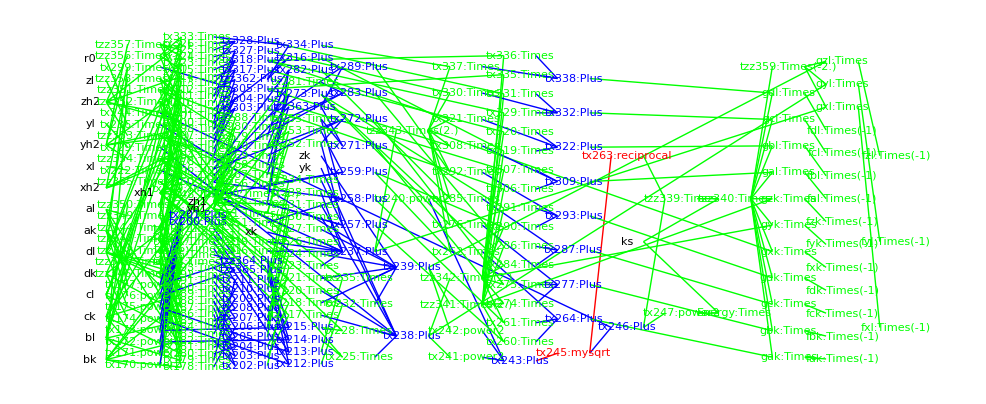

```mathematica
packGraph[staplePack]
```

# Nonbond rigid-body energy term

```mathematica
Clear[xh1,yh1,zh1,xh2,yh2,zh2];
Clear[x1,y1,z1,x2,y2,z2, evdw, eeel,nonbondRBEquation];
```

```mathematica
myrot[a_,b_,c_,d_,x_,y_,z_]:= ({{a^2+b^2+c^2+d^2, 2*b*c-2*a*d, 2*b*d+2*a*c, x}, {2*b*c+2*a*d, a^2-b^2+c^2-d^2, 2*c*d-2*a*b, y}, {2*b*d-2*a*c, 2*c*d-2*a*b, a^2-b^2-c^2+d^2, z}, {0, 0, 0, 1}})
```

```mathematica
rotk = myrot[ak,bk,ck,dk,xk,yk,zk]
```

{{ak^2+bk^2+ck^2+dk^2,2 bk ck-2 ak dk,2 ak ck+2 bk dk,xk},{2 bk ck+2 ak dk,ak^2-bk^2+ck^2-dk^2,-2 ak bk+2 ck dk,yk},{-2 ak ck+2 bk dk,-2 ak bk+2 ck dk,ak^2-bk^2-ck^2+dk^2,zk},{0,0,0,1}}

```mathematica
rotl = myrot[al,bl,cl,dl,xl,yl,zl]
```

{{al^2+bl^2+cl^2+dl^2,2 bl cl-2 al dl,2 al cl+2 bl dl,xl},{2 bl cl+2 al dl,al^2-bl^2+cl^2-dl^2,-2 al bl+2 cl dl,yl},{-2 al cl+2 bl dl,-2 al bl+2 cl dl,al^2-bl^2-cl^2+dl^2,zl},{0,0,0,1}}

```mathematica
ba = { xh1, yh1, zh1 };
bb = { xh2, yh2, zh2 };
```

```mathematica
eba = Flatten[{ba,1}];
ebb = Flatten[{bb,1}];
```

```mathematica
nonBondInputs = Flatten[{ba,bb,dA,dC,dQ1Q2}]
```

{xh1,yh1,zh1,xh2,yh2,zh2,dA,dC,dQ1Q2}

```mathematica
nonbondRBDistance = Sqrt[(rotk.eba-rotl.ebb).(rotk.eba-rotl.ebb)];
```

```mathematica
evdwEquation = (dA/nonbondRBDistance^12-dC/nonbondRBDistance^6)
```

dA/(((ak^2+bk^2+ck^2+dk^2) xh1-(al^2+bl^2+cl^2+dl^2) xh2+xk-xl+(2 bk ck-2 ak dk) yh1-(2 bl cl-2 al dl) yh2+(2 ak ck+2 bk dk) zh1-(2 al cl+2 bl dl) zh2)^2+((2 bk ck+2 ak dk) xh1-(2 bl cl+2 al dl) xh2+(ak^2-bk^2+ck^2-dk^2) yh1-(al^2-bl^2+cl^2-dl^2) yh2+yk-yl+(-2 ak bk+2 ck dk) zh1-(-2 al bl+2 cl dl) zh2)^2+((-2 ak ck+2 bk dk) xh1-(-2 al cl+2 bl dl) xh2+(-2 ak bk+2 ck dk) yh1-(-2 al bl+2 cl dl) yh2+(ak^2-bk^2-ck^2+dk^2) zh1-(al^2-bl^2-cl^2+dl^2) zh2+zk-zl)^2)^6-dC/(((ak^2+bk^2+ck^2+dk^2) xh1-(al^2+bl^2+cl^2+dl^2) xh2+xk-xl+(2 bk ck-2 ak dk) yh1-(2 bl cl-2 al dl) yh2+(2 ak ck+2 bk dk) zh1-(2 al cl+2 bl dl) zh2)^2+((2 bk ck+2 ak dk) xh1-(2 bl cl+2 al dl) xh2+(ak^2-bk^2+ck^2-dk^2) yh1-(al^2-bl^2+cl^2-dl^2) yh2+yk-yl+(-2 ak bk+2 ck dk) zh1-(-2 al bl+2 cl dl) zh2)^2+((-2 ak ck+2 bk dk) xh1-(-2 al cl+2 bl dl) xh2+(-2 ak bk+2 ck dk) yh1-(-2 al bl+2 cl dl) yh2+(ak^2-bk^2-ck^2+dk^2) zh1-(al^2-bl^2-cl^2+dl^2) zh2+zk-zl)^2)^3

```mathematica
eeelEquation = (dQ1Q2/nonbondRBDistance)
```

dQ1Q2/(√(((ak^2+bk^2+ck^2+dk^2) xh1-(al^2+bl^2+cl^2+dl^2) xh2+xk-xl+(2 bk ck-2 ak dk) yh1-(2 bl cl-2 al dl) yh2+(2 ak ck+2 bk dk) zh1-(2 al cl+2 bl dl) zh2)^2+((2 bk ck+2 ak dk) xh1-(2 bl cl+2 al dl) xh2+(ak^2-bk^2+ck^2-dk^2) yh1-(al^2-bl^2+cl^2-dl^2) yh2+yk-yl+(-2 ak bk+2 ck dk) zh1-(-2 al bl+2 cl dl) zh2)^2+((-2 ak ck+2 bk dk) xh1-(-2 al cl+2 bl dl) xh2+(-2 ak bk+2 ck dk) yh1-(-2 al bl+2 cl dl) yh2+(ak^2-bk^2-ck^2+dk^2) zh1-(al^2-bl^2-cl^2+dl^2) zh2+zk-zl)^2))

```mathematica
nonbondRBEnergyFn = evdwEquation + eeelEquation
```

dA/(((ak^2+bk^2+ck^2+dk^2) xh1-(al^2+bl^2+cl^2+dl^2) xh2+xk-xl+(2 bk ck-2 ak dk) yh1-(2 bl cl-2 al dl) yh2+(2 ak ck+2 bk dk) zh1-(2 al cl+2 bl dl) zh2)^2+((2 bk ck+2 ak dk) xh1-(2 bl cl+2 al dl) xh2+(ak^2-bk^2+ck^2-dk^2) yh1-(al^2-bl^2+cl^2-dl^2) yh2+yk-yl+(-2 ak bk+2 ck dk) zh1-(-2 al bl+2 cl dl) zh2)^2+((-2 ak ck+2 bk dk) xh1-(-2 al cl+2 bl dl) xh2+(-2 ak bk+2 ck dk) yh1-(-2 al bl+2 cl dl) yh2+(ak^2-bk^2-ck^2+dk^2) zh1-(al^2-bl^2-cl^2+dl^2) zh2+zk-zl)^2)^6-dC/(((ak^2+bk^2+ck^2+dk^2) xh1-(al^2+bl^2+cl^2+dl^2) xh2+xk-xl+(2 bk ck-2 ak dk) yh1-(2 bl cl-2 al dl) yh2+(2 ak ck+2 bk dk) zh1-(2 al cl+2 bl dl) zh2)^2+((2 bk ck+2 ak dk) xh1-(2 bl cl+2 al dl) xh2+(ak^2-bk^2+ck^2-dk^2) yh1-(al^2-bl^2+cl^2-dl^2) yh2+yk-yl+(-2 ak bk+2 ck dk) zh1-(-2 al bl+2 cl dl) zh2)^2+((-2 ak ck+2 bk dk) xh1-(-2 al cl+2 bl dl) xh2+(-2 ak bk+2 ck dk) yh1-(-2 al bl+2 cl dl) yh2+(ak^2-bk^2-ck^2+dk^2) zh1-(al^2-bl^2-cl^2+dl^2) zh2+zk-zl)^2)^3+dQ1Q2/(√(((ak^2+bk^2+ck^2+dk^2) xh1-(al^2+bl^2+cl^2+dl^2) xh2+xk-xl+(2 bk ck-2 ak dk) yh1-(2 bl cl-2 al dl) yh2+(2 ak ck+2 bk dk) zh1-(2 al cl+2 bl dl) zh2)^2+((2 bk ck+2 ak dk) xh1-(2 bl cl+2 al dl) xh2+(ak^2-bk^2+ck^2-dk^2) yh1-(al^2-bl^2+cl^2-dl^2) yh2+yk-yl+(-2 ak bk+2 ck dk) zh1-(-2 al bl+2 cl dl) zh2)^2+((-2 ak ck+2 bk dk) xh1-(-2 al cl+2 bl dl) xh2+(-2 ak bk+2 ck dk) yh1-(-2 al bl+2 cl dl) yh2+(ak^2-bk^2-ck^2+dk^2) zh1-(al^2-bl^2-cl^2+dl^2) zh2+zk-zl)^2))

```mathematica
nonbondRBVarNames = { 
{ak,a,I1,0},
{bk,b,I1,1},
{ck,c,I1,2},
{dk,d,I1,3},
{xk,x,I1,4},
{yk,y,I1,5},
{zk,z,I1,6},
{al,a,I2,0},
{bl,b,I2,1},
{cl,c,I2,2},
{dl,d,I2,3},
{xl,x,I2,4},
{yl,y,I2,5},
{zl,z,I2,6}
};
```

```mathematica
nonbondRBSetupRules = {};
AppendTo[nonbondRBSetupRules,CCode["NONBONDRB_SET_PARAMETER(I1);"]];
AppendTo[nonbondRBSetupRules,CCode["NONBONDRB_SET_PARAMETER(I2);"]];AppendTo[nonbondRBSetupRules,CCode["NONBONDRB_SET_PARAMETER(dQ1Q2);"]];AppendTo[nonbondRBSetupRules,CCode["NONBONDRB_SET_PARAMETER(dA);"]];
AppendTo[nonbondRBSetupRules,CCode["NONBONDRB_SET_PARAMETER(dC);"]];
```

```mathematica
For[i=1,i≤Length[nonbondRBVarNames],i++,
str = "NONBONDRB_SET_POSITION("<>ToString[nonbondRBVarNames[[i]][[1]]]<>","<>ToString[nonbondRBVarNames[[i]][[3]]]<>","<>ToString[nonbondRBVarNames[[i]][[4]]]<>");";
(*Print[str];*)
AppendTo[nonbondRBSetupRules,CCode[str]];
];
```

```mathematica
AppendTo[nonbondRBSetupRules, CCode["NONBONDRB_SET_POINT(xh1,pointA,getX());"]];
AppendTo[nonbondRBSetupRules, CCode["NONBONDRB_SET_POINT(yh1,pointA,getY());"]];
AppendTo[nonbondRBSetupRules, CCode["NONBONDRB_SET_POINT(zh1,pointA,getZ());"]];
AppendTo[nonbondRBSetupRules, CCode["NONBONDRB_SET_POINT(xh2,pointB,getX());"]];
AppendTo[nonbondRBSetupRules, CCode["NONBONDRB_SET_POINT(yh2,pointB,getY());"]];
AppendTo[nonbondRBSetupRules, CCode["NONBONDRB_SET_POINT(zh2,pointB,getZ());"]];
```

```mathematica
nonbondRBSetupRules//MatrixForm
```

(CCode[NONBONDRB_SET_PARAMETER(I1);]
CCode[NONBONDRB_SET_PARAMETER(I2);]
CCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]
CCode[NONBONDRB_SET_PARAMETER(dA);]
CCode[NONBONDRB_SET_PARAMETER(dC);]
CCode[NONBONDRB_SET_POSITION(ak,I1,0);]
CCode[NONBONDRB_SET_POSITION(bk,I1,1);]
CCode[NONBONDRB_SET_POSITION(ck,I1,2);]
CCode[NONBONDRB_SET_POSITION(dk,I1,3);]
CCode[NONBONDRB_SET_POSITION(xk,I1,4);]
CCode[NONBONDRB_SET_POSITION(yk,I1,5);]
CCode[NONBONDRB_SET_POSITION(zk,I1,6);]
CCode[NONBONDRB_SET_POSITION(al,I2,0);]
CCode[NONBONDRB_SET_POSITION(bl,I2,1);]
CCode[NONBONDRB_SET_POSITION(cl,I2,2);]
CCode[NONBONDRB_SET_POSITION(dl,I2,3);]
CCode[NONBONDRB_SET_POSITION(xl,I2,4);]
CCode[NONBONDRB_SET_POSITION(yl,I2,5);]
CCode[NONBONDRB_SET_POSITION(zl,I2,6);]
CCode[NONBONDRB_SET_POINT(xh1,pointA,getX());]
CCode[NONBONDRB_SET_POINT(yh1,pointA,getY());]
CCode[NONBONDRB_SET_POINT(zh1,pointA,getZ());]
CCode[NONBONDRB_SET_POINT(xh2,pointB,getX());]
CCode[NONBONDRB_SET_POINT(yh2,pointB,getY());]
CCode[NONBONDRB_SET_POINT(zh2,pointB,getZ());])

```mathematica
nonbondRBEnergyRules = {};
nonbondRBOutputs = {};
AppendTo[nonbondRBEnergyRules,Assign[Energy,nonbondRBEnergyFn]];
AppendTo[nonbondRBEnergyRules,EnergyAccumulate["NONBONDRB",Energy]];
AppendTo[nonbondRBOutputs,Energy];
```

## Append the Gradient rules

```mathematica
nonbondRBForceRules = {};
```

```mathematica
AppendGradientAndForce["NONBONDRB",nonbondRBEnergyRules,nonbondRBOutputs,nonbondRBEnergyFn,nonbondRBVarNames];
```

```mathematica
nonbondRBOutputs
```

{Energy,fak,fbk,fck,fdk,fxk,fyk,fzk,fal,fbl,fcl,fdl,fxl,fyl,fzl}

### Collect terms and convert to C code

```mathematica
nonbondRBAllRules ={
nonbondRBSetupRules,
nonbondRBEnergyRules};
```

```mathematica
nonbondRBRules = Flatten[nonbondRBAllRules];
```

```mathematica
nonbondRBRules
```

{CCode[NONBONDRB_SET_PARAMETER(I1);],CCode[NONBONDRB_SET_PARAMETER(I2);],CCode[NONBONDRB_SET_PARAMETER(dQ1Q2);],«64»,-gzl→fzl,CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 6, fzl );]}

```mathematica
nonbondRBInput = { ak,bk,ck,dk,xk,yk,zk, al,bl,cl,dl,xl,yl,zl };
```

```mathematica
AppendTo[nonbondRBOutputs,nonbondRBDeviation];
```

### Assemble the rules, the name of the energy term, the independant variable names, etc. into what passes for a structure in Mathematica (I call it a Pack)

```mathematica
nonbondRBPack0 = {
Name->"NONBONDRB",
AdditionalCDeclares->"",
DerivativeVariables->{ ak,bk,ck,dk,xk,yk,zk, al,bl,cl,dl,xl,yl,zl },
Rules->nonbondRBRules,
Input->nonbondRBInput,
Output->nonbondRBOutputs
};
```

```mathematica
writeOutputVariablesForDebugging[nonbondRBPack0];
```

Writing finite difference debug code to: _NONBONDRB_debugFiniteDifference.cc

Writing debug variable declares to: _NONBONDRB_debugEvalDeclares.cc

Writing xml output debug code to: _NONBONDRB_debugEvalSerialize.cc

Writing set variables debug code to: _NONBONDRB_debugEvalSet.cc

### Put the pedal to the metal and generate "C" code.

```mathematica
nonbondRBPack = packOptimize[nonbondRBPack0];
```

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, nonbondRBDeviation}

There were no trivial rules

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, nonbondRBDeviation}

There were no trivial rules

eliminateTrivialRules

trivialRules>> triv = {tx440 -> tx433, tx289 -> tx436, tx292 -> tx437}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, nonbondRBDeviation}

Trivial rules are being removed: tx440 -> tx433

tx289 -> tx436

tx292 -> tx437

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]

CCode[NONBONDRB_SET_PARAMETER(I2);]

CCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]

CCode[NONBONDRB_SET_PARAMETER(dA);]

CCode[NONBONDRB_SET_PARAMETER(dC);]

CCode[NONBONDRB_SET_POSITION(ak,I1,0);]

CCode[NONBONDRB_SET_POSITION(bk,I1,1);]

CCode[NONBONDRB_SET_POSITION(ck,I1,2);]

CCode[NONBONDRB_SET_POSITION(dk,I1,3);]

CCode[NONBONDRB_SET_POSITION(xk,I1,4);]

CCode[NONBONDRB_SET_POSITION(yk,I1,5);]

CCode[NONBONDRB_SET_POSITION(zk,I1,6);]

CCode[NONBONDRB_SET_POSITION(al,I2,0);]

CCode[NONBONDRB_SET_POSITION(bl,I2,1);]

CCode[NONBONDRB_SET_POSITION(cl,I2,2);]

CCode[NONBONDRB_SET_POSITION(dl,I2,3);]

CCode[NONBONDRB_SET_POSITION(xl,I2,4);]

CCode[NONBONDRB_SET_POSITION(yl,I2,5);]

CCode[NONBONDRB_SET_POSITION(zl,I2,6);]

CCode[NONBONDRB_SET_POINT(xh1,pointA,getX());]

CCode[NONBONDRB_SET_POINT(yh1,pointA,getY());]

CCode[NONBONDRB_SET_POINT(zh1,pointA,getZ());]

CCode[NONBONDRB_SET_POINT(xh2,pointB,getX());]

CCode[NONBONDRB_SET_POINT(yh2,pointB,getY());]

CCode[NONBONDRB_SET_POINT(zh2,pointB,getZ());]

power2[bk] -> tx216

power2[bl] -> tx217

power2[ck] -> tx218

power2[cl] -> tx219

power2[dk] -> tx220

power2[dl] -> tx221

power2[ak] -> tx222

power2[al] -> tx223

-2. ak bk -> tx224

-2. al bl -> tx225

-2. ak ck -> tx226

2. ak ck -> tx227

2. bk ck -> tx228

-2. al cl -> tx229

2. al cl -> tx230

2. bl cl -> tx231

-2. ak dk -> tx232

2. ak dk -> tx233

2. bk dk -> tx234

2. ck dk -> tx235

-2. al dl -> tx236

2. al dl -> tx237

2. bl dl -> tx238

2. cl dl -> tx239

-tx216 -> tx240

-tx217 -> tx241

-tx218 -> tx242

-tx219 -> tx243

-tx220 -> tx244

-tx221 -> tx245

tx216 + tx218 + tx220 + tx222 -> tx246

tx217 + tx219 + tx221 + tx223 -> tx247

tx228 + tx232 -> tx248

tx228 + tx233 -> tx249

tx226 + tx234 -> tx250

tx227 + tx234 -> tx251

tx224 + tx235 -> tx252

tx231 + tx236 -> tx253

tx231 + tx237 -> tx254

tx229 + tx238 -> tx255

tx230 + tx238 -> tx256

tx225 + tx239 -> tx257

tx220 + tx222 + tx240 + tx242 -> tx258

tx221 + tx223 + tx241 + tx243 -> tx259

tx218 + tx222 + tx240 + tx244 -> tx260

tx219 + tx223 + tx241 + tx245 -> tx261

tx246 xh1 -> tx262

tx249 xh1 -> tx263

tx250 xh1 -> tx264

-(tx247 xh2) -> tx265

-(tx254 xh2) -> tx266

-(tx255 xh2) -> tx267

-xl -> tx268

tx248 yh1 -> tx269

tx252 yh1 -> tx270

tx260 yh1 -> tx271

-(tx253 yh2) -> tx272

-(tx257 yh2) -> tx273

-(tx261 yh2) -> tx274

-yl -> tx275

tx251 zh1 -> tx276

tx252 zh1 -> tx277

tx258 zh1 -> tx278

-(tx256 zh2) -> tx279

-(tx257 zh2) -> tx280

-(tx259 zh2) -> tx281

-zl -> tx282

tx262 + tx265 + tx268 + tx269 + tx272 + tx276 + tx279 + xk -> tx283

tx263 + tx266 + tx271 + tx274 + tx275 + tx277 + tx280 + yk -> tx284

tx264 + tx267 + tx270 + tx273 + tx278 + tx281 + tx282 + zk -> tx285

power2[tx283] -> tx286

power2[tx284] -> tx287

power2[tx285] -> tx288

tx286 + tx287 + tx288 -> tx289

powern2[tx289] -> tx439

reciprocal[tx289] -> tx440

tx439 tx440 -> tx431

power2[tx431] -> tx290

power2[tx440] -> tx432

tx440 -> tx433

tx432 tx433 -> tx291

mysqrt[tx289] -> tx434

reciprocal[tx434] -> tx292

dA tx290 -> tx293

-(dC tx291) -> tx294

dQ1Q2 tx292 -> tx295

tx293 + tx294 + tx295 -> Energy

CCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

2. ak xh1 -> tx296

-2. ck xh1 -> tx297

2. dk xh1 -> tx298

2. ak yh1 -> tx299

-2. bk yh1 -> tx300

-2. dk yh1 -> tx301

2. ak zh1 -> tx302

-2. bk zh1 -> tx303

2. ck zh1 -> tx304

tx297 + tx300 + tx302 -> tx305

tx298 + tx299 + tx303 -> tx306

tx296 + tx301 + tx304 -> tx307

2. tx285 tx305 -> tx308

2. tx284 tx306 -> tx309

2. tx283 tx307 -> tx310

power2[tx439] -> tx435

tx431 tx435 -> tx311

power2[tx432] -> tx312

tx289 -> tx436

tx292 -> tx437

reciprocal[tx436] -> tx438

tx437 tx438 -> tx313

tx308 + tx309 + tx310 -> tx314

-6. dA tx311 tx314 -> tx315

3 dC tx312 tx314 -> tx316

-0.5 dQ1Q2 tx313 tx314 -> tx317

tx315 + tx316 + tx317 -> gak

-gak -> fak

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 0, fak );]

2. bk xh1 -> tx318

2. ck xh1 -> tx319

-2. ak yh1 -> tx320

2. ck yh1 -> tx321

-2. ak zh1 -> tx322

2. dk zh1 -> tx323

tx298 + tx303 + tx320 -> tx324

tx300 + tx319 + tx322 -> tx325

tx318 + tx321 + tx323 -> tx326

2. tx285 tx324 -> tx327

2. tx284 tx325 -> tx328

2. tx283 tx326 -> tx329

tx327 + tx328 + tx329 -> tx330

-6. dA tx311 tx330 -> tx331

3 dC tx312 tx330 -> tx332

-0.5 dQ1Q2 tx313 tx330 -> tx333

tx331 + tx332 + tx333 -> gbk

-gbk -> fbk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 1, fbk );]

-2. ak xh1 -> tx334

2. bk yh1 -> tx335

2. dk yh1 -> tx336

-2. ck zh1 -> tx337

tx302 + tx319 + tx335 -> tx338

tx334 + tx336 + tx337 -> tx339

2. tx284 tx326 -> tx340

2. tx283 tx338 -> tx341

2. tx285 tx339 -> tx342

tx340 + tx341 + tx342 -> tx343

-6. dA tx311 tx343 -> tx344

3 dC tx312 tx343 -> tx345

-0.5 dQ1Q2 tx313 tx343 -> tx346

tx344 + tx345 + tx346 -> gck

-gck -> fck

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 2, fck );]

2. bk zh1 -> tx347

tx298 + tx320 + tx347 -> tx348

2. tx284 tx307 -> tx349

2. tx285 tx326 -> tx350

2. tx283 tx348 -> tx351

tx349 + tx350 + tx351 -> tx352

-6. dA tx311 tx352 -> tx353

3 dC tx312 tx352 -> tx354

-0.5 dQ1Q2 tx313 tx352 -> tx355

tx353 + tx354 + tx355 -> gdk

-gdk -> fdk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 3, fdk );]

-12. dA tx283 tx311 -> tx356

6. dC tx283 tx312 -> tx357

-(dQ1Q2 tx283 tx313) -> tx358

tx356 + tx357 + tx358 -> gxk

-gxk -> fxk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 4, fxk );]

-12. dA tx284 tx311 -> tx359

6. dC tx284 tx312 -> tx360

-(dQ1Q2 tx284 tx313) -> tx361

tx359 + tx360 + tx361 -> gyk

-gyk -> fyk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 5, fyk );]

-12. dA tx285 tx311 -> tx362

6. dC tx285 tx312 -> tx363

-(dQ1Q2 tx285 tx313) -> tx364

tx362 + tx363 + tx364 -> gzk

-gzk -> fzk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 6, fzk );]

-2. al xh2 -> tx365

2. cl xh2 -> tx366

-2. dl xh2 -> tx367

-2. al yh2 -> tx368

2. bl yh2 -> tx369

2. dl yh2 -> tx370

-2. al zh2 -> tx371

2. bl zh2 -> tx372

-2. cl zh2 -> tx373

tx366 + tx369 + tx371 -> tx374

tx367 + tx368 + tx372 -> tx375

tx365 + tx370 + tx373 -> tx376

2. tx285 tx374 -> tx377

2. tx284 tx375 -> tx378

2. tx283 tx376 -> tx379

tx377 + tx378 + tx379 -> tx380

-6. dA tx311 tx380 -> tx381

3 dC tx312 tx380 -> tx382

-0.5 dQ1Q2 tx313 tx380 -> tx383

tx381 + tx382 + tx383 -> gal

-gal -> fal

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 0, fal );]

-2. bl xh2 -> tx384

-2. cl xh2 -> tx385

2. al yh2 -> tx386

-2. cl yh2 -> tx387

2. al zh2 -> tx388

-2. dl zh2 -> tx389

tx367 + tx372 + tx386 -> tx390

tx369 + tx385 + tx388 -> tx391

tx384 + tx387 + tx389 -> tx392

2. tx285 tx390 -> tx393

2. tx284 tx391 -> tx394

2. tx283 tx392 -> tx395

tx393 + tx394 + tx395 -> tx396

-6. dA tx311 tx396 -> tx397

3 dC tx312 tx396 -> tx398

-0.5 dQ1Q2 tx313 tx396 -> tx399

tx397 + tx398 + tx399 -> gbl

-gbl -> fbl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 1, fbl );]

2. al xh2 -> tx400

-2. bl yh2 -> tx401

-2. dl yh2 -> tx402

2. cl zh2 -> tx403

tx371 + tx385 + tx401 -> tx404

tx400 + tx402 + tx403 -> tx405

2. tx284 tx392 -> tx406

2. tx283 tx404 -> tx407

2. tx285 tx405 -> tx408

tx406 + tx407 + tx408 -> tx409

-6. dA tx311 tx409 -> tx410

3 dC tx312 tx409 -> tx411

-0.5 dQ1Q2 tx313 tx409 -> tx412

tx410 + tx411 + tx412 -> gcl

-gcl -> fcl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 2, fcl );]

-2. bl zh2 -> tx413

tx367 + tx386 + tx413 -> tx414

2. tx284 tx376 -> tx415

2. tx285 tx392 -> tx416

2. tx283 tx414 -> tx417

tx415 + tx416 + tx417 -> tx418

-6. dA tx311 tx418 -> tx419

3 dC tx312 tx418 -> tx420

-0.5 dQ1Q2 tx313 tx418 -> tx421

tx419 + tx420 + tx421 -> gdl

-gdl -> fdl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 3, fdl );]

12. dA tx283 tx311 -> tx422

-6. dC tx283 tx312 -> tx423

dQ1Q2 tx283 tx313 -> tx424

tx422 + tx423 + tx424 -> gxl

-gxl -> fxl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 4, fxl );]

12. dA tx284 tx311 -> tx425

-6. dC tx284 tx312 -> tx426

dQ1Q2 tx284 tx313 -> tx427

tx425 + tx426 + tx427 -> gyl

-gyl -> fyl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 5, fyl );]

12. dA tx285 tx311 -> tx428

-6. dC tx285 tx312 -> tx429

dQ1Q2 tx285 tx313 -> tx430

tx428 + tx429 + tx430 -> gzl

-gzl -> fzl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 6, fzl );]

trivialRules>> triv = {tx440 -> tx433, tx289 -> tx436, tx292 -> tx437}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, nonbondRBDeviation}

Trivial rules are being removed: tx440 -> tx433

tx289 -> tx436

tx292 -> tx437

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]

CCode[NONBONDRB_SET_PARAMETER(I2);]

CCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]

CCode[NONBONDRB_SET_PARAMETER(dA);]

CCode[NONBONDRB_SET_PARAMETER(dC);]

CCode[NONBONDRB_SET_POSITION(ak,I1,0);]

CCode[NONBONDRB_SET_POSITION(bk,I1,1);]

CCode[NONBONDRB_SET_POSITION(ck,I1,2);]

CCode[NONBONDRB_SET_POSITION(dk,I1,3);]

CCode[NONBONDRB_SET_POSITION(xk,I1,4);]

CCode[NONBONDRB_SET_POSITION(yk,I1,5);]

CCode[NONBONDRB_SET_POSITION(zk,I1,6);]

CCode[NONBONDRB_SET_POSITION(al,I2,0);]

CCode[NONBONDRB_SET_POSITION(bl,I2,1);]

CCode[NONBONDRB_SET_POSITION(cl,I2,2);]

CCode[NONBONDRB_SET_POSITION(dl,I2,3);]

CCode[NONBONDRB_SET_POSITION(xl,I2,4);]

CCode[NONBONDRB_SET_POSITION(yl,I2,5);]

CCode[NONBONDRB_SET_POSITION(zl,I2,6);]

CCode[NONBONDRB_SET_POINT(xh1,pointA,getX());]

CCode[NONBONDRB_SET_POINT(yh1,pointA,getY());]

CCode[NONBONDRB_SET_POINT(zh1,pointA,getZ());]

CCode[NONBONDRB_SET_POINT(xh2,pointB,getX());]

CCode[NONBONDRB_SET_POINT(yh2,pointB,getY());]

CCode[NONBONDRB_SET_POINT(zh2,pointB,getZ());]

power2[bk] -> tx216

power2[bl] -> tx217

power2[ck] -> tx218

power2[cl] -> tx219

power2[dk] -> tx220

power2[dl] -> tx221

power2[ak] -> tx222

power2[al] -> tx223

-2. ak -> tzz452

bk tzz452 -> tx224

-2. al -> tzz451

bl tzz451 -> tx225

ck tzz452 -> tx226

2. ck -> tzz454

ak tzz454 -> tx227

bk tzz454 -> tx228

cl tzz451 -> tx229

2. cl -> tzz453

al tzz453 -> tx230

bl tzz453 -> tx231

dk tzz452 -> tx232

2. dk -> tzz450

ak tzz450 -> tx233

bk tzz450 -> tx234

ck tzz450 -> tx235

dl tzz451 -> tx236

2. al -> tzz455

dl tzz455 -> tx237

2. bl -> tzz458

dl tzz458 -> tx238

dl tzz453 -> tx239

-tx216 -> tx240

-tx217 -> tx241

-tx218 -> tx242

-tx219 -> tx243

-tx220 -> tx244

-tx221 -> tx245

tx216 + tx218 + tx220 + tx222 -> tx246

tx217 + tx219 + tx221 + tx223 -> tx247

tx228 + tx232 -> tx248

tx228 + tx233 -> tx249

tx226 + tx234 -> tx250

tx227 + tx234 -> tx251

tx224 + tx235 -> tx252

tx231 + tx236 -> tx253

tx231 + tx237 -> tx254

tx229 + tx238 -> tx255

tx230 + tx238 -> tx256

tx225 + tx239 -> tx257

tx220 + tx222 + tx240 + tx242 -> tx258

tx221 + tx223 + tx241 + tx243 -> tx259

tx218 + tx222 + tx240 + tx244 -> tx260

tx219 + tx223 + tx241 + tx245 -> tx261

tx246 xh1 -> tx262

tx249 xh1 -> tx263

tx250 xh1 -> tx264

-xh2 -> tzz463

tx247 tzz463 -> tx265

tx254 tzz463 -> tx266

tx255 tzz463 -> tx267

-xl -> tx268

tx248 yh1 -> tx269

tx252 yh1 -> tx270

tx260 yh1 -> tx271

-yh2 -> tzz462

tx253 tzz462 -> tx272

tx257 tzz462 -> tx273

tx261 tzz462 -> tx274

-yl -> tx275

tx251 zh1 -> tx276

tx252 zh1 -> tx277

tx258 zh1 -> tx278

-zh2 -> tzz461

tx256 tzz461 -> tx279

tx257 tzz461 -> tx280

tx259 tzz461 -> tx281

-zl -> tx282

tx262 + tx265 + tx268 + tx269 + tx272 + tx276 + tx279 + xk -> tx283

tx263 + tx266 + tx271 + tx274 + tx275 + tx277 + tx280 + yk -> tx284

tx264 + tx267 + tx270 + tx273 + tx278 + tx281 + tx282 + zk -> tx285

power2[tx283] -> tx286

power2[tx284] -> tx287

power2[tx285] -> tx288

tx286 + tx287 + tx288 -> tx289

power2[reciprocal[tx289]] -> tx439

reciprocal[tx289] -> tx440

tx439 tx440 -> tx431

power2[tx431] -> tx290

power2[tx440] -> tx432

tx440 -> tx433

tx432 tx433 -> tx291

mysqrt[tx289] -> tx434

reciprocal[tx434] -> tx292

dA tx290 -> tx293

-(dC tx291) -> tx294

dQ1Q2 tx292 -> tx295

tx293 + tx294 + tx295 -> Energy

CCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

2. ak -> tzz460

tzz460 xh1 -> tx296

-2. ck xh1 -> tx297

tzz450 xh1 -> tx298

tzz460 yh1 -> tx299

-2. yh1 -> tzz471

bk tzz471 -> tx300

dk tzz471 -> tx301

tzz460 zh1 -> tx302

-2. zh1 -> tzz470

bk tzz470 -> tx303

tzz454 zh1 -> tx304

tx297 + tx300 + tx302 -> tx305

tx298 + tx299 + tx303 -> tx306

tx296 + tx301 + tx304 -> tx307

2. tx285 -> tzz445

tx305 tzz445 -> tx308

2. tx284 -> tzz446

tx306 tzz446 -> tx309

2. tx283 -> tzz447

tx307 tzz447 -> tx310

power2[tx439] -> tx435

tx431 tx435 -> tx311

power2[tx432] -> tx312

tx289 -> tx436

tx292 -> tx437

reciprocal[tx436] -> tx438

tx437 tx438 -> tx313

tx308 + tx309 + tx310 -> tx314

dA tx311 -> tzz443

-6. tzz443 -> tzz449

tx314 tzz449 -> tx315

dC tx312 -> tzz442

3 tzz442 -> tzz444

tx314 tzz444 -> tx316

dQ1Q2 tx313 -> tzz441

-0.5 tzz441 -> tzz448

tx314 tzz448 -> tx317

tx315 + tx316 + tx317 -> gak

-gak -> fak

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 0, fak );]

2. bk -> tzz459

tzz459 xh1 -> tx318

tzz454 xh1 -> tx319

tzz452 yh1 -> tx320

tzz454 yh1 -> tx321

tzz452 zh1 -> tx322

tzz450 zh1 -> tx323

tx298 + tx303 + tx320 -> tx324

tx300 + tx319 + tx322 -> tx325

tx318 + tx321 + tx323 -> tx326

tx324 tzz445 -> tx327

tx325 tzz446 -> tx328

tx326 tzz447 -> tx329

tx327 + tx328 + tx329 -> tx330

tx330 tzz449 -> tx331

tx330 tzz444 -> tx332

tx330 tzz448 -> tx333

tx331 + tx332 + tx333 -> gbk

-gbk -> fbk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 1, fbk );]

tzz452 xh1 -> tx334

tzz459 yh1 -> tx335

tzz450 yh1 -> tx336

ck tzz470 -> tx337

tx302 + tx319 + tx335 -> tx338

tx334 + tx336 + tx337 -> tx339

tx326 tzz446 -> tx340

tx338 tzz447 -> tx341

tx339 tzz445 -> tx342

tx340 + tx341 + tx342 -> tx343

tx343 tzz449 -> tx344

tx343 tzz444 -> tx345

tx343 tzz448 -> tx346

tx344 + tx345 + tx346 -> gck

-gck -> fck

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 2, fck );]

tzz459 zh1 -> tx347

tx298 + tx320 + tx347 -> tx348

tx307 tzz446 -> tx349

tx326 tzz445 -> tx350

tx348 tzz447 -> tx351

tx349 + tx350 + tx351 -> tx352

tx352 tzz449 -> tx353

tx352 tzz444 -> tx354

tx352 tzz448 -> tx355

tx353 + tx354 + tx355 -> gdk

-gdk -> fdk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 3, fdk );]

-12. tzz443 -> tzz469

tx283 tzz469 -> tx356

6. tzz442 -> tzz457

tx283 tzz457 -> tx357

-tzz441 -> tzz464

tx283 tzz464 -> tx358

tx356 + tx357 + tx358 -> gxk

-gxk -> fxk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 4, fxk );]

tx284 tzz469 -> tx359

tx284 tzz457 -> tx360

tx284 tzz464 -> tx361

tx359 + tx360 + tx361 -> gyk

-gyk -> fyk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 5, fyk );]

tx285 tzz469 -> tx362

tx285 tzz457 -> tx363

tx285 tzz464 -> tx364

tx362 + tx363 + tx364 -> gzk

-gzk -> fzk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 6, fzk );]

tzz451 xh2 -> tx365

tzz453 xh2 -> tx366

-2. xh2 -> tzz467

dl tzz467 -> tx367

tzz451 yh2 -> tx368

tzz458 yh2 -> tx369

2. dl yh2 -> tx370

tzz451 zh2 -> tx371

tzz458 zh2 -> tx372

-2. zh2 -> tzz465

cl tzz465 -> tx373

tx366 + tx369 + tx371 -> tx374

tx367 + tx368 + tx372 -> tx375

tx365 + tx370 + tx373 -> tx376

tx374 tzz445 -> tx377

tx375 tzz446 -> tx378

tx376 tzz447 -> tx379

tx377 + tx378 + tx379 -> tx380

tx380 tzz449 -> tx381

tx380 tzz444 -> tx382

tx380 tzz448 -> tx383

tx381 + tx382 + tx383 -> gal

-gal -> fal

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 0, fal );]

bl tzz467 -> tx384

cl tzz467 -> tx385

tzz455 yh2 -> tx386

-2. yh2 -> tzz466

cl tzz466 -> tx387

tzz455 zh2 -> tx388

dl tzz465 -> tx389

tx367 + tx372 + tx386 -> tx390

tx369 + tx385 + tx388 -> tx391

tx384 + tx387 + tx389 -> tx392

tx390 tzz445 -> tx393

tx391 tzz446 -> tx394

tx392 tzz447 -> tx395

tx393 + tx394 + tx395 -> tx396

tx396 tzz449 -> tx397

tx396 tzz444 -> tx398

tx396 tzz448 -> tx399

tx397 + tx398 + tx399 -> gbl

-gbl -> fbl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 1, fbl );]

tzz455 xh2 -> tx400

bl tzz466 -> tx401

dl tzz466 -> tx402

tzz453 zh2 -> tx403

tx371 + tx385 + tx401 -> tx404

tx400 + tx402 + tx403 -> tx405

tx392 tzz446 -> tx406

tx404 tzz447 -> tx407

tx405 tzz445 -> tx408

tx406 + tx407 + tx408 -> tx409

tx409 tzz449 -> tx410

tx409 tzz444 -> tx411

tx409 tzz448 -> tx412

tx410 + tx411 + tx412 -> gcl

-gcl -> fcl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 2, fcl );]

bl tzz465 -> tx413

tx367 + tx386 + tx413 -> tx414

tx376 tzz446 -> tx415

tx392 tzz445 -> tx416

tx414 tzz447 -> tx417

tx415 + tx416 + tx417 -> tx418

tx418 tzz449 -> tx419

tx418 tzz444 -> tx420

tx418 tzz448 -> tx421

tx419 + tx420 + tx421 -> gdl

-gdl -> fdl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 3, fdl );]

12. tzz443 -> tzz456

tx283 tzz456 -> tx422

-6. tzz442 -> tzz468

tx283 tzz468 -> tx423

tx283 tzz441 -> tx424

tx422 + tx423 + tx424 -> gxl

-gxl -> fxl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 4, fxl );]

tx284 tzz456 -> tx425

tx284 tzz468 -> tx426

tx284 tzz441 -> tx427

tx425 + tx426 + tx427 -> gyl

-gyl -> fyl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 5, fyl );]

tx285 tzz456 -> tx428

tx285 tzz468 -> tx429

tx285 tzz441 -> tx430

tx428 + tx429 + tx430 -> gzl

-gzl -> fzl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 6, fzl );]

eliminateTrivialRules

trivialRules>> triv = {tx472 -> tx440, tx440 -> tx433, tx289 -> tx436, tx292 -> tx437}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, nonbondRBDeviation}

Trivial rules are being removed: tx472 -> tx440

tx440 -> tx433

tx289 -> tx436

tx292 -> tx437

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]

CCode[NONBONDRB_SET_PARAMETER(I2);]

CCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]

CCode[NONBONDRB_SET_PARAMETER(dA);]

CCode[NONBONDRB_SET_PARAMETER(dC);]

CCode[NONBONDRB_SET_POSITION(ak,I1,0);]

CCode[NONBONDRB_SET_POSITION(bk,I1,1);]

CCode[NONBONDRB_SET_POSITION(ck,I1,2);]

CCode[NONBONDRB_SET_POSITION(dk,I1,3);]

CCode[NONBONDRB_SET_POSITION(xk,I1,4);]

CCode[NONBONDRB_SET_POSITION(yk,I1,5);]

CCode[NONBONDRB_SET_POSITION(zk,I1,6);]

CCode[NONBONDRB_SET_POSITION(al,I2,0);]

CCode[NONBONDRB_SET_POSITION(bl,I2,1);]

CCode[NONBONDRB_SET_POSITION(cl,I2,2);]

CCode[NONBONDRB_SET_POSITION(dl,I2,3);]

CCode[NONBONDRB_SET_POSITION(xl,I2,4);]

CCode[NONBONDRB_SET_POSITION(yl,I2,5);]

CCode[NONBONDRB_SET_POSITION(zl,I2,6);]

CCode[NONBONDRB_SET_POINT(xh1,pointA,getX());]

CCode[NONBONDRB_SET_POINT(yh1,pointA,getY());]

CCode[NONBONDRB_SET_POINT(zh1,pointA,getZ());]

CCode[NONBONDRB_SET_POINT(xh2,pointB,getX());]

CCode[NONBONDRB_SET_POINT(yh2,pointB,getY());]

CCode[NONBONDRB_SET_POINT(zh2,pointB,getZ());]

power2[bk] -> tx216

power2[bl] -> tx217

power2[ck] -> tx218

power2[cl] -> tx219

power2[dk] -> tx220

power2[dl] -> tx221

power2[ak] -> tx222

power2[al] -> tx223

-2. ak -> tzz452

bk tzz452 -> tx224

-2. al -> tzz451

bl tzz451 -> tx225

ck tzz452 -> tx226

2. ck -> tzz454

ak tzz454 -> tx227

bk tzz454 -> tx228

cl tzz451 -> tx229

2. cl -> tzz453

al tzz453 -> tx230

bl tzz453 -> tx231

dk tzz452 -> tx232

2. dk -> tzz450

ak tzz450 -> tx233

bk tzz450 -> tx234

ck tzz450 -> tx235

dl tzz451 -> tx236

2. al -> tzz455

dl tzz455 -> tx237

2. bl -> tzz458

dl tzz458 -> tx238

dl tzz453 -> tx239

-tx216 -> tx240

-tx217 -> tx241

-tx218 -> tx242

-tx219 -> tx243

-tx220 -> tx244

-tx221 -> tx245

tx216 + tx218 + tx220 + tx222 -> tx246

tx217 + tx219 + tx221 + tx223 -> tx247

tx228 + tx232 -> tx248

tx228 + tx233 -> tx249

tx226 + tx234 -> tx250

tx227 + tx234 -> tx251

tx224 + tx235 -> tx252

tx231 + tx236 -> tx253

tx231 + tx237 -> tx254

tx229 + tx238 -> tx255

tx230 + tx238 -> tx256

tx225 + tx239 -> tx257

tx220 + tx222 + tx240 + tx242 -> tx258

tx221 + tx223 + tx241 + tx243 -> tx259

tx218 + tx222 + tx240 + tx244 -> tx260

tx219 + tx223 + tx241 + tx245 -> tx261

tx246 xh1 -> tx262

tx249 xh1 -> tx263

tx250 xh1 -> tx264

-xh2 -> tzz463

tx247 tzz463 -> tx265

tx254 tzz463 -> tx266

tx255 tzz463 -> tx267

-xl -> tx268

tx248 yh1 -> tx269

tx252 yh1 -> tx270

tx260 yh1 -> tx271

-yh2 -> tzz462

tx253 tzz462 -> tx272

tx257 tzz462 -> tx273

tx261 tzz462 -> tx274

-yl -> tx275

tx251 zh1 -> tx276

tx252 zh1 -> tx277

tx258 zh1 -> tx278

-zh2 -> tzz461

tx256 tzz461 -> tx279

tx257 tzz461 -> tx280

tx259 tzz461 -> tx281

-zl -> tx282

tx262 + tx265 + tx268 + tx269 + tx272 + tx276 + tx279 + xk -> tx283

tx263 + tx266 + tx271 + tx274 + tx275 + tx277 + tx280 + yk -> tx284

tx264 + tx267 + tx270 + tx273 + tx278 + tx281 + tx282 + zk -> tx285

power2[tx283] -> tx286

power2[tx284] -> tx287

power2[tx285] -> tx288

tx286 + tx287 + tx288 -> tx289

reciprocal[tx289] -> tx472

power2[tx472] -> tx439

tx472 -> tx440

tx439 tx440 -> tx431

power2[tx431] -> tx290

power2[tx440] -> tx432

tx440 -> tx433

tx432 tx433 -> tx291

mysqrt[tx289] -> tx434

reciprocal[tx434] -> tx292

dA tx290 -> tx293

-(dC tx291) -> tx294

dQ1Q2 tx292 -> tx295

tx293 + tx294 + tx295 -> Energy

CCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

2. ak -> tzz460

tzz460 xh1 -> tx296

-2. ck xh1 -> tx297

tzz450 xh1 -> tx298

tzz460 yh1 -> tx299

-2. yh1 -> tzz471

bk tzz471 -> tx300

dk tzz471 -> tx301

tzz460 zh1 -> tx302

-2. zh1 -> tzz470

bk tzz470 -> tx303

tzz454 zh1 -> tx304

tx297 + tx300 + tx302 -> tx305

tx298 + tx299 + tx303 -> tx306

tx296 + tx301 + tx304 -> tx307

2. tx285 -> tzz445

tx305 tzz445 -> tx308

2. tx284 -> tzz446

tx306 tzz446 -> tx309

2. tx283 -> tzz447

tx307 tzz447 -> tx310

power2[tx439] -> tx435

tx431 tx435 -> tx311

power2[tx432] -> tx312

tx289 -> tx436

tx292 -> tx437

reciprocal[tx436] -> tx438

tx437 tx438 -> tx313

tx308 + tx309 + tx310 -> tx314

dA tx311 -> tzz443

-6. tzz443 -> tzz449

tx314 tzz449 -> tx315

dC tx312 -> tzz442

3 tzz442 -> tzz444

tx314 tzz444 -> tx316

dQ1Q2 tx313 -> tzz441

-0.5 tzz441 -> tzz448

tx314 tzz448 -> tx317

tx315 + tx316 + tx317 -> gak

-gak -> fak

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 0, fak );]

2. bk -> tzz459

tzz459 xh1 -> tx318

tzz454 xh1 -> tx319

tzz452 yh1 -> tx320

tzz454 yh1 -> tx321

tzz452 zh1 -> tx322

tzz450 zh1 -> tx323

tx298 + tx303 + tx320 -> tx324

tx300 + tx319 + tx322 -> tx325

tx318 + tx321 + tx323 -> tx326

tx324 tzz445 -> tx327

tx325 tzz446 -> tx328

tx326 tzz447 -> tx329

tx327 + tx328 + tx329 -> tx330

tx330 tzz449 -> tx331

tx330 tzz444 -> tx332

tx330 tzz448 -> tx333

tx331 + tx332 + tx333 -> gbk

-gbk -> fbk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 1, fbk );]

tzz452 xh1 -> tx334

tzz459 yh1 -> tx335

tzz450 yh1 -> tx336

ck tzz470 -> tx337

tx302 + tx319 + tx335 -> tx338

tx334 + tx336 + tx337 -> tx339

tx326 tzz446 -> tx340

tx338 tzz447 -> tx341

tx339 tzz445 -> tx342

tx340 + tx341 + tx342 -> tx343

tx343 tzz449 -> tx344

tx343 tzz444 -> tx345

tx343 tzz448 -> tx346

tx344 + tx345 + tx346 -> gck

-gck -> fck

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 2, fck );]

tzz459 zh1 -> tx347

tx298 + tx320 + tx347 -> tx348

tx307 tzz446 -> tx349

tx326 tzz445 -> tx350

tx348 tzz447 -> tx351

tx349 + tx350 + tx351 -> tx352

tx352 tzz449 -> tx353

tx352 tzz444 -> tx354

tx352 tzz448 -> tx355

tx353 + tx354 + tx355 -> gdk

-gdk -> fdk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 3, fdk );]

-12. tzz443 -> tzz469

tx283 tzz469 -> tx356

6. tzz442 -> tzz457

tx283 tzz457 -> tx357

-tzz441 -> tzz464

tx283 tzz464 -> tx358

tx356 + tx357 + tx358 -> gxk

-gxk -> fxk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 4, fxk );]

tx284 tzz469 -> tx359

tx284 tzz457 -> tx360

tx284 tzz464 -> tx361

tx359 + tx360 + tx361 -> gyk

-gyk -> fyk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 5, fyk );]

tx285 tzz469 -> tx362

tx285 tzz457 -> tx363

tx285 tzz464 -> tx364

tx362 + tx363 + tx364 -> gzk

-gzk -> fzk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 6, fzk );]

tzz451 xh2 -> tx365

tzz453 xh2 -> tx366

-2. xh2 -> tzz467

dl tzz467 -> tx367

tzz451 yh2 -> tx368

tzz458 yh2 -> tx369

2. dl yh2 -> tx370

tzz451 zh2 -> tx371

tzz458 zh2 -> tx372

-2. zh2 -> tzz465

cl tzz465 -> tx373

tx366 + tx369 + tx371 -> tx374

tx367 + tx368 + tx372 -> tx375

tx365 + tx370 + tx373 -> tx376

tx374 tzz445 -> tx377

tx375 tzz446 -> tx378

tx376 tzz447 -> tx379

tx377 + tx378 + tx379 -> tx380

tx380 tzz449 -> tx381

tx380 tzz444 -> tx382

tx380 tzz448 -> tx383

tx381 + tx382 + tx383 -> gal

-gal -> fal

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 0, fal );]

bl tzz467 -> tx384

cl tzz467 -> tx385

tzz455 yh2 -> tx386

-2. yh2 -> tzz466

cl tzz466 -> tx387

tzz455 zh2 -> tx388

dl tzz465 -> tx389

tx367 + tx372 + tx386 -> tx390

tx369 + tx385 + tx388 -> tx391

tx384 + tx387 + tx389 -> tx392

tx390 tzz445 -> tx393

tx391 tzz446 -> tx394

tx392 tzz447 -> tx395

tx393 + tx394 + tx395 -> tx396

tx396 tzz449 -> tx397

tx396 tzz444 -> tx398

tx396 tzz448 -> tx399

tx397 + tx398 + tx399 -> gbl

-gbl -> fbl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 1, fbl );]

tzz455 xh2 -> tx400

bl tzz466 -> tx401

dl tzz466 -> tx402

tzz453 zh2 -> tx403

tx371 + tx385 + tx401 -> tx404

tx400 + tx402 + tx403 -> tx405

tx392 tzz446 -> tx406

tx404 tzz447 -> tx407

tx405 tzz445 -> tx408

tx406 + tx407 + tx408 -> tx409

tx409 tzz449 -> tx410

tx409 tzz444 -> tx411

tx409 tzz448 -> tx412

tx410 + tx411 + tx412 -> gcl

-gcl -> fcl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 2, fcl );]

bl tzz465 -> tx413

tx367 + tx386 + tx413 -> tx414

tx376 tzz446 -> tx415

tx392 tzz445 -> tx416

tx414 tzz447 -> tx417

tx415 + tx416 + tx417 -> tx418

tx418 tzz449 -> tx419

tx418 tzz444 -> tx420

tx418 tzz448 -> tx421

tx419 + tx420 + tx421 -> gdl

-gdl -> fdl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 3, fdl );]

12. tzz443 -> tzz456

tx283 tzz456 -> tx422

-6. tzz442 -> tzz468

tx283 tzz468 -> tx423

tx283 tzz441 -> tx424

tx422 + tx423 + tx424 -> gxl

-gxl -> fxl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 4, fxl );]

tx284 tzz456 -> tx425

tx284 tzz468 -> tx426

tx284 tzz441 -> tx427

tx425 + tx426 + tx427 -> gyl

-gyl -> fyl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 5, fyl );]

tx285 tzz456 -> tx428

tx285 tzz468 -> tx429

tx285 tzz441 -> tx430

tx428 + tx429 + tx430 -> gzl

-gzl -> fzl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 6, fzl );]

trivialRules>> triv = {tx472 -> tx440, tx440 -> tx433, tx289 -> tx436, tx292 -> tx437}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, nonbondRBDeviation}

Trivial rules are being removed: tx472 -> tx440

tx440 -> tx433

tx289 -> tx436

tx292 -> tx437

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]

CCode[NONBONDRB_SET_PARAMETER(I2);]

CCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]

CCode[NONBONDRB_SET_PARAMETER(dA);]

CCode[NONBONDRB_SET_PARAMETER(dC);]

CCode[NONBONDRB_SET_POSITION(ak,I1,0);]

CCode[NONBONDRB_SET_POSITION(bk,I1,1);]

CCode[NONBONDRB_SET_POSITION(ck,I1,2);]

CCode[NONBONDRB_SET_POSITION(dk,I1,3);]

CCode[NONBONDRB_SET_POSITION(xk,I1,4);]

CCode[NONBONDRB_SET_POSITION(yk,I1,5);]

CCode[NONBONDRB_SET_POSITION(zk,I1,6);]

CCode[NONBONDRB_SET_POSITION(al,I2,0);]

CCode[NONBONDRB_SET_POSITION(bl,I2,1);]

CCode[NONBONDRB_SET_POSITION(cl,I2,2);]

CCode[NONBONDRB_SET_POSITION(dl,I2,3);]

CCode[NONBONDRB_SET_POSITION(xl,I2,4);]

CCode[NONBONDRB_SET_POSITION(yl,I2,5);]

CCode[NONBONDRB_SET_POSITION(zl,I2,6);]

CCode[NONBONDRB_SET_POINT(xh1,pointA,getX());]

CCode[NONBONDRB_SET_POINT(yh1,pointA,getY());]

CCode[NONBONDRB_SET_POINT(zh1,pointA,getZ());]

CCode[NONBONDRB_SET_POINT(xh2,pointB,getX());]

CCode[NONBONDRB_SET_POINT(yh2,pointB,getY());]

CCode[NONBONDRB_SET_POINT(zh2,pointB,getZ());]

power2[bk] -> tx216

power2[bl] -> tx217

power2[ck] -> tx218

power2[cl] -> tx219

power2[dk] -> tx220

power2[dl] -> tx221

power2[ak] -> tx222

power2[al] -> tx223

-2. ak -> tzz452

bk tzz452 -> tx224

-2. al -> tzz451

bl tzz451 -> tx225

ck tzz452 -> tx226

2. ck -> tzz454

ak tzz454 -> tx227

bk tzz454 -> tx228

cl tzz451 -> tx229

2. cl -> tzz453

al tzz453 -> tx230

bl tzz453 -> tx231

dk tzz452 -> tx232

2. dk -> tzz450

ak tzz450 -> tx233

bk tzz450 -> tx234

ck tzz450 -> tx235

dl tzz451 -> tx236

2. al -> tzz455

dl tzz455 -> tx237

2. bl -> tzz458

dl tzz458 -> tx238

dl tzz453 -> tx239

-tx216 -> tx240

-tx217 -> tx241

-tx218 -> tx242

-tx219 -> tx243

-tx220 -> tx244

-tx221 -> tx245

tx216 + tx218 + tx220 + tx222 -> tx246

tx217 + tx219 + tx221 + tx223 -> tx247

tx228 + tx232 -> tx248

tx228 + tx233 -> tx249

tx226 + tx234 -> tx250

tx227 + tx234 -> tx251

tx224 + tx235 -> tx252

tx231 + tx236 -> tx253

tx231 + tx237 -> tx254

tx229 + tx238 -> tx255

tx230 + tx238 -> tx256

tx225 + tx239 -> tx257

tx222 + tx240 -> tzz476

tx220 + tx242 + tzz476 -> tx258

tx223 + tx241 -> tzz475

tx221 + tx243 + tzz475 -> tx259

tx218 + tx244 + tzz476 -> tx260

tx219 + tx245 + tzz475 -> tx261

tx246 xh1 -> tx262

tx249 xh1 -> tx263

tx250 xh1 -> tx264

-xh2 -> tzz463

tx247 tzz463 -> tx265

tx254 tzz463 -> tx266

tx255 tzz463 -> tx267

-xl -> tx268

tx248 yh1 -> tx269

tx252 yh1 -> tx270

tx260 yh1 -> tx271

-yh2 -> tzz462

tx253 tzz462 -> tx272

tx257 tzz462 -> tx273

tx261 tzz462 -> tx274

-yl -> tx275

tx251 zh1 -> tx276

tx252 zh1 -> tx277

tx258 zh1 -> tx278

-zh2 -> tzz461

tx256 tzz461 -> tx279

tx257 tzz461 -> tx280

tx259 tzz461 -> tx281

-zl -> tx282

tx262 + tx265 + tx268 + tx269 + tx272 + tx276 + tx279 + xk -> tx283

tx263 + tx266 + tx271 + tx274 + tx275 + tx277 + tx280 + yk -> tx284

tx264 + tx267 + tx270 + tx273 + tx278 + tx281 + tx282 + zk -> tx285

power2[tx283] -> tx286

power2[tx284] -> tx287

power2[tx285] -> tx288

tx286 + tx287 + tx288 -> tx289

reciprocal[tx289] -> tx472

power2[tx472] -> tx439

tx472 -> tx440

tx439 tx440 -> tx431

power2[tx431] -> tx290

power2[tx440] -> tx432

tx440 -> tx433

tx432 tx433 -> tx291

mysqrt[tx289] -> tx434

reciprocal[tx434] -> tx292

dA tx290 -> tx293

-(dC tx291) -> tx294

dQ1Q2 tx292 -> tx295

tx293 + tx294 + tx295 -> Energy

CCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

2. ak -> tzz460

tzz460 xh1 -> tx296

-2. ck xh1 -> tx297

tzz450 xh1 -> tx298

tzz460 yh1 -> tx299

-2. yh1 -> tzz471

bk tzz471 -> tx300

dk tzz471 -> tx301

tzz460 zh1 -> tx302

-2. zh1 -> tzz470

bk tzz470 -> tx303

tzz454 zh1 -> tx304

tx297 + tx300 + tx302 -> tx305

tx298 + tx299 + tx303 -> tx306

tx296 + tx301 + tx304 -> tx307

2. tx285 -> tzz445

tx305 tzz445 -> tx308

2. tx284 -> tzz446

tx306 tzz446 -> tx309

2. tx283 -> tzz447

tx307 tzz447 -> tx310

power2[tx439] -> tx435

tx431 tx435 -> tx311

power2[tx432] -> tx312

tx289 -> tx436

tx292 -> tx437

reciprocal[tx436] -> tx438

tx437 tx438 -> tx313

tx308 + tx309 + tx310 -> tx314

dA tx311 -> tzz443

-6. tzz443 -> tzz449

tx314 tzz449 -> tx315

dC tx312 -> tzz442

3 tzz442 -> tzz444

tx314 tzz444 -> tx316

dQ1Q2 tx313 -> tzz441

-0.5 tzz441 -> tzz448

tx314 tzz448 -> tx317

tx315 + tx316 + tx317 -> gak

-gak -> fak

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 0, fak );]

2. bk -> tzz459

tzz459 xh1 -> tx318

tzz454 xh1 -> tx319

tzz452 yh1 -> tx320

tzz454 yh1 -> tx321

tzz452 zh1 -> tx322

tzz450 zh1 -> tx323

tx298 + tx320 -> tzz474

tx303 + tzz474 -> tx324

tx300 + tx319 + tx322 -> tx325

tx318 + tx321 + tx323 -> tx326

tx324 tzz445 -> tx327

tx325 tzz446 -> tx328

tx326 tzz447 -> tx329

tx327 + tx328 + tx329 -> tx330

tx330 tzz449 -> tx331

tx330 tzz444 -> tx332

tx330 tzz448 -> tx333

tx331 + tx332 + tx333 -> gbk

-gbk -> fbk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 1, fbk );]

tzz452 xh1 -> tx334

tzz459 yh1 -> tx335

tzz450 yh1 -> tx336

ck tzz470 -> tx337

tx302 + tx319 + tx335 -> tx338

tx334 + tx336 + tx337 -> tx339

tx326 tzz446 -> tx340

tx338 tzz447 -> tx341

tx339 tzz445 -> tx342

tx340 + tx341 + tx342 -> tx343

tx343 tzz449 -> tx344

tx343 tzz444 -> tx345

tx343 tzz448 -> tx346

tx344 + tx345 + tx346 -> gck

-gck -> fck

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 2, fck );]

tzz459 zh1 -> tx347

tx347 + tzz474 -> tx348

tx307 tzz446 -> tx349

tx326 tzz445 -> tx350

tx348 tzz447 -> tx351

tx349 + tx350 + tx351 -> tx352

tx352 tzz449 -> tx353

tx352 tzz444 -> tx354

tx352 tzz448 -> tx355

tx353 + tx354 + tx355 -> gdk

-gdk -> fdk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 3, fdk );]

-12. tzz443 -> tzz469

tx283 tzz469 -> tx356

6. tzz442 -> tzz457

tx283 tzz457 -> tx357

-tzz441 -> tzz464

tx283 tzz464 -> tx358

tx356 + tx357 + tx358 -> gxk

-gxk -> fxk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 4, fxk );]

tx284 tzz469 -> tx359

tx284 tzz457 -> tx360

tx284 tzz464 -> tx361

tx359 + tx360 + tx361 -> gyk

-gyk -> fyk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 5, fyk );]

tx285 tzz469 -> tx362

tx285 tzz457 -> tx363

tx285 tzz464 -> tx364

tx362 + tx363 + tx364 -> gzk

-gzk -> fzk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 6, fzk );]

tzz451 xh2 -> tx365

tzz453 xh2 -> tx366

-2. xh2 -> tzz467

dl tzz467 -> tx367

tzz451 yh2 -> tx368

tzz458 yh2 -> tx369

2. dl yh2 -> tx370

tzz451 zh2 -> tx371

tzz458 zh2 -> tx372

-2. zh2 -> tzz465

cl tzz465 -> tx373

tx366 + tx369 + tx371 -> tx374

tx367 + tx368 + tx372 -> tx375

tx365 + tx370 + tx373 -> tx376

tx374 tzz445 -> tx377

tx375 tzz446 -> tx378

tx376 tzz447 -> tx379

tx377 + tx378 + tx379 -> tx380

tx380 tzz449 -> tx381

tx380 tzz444 -> tx382

tx380 tzz448 -> tx383

tx381 + tx382 + tx383 -> gal

-gal -> fal

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 0, fal );]

bl tzz467 -> tx384

cl tzz467 -> tx385

tzz455 yh2 -> tx386

-2. yh2 -> tzz466

cl tzz466 -> tx387

tzz455 zh2 -> tx388

dl tzz465 -> tx389

tx367 + tx386 -> tzz473

tx372 + tzz473 -> tx390

tx369 + tx385 + tx388 -> tx391

tx384 + tx387 + tx389 -> tx392

tx390 tzz445 -> tx393

tx391 tzz446 -> tx394

tx392 tzz447 -> tx395

tx393 + tx394 + tx395 -> tx396

tx396 tzz449 -> tx397

tx396 tzz444 -> tx398

tx396 tzz448 -> tx399

tx397 + tx398 + tx399 -> gbl

-gbl -> fbl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 1, fbl );]

tzz455 xh2 -> tx400

bl tzz466 -> tx401

dl tzz466 -> tx402

tzz453 zh2 -> tx403

tx371 + tx385 + tx401 -> tx404

tx400 + tx402 + tx403 -> tx405

tx392 tzz446 -> tx406

tx404 tzz447 -> tx407

tx405 tzz445 -> tx408

tx406 + tx407 + tx408 -> tx409

tx409 tzz449 -> tx410

tx409 tzz444 -> tx411

tx409 tzz448 -> tx412

tx410 + tx411 + tx412 -> gcl

-gcl -> fcl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 2, fcl );]

bl tzz465 -> tx413

tx413 + tzz473 -> tx414

tx376 tzz446 -> tx415

tx392 tzz445 -> tx416

tx414 tzz447 -> tx417

tx415 + tx416 + tx417 -> tx418

tx418 tzz449 -> tx419

tx418 tzz444 -> tx420

tx418 tzz448 -> tx421

tx419 + tx420 + tx421 -> gdl

-gdl -> fdl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 3, fdl );]

12. tzz443 -> tzz456

tx283 tzz456 -> tx422

-6. tzz442 -> tzz468

tx283 tzz468 -> tx423

tx283 tzz441 -> tx424

tx422 + tx423 + tx424 -> gxl

-gxl -> fxl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 4, fxl );]

tx284 tzz456 -> tx425

tx284 tzz468 -> tx426

tx284 tzz441 -> tx427

tx425 + tx426 + tx427 -> gyl

-gyl -> fyl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 5, fyl );]

tx285 tzz456 -> tx428

tx285 tzz468 -> tx429

tx285 tzz441 -> tx430

tx428 + tx429 + tx430 -> gzl

-gzl -> fzl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 6, fzl );]

Writing declares to file: _NONBONDRB_termDeclares.cc

Writing code to file: _NONBONDRB_termCode.cc

Set TimesSimplify and PlusSimplify to turn these simplifications off and on

PlusOptimize = True

TimesOptimize = True

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, nonbondRBDeviation}

There were no trivial rules

Collecting terms

Set::write: Tag Times in Null\ {Name → "NONBONDRB", AdditionalCDeclares → "", DerivativeVariables → {ak, bk, ck, dk, xk, yk, zk, al, bl, cl, dl, xl, yl, zl}, Rules → {CCode["NONBONDRB_SET_PARAMETER(I1);"], CCode["NONBONDRB_SET_PARAMETER(I2);"], CCode["NONBONDRB_SET_PARAMETER(dQ1Q2);"], « 46 », -gal → fal, « 19 »}, Input → {ak, bk, ck, dk, xk, yk, zk, al, bl, cl, dl, xl, yl, zl}, Output → {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, nonbondRBDeviation}} is Protected.

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, nonbondRBDeviation}

There were no trivial rules

eliminateTrivialRules

trivialRules>> triv = {}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, nonbondRBDeviation}

There were no trivial rules

eliminateTrivialRules

trivialRules>> triv = {tx440 -> tx433, tx289 -> tx436, tx292 -> tx437}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, nonbondRBDeviation}

Trivial rules are being removed: tx440 -> tx433

tx289 -> tx436

tx292 -> tx437

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]

CCode[NONBONDRB_SET_PARAMETER(I2);]

CCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]

CCode[NONBONDRB_SET_PARAMETER(dA);]

CCode[NONBONDRB_SET_PARAMETER(dC);]

CCode[NONBONDRB_SET_POSITION(ak,I1,0);]

CCode[NONBONDRB_SET_POSITION(bk,I1,1);]

CCode[NONBONDRB_SET_POSITION(ck,I1,2);]

CCode[NONBONDRB_SET_POSITION(dk,I1,3);]

CCode[NONBONDRB_SET_POSITION(xk,I1,4);]

CCode[NONBONDRB_SET_POSITION(yk,I1,5);]

CCode[NONBONDRB_SET_POSITION(zk,I1,6);]

CCode[NONBONDRB_SET_POSITION(al,I2,0);]

CCode[NONBONDRB_SET_POSITION(bl,I2,1);]

CCode[NONBONDRB_SET_POSITION(cl,I2,2);]

CCode[NONBONDRB_SET_POSITION(dl,I2,3);]

CCode[NONBONDRB_SET_POSITION(xl,I2,4);]

CCode[NONBONDRB_SET_POSITION(yl,I2,5);]

CCode[NONBONDRB_SET_POSITION(zl,I2,6);]

CCode[NONBONDRB_SET_POINT(xh1,pointA,getX());]

CCode[NONBONDRB_SET_POINT(yh1,pointA,getY());]

CCode[NONBONDRB_SET_POINT(zh1,pointA,getZ());]

CCode[NONBONDRB_SET_POINT(xh2,pointB,getX());]

CCode[NONBONDRB_SET_POINT(yh2,pointB,getY());]

CCode[NONBONDRB_SET_POINT(zh2,pointB,getZ());]

power2[bk] -> tx216

power2[bl] -> tx217

power2[ck] -> tx218

power2[cl] -> tx219

power2[dk] -> tx220

power2[dl] -> tx221

power2[ak] -> tx222

power2[al] -> tx223

-2. ak bk -> tx224

-2. al bl -> tx225

-2. ak ck -> tx226

2. ak ck -> tx227

2. bk ck -> tx228

-2. al cl -> tx229

2. al cl -> tx230

2. bl cl -> tx231

-2. ak dk -> tx232

2. ak dk -> tx233

2. bk dk -> tx234

2. ck dk -> tx235

-2. al dl -> tx236

2. al dl -> tx237

2. bl dl -> tx238

2. cl dl -> tx239

-tx216 -> tx240

-tx217 -> tx241

-tx218 -> tx242

-tx219 -> tx243

-tx220 -> tx244

-tx221 -> tx245

tx216 + tx218 + tx220 + tx222 -> tx246

tx217 + tx219 + tx221 + tx223 -> tx247

tx228 + tx232 -> tx248

tx228 + tx233 -> tx249

tx226 + tx234 -> tx250

tx227 + tx234 -> tx251

tx224 + tx235 -> tx252

tx231 + tx236 -> tx253

tx231 + tx237 -> tx254

tx229 + tx238 -> tx255

tx230 + tx238 -> tx256

tx225 + tx239 -> tx257

tx220 + tx222 + tx240 + tx242 -> tx258

tx221 + tx223 + tx241 + tx243 -> tx259

tx218 + tx222 + tx240 + tx244 -> tx260

tx219 + tx223 + tx241 + tx245 -> tx261

tx246 xh1 -> tx262

tx249 xh1 -> tx263

tx250 xh1 -> tx264

-(tx247 xh2) -> tx265

-(tx254 xh2) -> tx266

-(tx255 xh2) -> tx267

-xl -> tx268

tx248 yh1 -> tx269

tx252 yh1 -> tx270

tx260 yh1 -> tx271

-(tx253 yh2) -> tx272

-(tx257 yh2) -> tx273

-(tx261 yh2) -> tx274

-yl -> tx275

tx251 zh1 -> tx276

tx252 zh1 -> tx277

tx258 zh1 -> tx278

-(tx256 zh2) -> tx279

-(tx257 zh2) -> tx280

-(tx259 zh2) -> tx281

-zl -> tx282

tx262 + tx265 + tx268 + tx269 + tx272 + tx276 + tx279 + xk -> tx283

tx263 + tx266 + tx271 + tx274 + tx275 + tx277 + tx280 + yk -> tx284

tx264 + tx267 + tx270 + tx273 + tx278 + tx281 + tx282 + zk -> tx285

power2[tx283] -> tx286

power2[tx284] -> tx287

power2[tx285] -> tx288

tx286 + tx287 + tx288 -> tx289

powern2[tx289] -> tx439

reciprocal[tx289] -> tx440

tx439 tx440 -> tx431

power2[tx431] -> tx290

power2[tx440] -> tx432

tx440 -> tx433

tx432 tx433 -> tx291

mysqrt[tx289] -> tx434

reciprocal[tx434] -> tx292

dA tx290 -> tx293

-(dC tx291) -> tx294

dQ1Q2 tx292 -> tx295

tx293 + tx294 + tx295 -> Energy

CCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

2. ak xh1 -> tx296

-2. ck xh1 -> tx297

2. dk xh1 -> tx298

2. ak yh1 -> tx299

-2. bk yh1 -> tx300

-2. dk yh1 -> tx301

2. ak zh1 -> tx302

-2. bk zh1 -> tx303

2. ck zh1 -> tx304

tx297 + tx300 + tx302 -> tx305

tx298 + tx299 + tx303 -> tx306

tx296 + tx301 + tx304 -> tx307

2. tx285 tx305 -> tx308

2. tx284 tx306 -> tx309

2. tx283 tx307 -> tx310

power2[tx439] -> tx435

tx431 tx435 -> tx311

power2[tx432] -> tx312

tx289 -> tx436

tx292 -> tx437

reciprocal[tx436] -> tx438

tx437 tx438 -> tx313

tx308 + tx309 + tx310 -> tx314

-6. dA tx311 tx314 -> tx315

3 dC tx312 tx314 -> tx316

-0.5 dQ1Q2 tx313 tx314 -> tx317

tx315 + tx316 + tx317 -> gak

-gak -> fak

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 0, fak );]

2. bk xh1 -> tx318

2. ck xh1 -> tx319

-2. ak yh1 -> tx320

2. ck yh1 -> tx321

-2. ak zh1 -> tx322

2. dk zh1 -> tx323

tx298 + tx303 + tx320 -> tx324

tx300 + tx319 + tx322 -> tx325

tx318 + tx321 + tx323 -> tx326

2. tx285 tx324 -> tx327

2. tx284 tx325 -> tx328

2. tx283 tx326 -> tx329

tx327 + tx328 + tx329 -> tx330

-6. dA tx311 tx330 -> tx331

3 dC tx312 tx330 -> tx332

-0.5 dQ1Q2 tx313 tx330 -> tx333

tx331 + tx332 + tx333 -> gbk

-gbk -> fbk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 1, fbk );]

-2. ak xh1 -> tx334

2. bk yh1 -> tx335

2. dk yh1 -> tx336

-2. ck zh1 -> tx337

tx302 + tx319 + tx335 -> tx338

tx334 + tx336 + tx337 -> tx339

2. tx284 tx326 -> tx340

2. tx283 tx338 -> tx341

2. tx285 tx339 -> tx342

tx340 + tx341 + tx342 -> tx343

-6. dA tx311 tx343 -> tx344

3 dC tx312 tx343 -> tx345

-0.5 dQ1Q2 tx313 tx343 -> tx346

tx344 + tx345 + tx346 -> gck

-gck -> fck

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 2, fck );]

2. bk zh1 -> tx347

tx298 + tx320 + tx347 -> tx348

2. tx284 tx307 -> tx349

2. tx285 tx326 -> tx350

2. tx283 tx348 -> tx351

tx349 + tx350 + tx351 -> tx352

-6. dA tx311 tx352 -> tx353

3 dC tx312 tx352 -> tx354

-0.5 dQ1Q2 tx313 tx352 -> tx355

tx353 + tx354 + tx355 -> gdk

-gdk -> fdk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 3, fdk );]

-12. dA tx283 tx311 -> tx356

6. dC tx283 tx312 -> tx357

-(dQ1Q2 tx283 tx313) -> tx358

tx356 + tx357 + tx358 -> gxk

-gxk -> fxk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 4, fxk );]

-12. dA tx284 tx311 -> tx359

6. dC tx284 tx312 -> tx360

-(dQ1Q2 tx284 tx313) -> tx361

tx359 + tx360 + tx361 -> gyk

-gyk -> fyk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 5, fyk );]

-12. dA tx285 tx311 -> tx362

6. dC tx285 tx312 -> tx363

-(dQ1Q2 tx285 tx313) -> tx364

tx362 + tx363 + tx364 -> gzk

-gzk -> fzk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 6, fzk );]

-2. al xh2 -> tx365

2. cl xh2 -> tx366

-2. dl xh2 -> tx367

-2. al yh2 -> tx368

2. bl yh2 -> tx369

2. dl yh2 -> tx370

-2. al zh2 -> tx371

2. bl zh2 -> tx372

-2. cl zh2 -> tx373

tx366 + tx369 + tx371 -> tx374

tx367 + tx368 + tx372 -> tx375

tx365 + tx370 + tx373 -> tx376

2. tx285 tx374 -> tx377

2. tx284 tx375 -> tx378

2. tx283 tx376 -> tx379

tx377 + tx378 + tx379 -> tx380

-6. dA tx311 tx380 -> tx381

3 dC tx312 tx380 -> tx382

-0.5 dQ1Q2 tx313 tx380 -> tx383

tx381 + tx382 + tx383 -> gal

-gal -> fal

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 0, fal );]

-2. bl xh2 -> tx384

-2. cl xh2 -> tx385

2. al yh2 -> tx386

-2. cl yh2 -> tx387

2. al zh2 -> tx388

-2. dl zh2 -> tx389

tx367 + tx372 + tx386 -> tx390

tx369 + tx385 + tx388 -> tx391

tx384 + tx387 + tx389 -> tx392

2. tx285 tx390 -> tx393

2. tx284 tx391 -> tx394

2. tx283 tx392 -> tx395

tx393 + tx394 + tx395 -> tx396

-6. dA tx311 tx396 -> tx397

3 dC tx312 tx396 -> tx398

-0.5 dQ1Q2 tx313 tx396 -> tx399

tx397 + tx398 + tx399 -> gbl

-gbl -> fbl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 1, fbl );]

2. al xh2 -> tx400

-2. bl yh2 -> tx401

-2. dl yh2 -> tx402

2. cl zh2 -> tx403

tx371 + tx385 + tx401 -> tx404

tx400 + tx402 + tx403 -> tx405

2. tx284 tx392 -> tx406

2. tx283 tx404 -> tx407

2. tx285 tx405 -> tx408

tx406 + tx407 + tx408 -> tx409

-6. dA tx311 tx409 -> tx410

3 dC tx312 tx409 -> tx411

-0.5 dQ1Q2 tx313 tx409 -> tx412

tx410 + tx411 + tx412 -> gcl

-gcl -> fcl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 2, fcl );]

-2. bl zh2 -> tx413

tx367 + tx386 + tx413 -> tx414

2. tx284 tx376 -> tx415

2. tx285 tx392 -> tx416

2. tx283 tx414 -> tx417

tx415 + tx416 + tx417 -> tx418

-6. dA tx311 tx418 -> tx419

3 dC tx312 tx418 -> tx420

-0.5 dQ1Q2 tx313 tx418 -> tx421

tx419 + tx420 + tx421 -> gdl

-gdl -> fdl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 3, fdl );]

12. dA tx283 tx311 -> tx422

-6. dC tx283 tx312 -> tx423

dQ1Q2 tx283 tx313 -> tx424

tx422 + tx423 + tx424 -> gxl

-gxl -> fxl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 4, fxl );]

12. dA tx284 tx311 -> tx425

-6. dC tx284 tx312 -> tx426

dQ1Q2 tx284 tx313 -> tx427

tx425 + tx426 + tx427 -> gyl

-gyl -> fyl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 5, fyl );]

12. dA tx285 tx311 -> tx428

-6. dC tx285 tx312 -> tx429

dQ1Q2 tx285 tx313 -> tx430

tx428 + tx429 + tx430 -> gzl

-gzl -> fzl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 6, fzl );]

trivialRules>> triv = {tx440 -> tx433, tx289 -> tx436, tx292 -> tx437}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, nonbondRBDeviation}

Trivial rules are being removed: tx440 -> tx433

tx289 -> tx436

tx292 -> tx437

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]

CCode[NONBONDRB_SET_PARAMETER(I2);]

CCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]

CCode[NONBONDRB_SET_PARAMETER(dA);]

CCode[NONBONDRB_SET_PARAMETER(dC);]

CCode[NONBONDRB_SET_POSITION(ak,I1,0);]

CCode[NONBONDRB_SET_POSITION(bk,I1,1);]

CCode[NONBONDRB_SET_POSITION(ck,I1,2);]

CCode[NONBONDRB_SET_POSITION(dk,I1,3);]

CCode[NONBONDRB_SET_POSITION(xk,I1,4);]

CCode[NONBONDRB_SET_POSITION(yk,I1,5);]

CCode[NONBONDRB_SET_POSITION(zk,I1,6);]

CCode[NONBONDRB_SET_POSITION(al,I2,0);]

CCode[NONBONDRB_SET_POSITION(bl,I2,1);]

CCode[NONBONDRB_SET_POSITION(cl,I2,2);]

CCode[NONBONDRB_SET_POSITION(dl,I2,3);]

CCode[NONBONDRB_SET_POSITION(xl,I2,4);]

CCode[NONBONDRB_SET_POSITION(yl,I2,5);]

CCode[NONBONDRB_SET_POSITION(zl,I2,6);]

CCode[NONBONDRB_SET_POINT(xh1,pointA,getX());]

CCode[NONBONDRB_SET_POINT(yh1,pointA,getY());]

CCode[NONBONDRB_SET_POINT(zh1,pointA,getZ());]

CCode[NONBONDRB_SET_POINT(xh2,pointB,getX());]

CCode[NONBONDRB_SET_POINT(yh2,pointB,getY());]

CCode[NONBONDRB_SET_POINT(zh2,pointB,getZ());]

power2[bk] -> tx216

power2[bl] -> tx217

power2[ck] -> tx218

power2[cl] -> tx219

power2[dk] -> tx220

power2[dl] -> tx221

power2[ak] -> tx222

power2[al] -> tx223

-2. ak -> tzz452

bk tzz452 -> tx224

-2. al -> tzz451

bl tzz451 -> tx225

ck tzz452 -> tx226

2. ck -> tzz454

ak tzz454 -> tx227

bk tzz454 -> tx228

cl tzz451 -> tx229

2. cl -> tzz453

al tzz453 -> tx230

bl tzz453 -> tx231

dk tzz452 -> tx232

2. dk -> tzz450

ak tzz450 -> tx233

bk tzz450 -> tx234

ck tzz450 -> tx235

dl tzz451 -> tx236

2. al -> tzz455

dl tzz455 -> tx237

2. bl -> tzz458

dl tzz458 -> tx238

dl tzz453 -> tx239

-tx216 -> tx240

-tx217 -> tx241

-tx218 -> tx242

-tx219 -> tx243

-tx220 -> tx244

-tx221 -> tx245

tx216 + tx218 + tx220 + tx222 -> tx246

tx217 + tx219 + tx221 + tx223 -> tx247

tx228 + tx232 -> tx248

tx228 + tx233 -> tx249

tx226 + tx234 -> tx250

tx227 + tx234 -> tx251

tx224 + tx235 -> tx252

tx231 + tx236 -> tx253

tx231 + tx237 -> tx254

tx229 + tx238 -> tx255

tx230 + tx238 -> tx256

tx225 + tx239 -> tx257

tx220 + tx222 + tx240 + tx242 -> tx258

tx221 + tx223 + tx241 + tx243 -> tx259

tx218 + tx222 + tx240 + tx244 -> tx260

tx219 + tx223 + tx241 + tx245 -> tx261

tx246 xh1 -> tx262

tx249 xh1 -> tx263

tx250 xh1 -> tx264

-xh2 -> tzz463

tx247 tzz463 -> tx265

tx254 tzz463 -> tx266

tx255 tzz463 -> tx267

-xl -> tx268

tx248 yh1 -> tx269

tx252 yh1 -> tx270

tx260 yh1 -> tx271

-yh2 -> tzz462

tx253 tzz462 -> tx272

tx257 tzz462 -> tx273

tx261 tzz462 -> tx274

-yl -> tx275

tx251 zh1 -> tx276

tx252 zh1 -> tx277

tx258 zh1 -> tx278

-zh2 -> tzz461

tx256 tzz461 -> tx279

tx257 tzz461 -> tx280

tx259 tzz461 -> tx281

-zl -> tx282

tx262 + tx265 + tx268 + tx269 + tx272 + tx276 + tx279 + xk -> tx283

tx263 + tx266 + tx271 + tx274 + tx275 + tx277 + tx280 + yk -> tx284

tx264 + tx267 + tx270 + tx273 + tx278 + tx281 + tx282 + zk -> tx285

power2[tx283] -> tx286

power2[tx284] -> tx287

power2[tx285] -> tx288

tx286 + tx287 + tx288 -> tx289

power2[reciprocal[tx289]] -> tx439

reciprocal[tx289] -> tx440

tx439 tx440 -> tx431

power2[tx431] -> tx290

power2[tx440] -> tx432

tx440 -> tx433

tx432 tx433 -> tx291

mysqrt[tx289] -> tx434

reciprocal[tx434] -> tx292

dA tx290 -> tx293

-(dC tx291) -> tx294

dQ1Q2 tx292 -> tx295

tx293 + tx294 + tx295 -> Energy

CCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

2. ak -> tzz460

tzz460 xh1 -> tx296

-2. ck xh1 -> tx297

tzz450 xh1 -> tx298

tzz460 yh1 -> tx299

-2. yh1 -> tzz471

bk tzz471 -> tx300

dk tzz471 -> tx301

tzz460 zh1 -> tx302

-2. zh1 -> tzz470

bk tzz470 -> tx303

tzz454 zh1 -> tx304

tx297 + tx300 + tx302 -> tx305

tx298 + tx299 + tx303 -> tx306

tx296 + tx301 + tx304 -> tx307

2. tx285 -> tzz445

tx305 tzz445 -> tx308

2. tx284 -> tzz446

tx306 tzz446 -> tx309

2. tx283 -> tzz447

tx307 tzz447 -> tx310

power2[tx439] -> tx435

tx431 tx435 -> tx311

power2[tx432] -> tx312

tx289 -> tx436

tx292 -> tx437

reciprocal[tx436] -> tx438

tx437 tx438 -> tx313

tx308 + tx309 + tx310 -> tx314

dA tx311 -> tzz443

-6. tzz443 -> tzz449

tx314 tzz449 -> tx315

dC tx312 -> tzz442

3 tzz442 -> tzz444

tx314 tzz444 -> tx316

dQ1Q2 tx313 -> tzz441

-0.5 tzz441 -> tzz448

tx314 tzz448 -> tx317

tx315 + tx316 + tx317 -> gak

-gak -> fak

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 0, fak );]

2. bk -> tzz459

tzz459 xh1 -> tx318

tzz454 xh1 -> tx319

tzz452 yh1 -> tx320

tzz454 yh1 -> tx321

tzz452 zh1 -> tx322

tzz450 zh1 -> tx323

tx298 + tx303 + tx320 -> tx324

tx300 + tx319 + tx322 -> tx325

tx318 + tx321 + tx323 -> tx326

tx324 tzz445 -> tx327

tx325 tzz446 -> tx328

tx326 tzz447 -> tx329

tx327 + tx328 + tx329 -> tx330

tx330 tzz449 -> tx331

tx330 tzz444 -> tx332

tx330 tzz448 -> tx333

tx331 + tx332 + tx333 -> gbk

-gbk -> fbk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 1, fbk );]

tzz452 xh1 -> tx334

tzz459 yh1 -> tx335

tzz450 yh1 -> tx336

ck tzz470 -> tx337

tx302 + tx319 + tx335 -> tx338

tx334 + tx336 + tx337 -> tx339

tx326 tzz446 -> tx340

tx338 tzz447 -> tx341

tx339 tzz445 -> tx342

tx340 + tx341 + tx342 -> tx343

tx343 tzz449 -> tx344

tx343 tzz444 -> tx345

tx343 tzz448 -> tx346

tx344 + tx345 + tx346 -> gck

-gck -> fck

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 2, fck );]

tzz459 zh1 -> tx347

tx298 + tx320 + tx347 -> tx348

tx307 tzz446 -> tx349

tx326 tzz445 -> tx350

tx348 tzz447 -> tx351

tx349 + tx350 + tx351 -> tx352

tx352 tzz449 -> tx353

tx352 tzz444 -> tx354

tx352 tzz448 -> tx355

tx353 + tx354 + tx355 -> gdk

-gdk -> fdk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 3, fdk );]

-12. tzz443 -> tzz469

tx283 tzz469 -> tx356

6. tzz442 -> tzz457

tx283 tzz457 -> tx357

-tzz441 -> tzz464

tx283 tzz464 -> tx358

tx356 + tx357 + tx358 -> gxk

-gxk -> fxk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 4, fxk );]

tx284 tzz469 -> tx359

tx284 tzz457 -> tx360

tx284 tzz464 -> tx361

tx359 + tx360 + tx361 -> gyk

-gyk -> fyk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 5, fyk );]

tx285 tzz469 -> tx362

tx285 tzz457 -> tx363

tx285 tzz464 -> tx364

tx362 + tx363 + tx364 -> gzk

-gzk -> fzk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 6, fzk );]

tzz451 xh2 -> tx365

tzz453 xh2 -> tx366

-2. xh2 -> tzz467

dl tzz467 -> tx367

tzz451 yh2 -> tx368

tzz458 yh2 -> tx369

2. dl yh2 -> tx370

tzz451 zh2 -> tx371

tzz458 zh2 -> tx372

-2. zh2 -> tzz465

cl tzz465 -> tx373

tx366 + tx369 + tx371 -> tx374

tx367 + tx368 + tx372 -> tx375

tx365 + tx370 + tx373 -> tx376

tx374 tzz445 -> tx377

tx375 tzz446 -> tx378

tx376 tzz447 -> tx379

tx377 + tx378 + tx379 -> tx380

tx380 tzz449 -> tx381

tx380 tzz444 -> tx382

tx380 tzz448 -> tx383

tx381 + tx382 + tx383 -> gal

-gal -> fal

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 0, fal );]

bl tzz467 -> tx384

cl tzz467 -> tx385

tzz455 yh2 -> tx386

-2. yh2 -> tzz466

cl tzz466 -> tx387

tzz455 zh2 -> tx388

dl tzz465 -> tx389

tx367 + tx372 + tx386 -> tx390

tx369 + tx385 + tx388 -> tx391

tx384 + tx387 + tx389 -> tx392

tx390 tzz445 -> tx393

tx391 tzz446 -> tx394

tx392 tzz447 -> tx395

tx393 + tx394 + tx395 -> tx396

tx396 tzz449 -> tx397

tx396 tzz444 -> tx398

tx396 tzz448 -> tx399

tx397 + tx398 + tx399 -> gbl

-gbl -> fbl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 1, fbl );]

tzz455 xh2 -> tx400

bl tzz466 -> tx401

dl tzz466 -> tx402

tzz453 zh2 -> tx403

tx371 + tx385 + tx401 -> tx404

tx400 + tx402 + tx403 -> tx405

tx392 tzz446 -> tx406

tx404 tzz447 -> tx407

tx405 tzz445 -> tx408

tx406 + tx407 + tx408 -> tx409

tx409 tzz449 -> tx410

tx409 tzz444 -> tx411

tx409 tzz448 -> tx412

tx410 + tx411 + tx412 -> gcl

-gcl -> fcl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 2, fcl );]

bl tzz465 -> tx413

tx367 + tx386 + tx413 -> tx414

tx376 tzz446 -> tx415

tx392 tzz445 -> tx416

tx414 tzz447 -> tx417

tx415 + tx416 + tx417 -> tx418

tx418 tzz449 -> tx419

tx418 tzz444 -> tx420

tx418 tzz448 -> tx421

tx419 + tx420 + tx421 -> gdl

-gdl -> fdl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 3, fdl );]

12. tzz443 -> tzz456

tx283 tzz456 -> tx422

-6. tzz442 -> tzz468

tx283 tzz468 -> tx423

tx283 tzz441 -> tx424

tx422 + tx423 + tx424 -> gxl

-gxl -> fxl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 4, fxl );]

tx284 tzz456 -> tx425

tx284 tzz468 -> tx426

tx284 tzz441 -> tx427

tx425 + tx426 + tx427 -> gyl

-gyl -> fyl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 5, fyl );]

tx285 tzz456 -> tx428

tx285 tzz468 -> tx429

tx285 tzz441 -> tx430

tx428 + tx429 + tx430 -> gzl

-gzl -> fzl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 6, fzl );]

eliminateTrivialRules

trivialRules>> triv = {tx472 -> tx440, tx440 -> tx433, tx289 -> tx436, tx292 -> tx437}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, nonbondRBDeviation}

Trivial rules are being removed: tx472 -> tx440

tx440 -> tx433

tx289 -> tx436

tx292 -> tx437

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]

CCode[NONBONDRB_SET_PARAMETER(I2);]

CCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]

CCode[NONBONDRB_SET_PARAMETER(dA);]

CCode[NONBONDRB_SET_PARAMETER(dC);]

CCode[NONBONDRB_SET_POSITION(ak,I1,0);]

CCode[NONBONDRB_SET_POSITION(bk,I1,1);]

CCode[NONBONDRB_SET_POSITION(ck,I1,2);]

CCode[NONBONDRB_SET_POSITION(dk,I1,3);]

CCode[NONBONDRB_SET_POSITION(xk,I1,4);]

CCode[NONBONDRB_SET_POSITION(yk,I1,5);]

CCode[NONBONDRB_SET_POSITION(zk,I1,6);]

CCode[NONBONDRB_SET_POSITION(al,I2,0);]

CCode[NONBONDRB_SET_POSITION(bl,I2,1);]

CCode[NONBONDRB_SET_POSITION(cl,I2,2);]

CCode[NONBONDRB_SET_POSITION(dl,I2,3);]

CCode[NONBONDRB_SET_POSITION(xl,I2,4);]

CCode[NONBONDRB_SET_POSITION(yl,I2,5);]

CCode[NONBONDRB_SET_POSITION(zl,I2,6);]

CCode[NONBONDRB_SET_POINT(xh1,pointA,getX());]

CCode[NONBONDRB_SET_POINT(yh1,pointA,getY());]

CCode[NONBONDRB_SET_POINT(zh1,pointA,getZ());]

CCode[NONBONDRB_SET_POINT(xh2,pointB,getX());]

CCode[NONBONDRB_SET_POINT(yh2,pointB,getY());]

CCode[NONBONDRB_SET_POINT(zh2,pointB,getZ());]

power2[bk] -> tx216

power2[bl] -> tx217

power2[ck] -> tx218

power2[cl] -> tx219

power2[dk] -> tx220

power2[dl] -> tx221

power2[ak] -> tx222

power2[al] -> tx223

-2. ak -> tzz452

bk tzz452 -> tx224

-2. al -> tzz451

bl tzz451 -> tx225

ck tzz452 -> tx226

2. ck -> tzz454

ak tzz454 -> tx227

bk tzz454 -> tx228

cl tzz451 -> tx229

2. cl -> tzz453

al tzz453 -> tx230

bl tzz453 -> tx231

dk tzz452 -> tx232

2. dk -> tzz450

ak tzz450 -> tx233

bk tzz450 -> tx234

ck tzz450 -> tx235

dl tzz451 -> tx236

2. al -> tzz455

dl tzz455 -> tx237

2. bl -> tzz458

dl tzz458 -> tx238

dl tzz453 -> tx239

-tx216 -> tx240

-tx217 -> tx241

-tx218 -> tx242

-tx219 -> tx243

-tx220 -> tx244

-tx221 -> tx245

tx216 + tx218 + tx220 + tx222 -> tx246

tx217 + tx219 + tx221 + tx223 -> tx247

tx228 + tx232 -> tx248

tx228 + tx233 -> tx249

tx226 + tx234 -> tx250

tx227 + tx234 -> tx251

tx224 + tx235 -> tx252

tx231 + tx236 -> tx253

tx231 + tx237 -> tx254

tx229 + tx238 -> tx255

tx230 + tx238 -> tx256

tx225 + tx239 -> tx257

tx220 + tx222 + tx240 + tx242 -> tx258

tx221 + tx223 + tx241 + tx243 -> tx259

tx218 + tx222 + tx240 + tx244 -> tx260

tx219 + tx223 + tx241 + tx245 -> tx261

tx246 xh1 -> tx262

tx249 xh1 -> tx263

tx250 xh1 -> tx264

-xh2 -> tzz463

tx247 tzz463 -> tx265

tx254 tzz463 -> tx266

tx255 tzz463 -> tx267

-xl -> tx268

tx248 yh1 -> tx269

tx252 yh1 -> tx270

tx260 yh1 -> tx271

-yh2 -> tzz462

tx253 tzz462 -> tx272

tx257 tzz462 -> tx273

tx261 tzz462 -> tx274

-yl -> tx275

tx251 zh1 -> tx276

tx252 zh1 -> tx277

tx258 zh1 -> tx278

-zh2 -> tzz461

tx256 tzz461 -> tx279

tx257 tzz461 -> tx280

tx259 tzz461 -> tx281

-zl -> tx282

tx262 + tx265 + tx268 + tx269 + tx272 + tx276 + tx279 + xk -> tx283

tx263 + tx266 + tx271 + tx274 + tx275 + tx277 + tx280 + yk -> tx284

tx264 + tx267 + tx270 + tx273 + tx278 + tx281 + tx282 + zk -> tx285

power2[tx283] -> tx286

power2[tx284] -> tx287

power2[tx285] -> tx288

tx286 + tx287 + tx288 -> tx289

reciprocal[tx289] -> tx472

power2[tx472] -> tx439

tx472 -> tx440

tx439 tx440 -> tx431

power2[tx431] -> tx290

power2[tx440] -> tx432

tx440 -> tx433

tx432 tx433 -> tx291

mysqrt[tx289] -> tx434

reciprocal[tx434] -> tx292

dA tx290 -> tx293

-(dC tx291) -> tx294

dQ1Q2 tx292 -> tx295

tx293 + tx294 + tx295 -> Energy

CCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

2. ak -> tzz460

tzz460 xh1 -> tx296

-2. ck xh1 -> tx297

tzz450 xh1 -> tx298

tzz460 yh1 -> tx299

-2. yh1 -> tzz471

bk tzz471 -> tx300

dk tzz471 -> tx301

tzz460 zh1 -> tx302

-2. zh1 -> tzz470

bk tzz470 -> tx303

tzz454 zh1 -> tx304

tx297 + tx300 + tx302 -> tx305

tx298 + tx299 + tx303 -> tx306

tx296 + tx301 + tx304 -> tx307

2. tx285 -> tzz445

tx305 tzz445 -> tx308

2. tx284 -> tzz446

tx306 tzz446 -> tx309

2. tx283 -> tzz447

tx307 tzz447 -> tx310

power2[tx439] -> tx435

tx431 tx435 -> tx311

power2[tx432] -> tx312

tx289 -> tx436

tx292 -> tx437

reciprocal[tx436] -> tx438

tx437 tx438 -> tx313

tx308 + tx309 + tx310 -> tx314

dA tx311 -> tzz443

-6. tzz443 -> tzz449

tx314 tzz449 -> tx315

dC tx312 -> tzz442

3 tzz442 -> tzz444

tx314 tzz444 -> tx316

dQ1Q2 tx313 -> tzz441

-0.5 tzz441 -> tzz448

tx314 tzz448 -> tx317

tx315 + tx316 + tx317 -> gak

-gak -> fak

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 0, fak );]

2. bk -> tzz459

tzz459 xh1 -> tx318

tzz454 xh1 -> tx319

tzz452 yh1 -> tx320

tzz454 yh1 -> tx321

tzz452 zh1 -> tx322

tzz450 zh1 -> tx323

tx298 + tx303 + tx320 -> tx324

tx300 + tx319 + tx322 -> tx325

tx318 + tx321 + tx323 -> tx326

tx324 tzz445 -> tx327

tx325 tzz446 -> tx328

tx326 tzz447 -> tx329

tx327 + tx328 + tx329 -> tx330

tx330 tzz449 -> tx331

tx330 tzz444 -> tx332

tx330 tzz448 -> tx333

tx331 + tx332 + tx333 -> gbk

-gbk -> fbk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 1, fbk );]

tzz452 xh1 -> tx334

tzz459 yh1 -> tx335

tzz450 yh1 -> tx336

ck tzz470 -> tx337

tx302 + tx319 + tx335 -> tx338

tx334 + tx336 + tx337 -> tx339

tx326 tzz446 -> tx340

tx338 tzz447 -> tx341

tx339 tzz445 -> tx342

tx340 + tx341 + tx342 -> tx343

tx343 tzz449 -> tx344

tx343 tzz444 -> tx345

tx343 tzz448 -> tx346

tx344 + tx345 + tx346 -> gck

-gck -> fck

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 2, fck );]

tzz459 zh1 -> tx347

tx298 + tx320 + tx347 -> tx348

tx307 tzz446 -> tx349

tx326 tzz445 -> tx350

tx348 tzz447 -> tx351

tx349 + tx350 + tx351 -> tx352

tx352 tzz449 -> tx353

tx352 tzz444 -> tx354

tx352 tzz448 -> tx355

tx353 + tx354 + tx355 -> gdk

-gdk -> fdk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 3, fdk );]

-12. tzz443 -> tzz469

tx283 tzz469 -> tx356

6. tzz442 -> tzz457

tx283 tzz457 -> tx357

-tzz441 -> tzz464

tx283 tzz464 -> tx358

tx356 + tx357 + tx358 -> gxk

-gxk -> fxk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 4, fxk );]

tx284 tzz469 -> tx359

tx284 tzz457 -> tx360

tx284 tzz464 -> tx361

tx359 + tx360 + tx361 -> gyk

-gyk -> fyk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 5, fyk );]

tx285 tzz469 -> tx362

tx285 tzz457 -> tx363

tx285 tzz464 -> tx364

tx362 + tx363 + tx364 -> gzk

-gzk -> fzk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 6, fzk );]

tzz451 xh2 -> tx365

tzz453 xh2 -> tx366

-2. xh2 -> tzz467

dl tzz467 -> tx367

tzz451 yh2 -> tx368

tzz458 yh2 -> tx369

2. dl yh2 -> tx370

tzz451 zh2 -> tx371

tzz458 zh2 -> tx372

-2. zh2 -> tzz465

cl tzz465 -> tx373

tx366 + tx369 + tx371 -> tx374

tx367 + tx368 + tx372 -> tx375

tx365 + tx370 + tx373 -> tx376

tx374 tzz445 -> tx377

tx375 tzz446 -> tx378

tx376 tzz447 -> tx379

tx377 + tx378 + tx379 -> tx380

tx380 tzz449 -> tx381

tx380 tzz444 -> tx382

tx380 tzz448 -> tx383

tx381 + tx382 + tx383 -> gal

-gal -> fal

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 0, fal );]

bl tzz467 -> tx384

cl tzz467 -> tx385

tzz455 yh2 -> tx386

-2. yh2 -> tzz466

cl tzz466 -> tx387

tzz455 zh2 -> tx388

dl tzz465 -> tx389

tx367 + tx372 + tx386 -> tx390

tx369 + tx385 + tx388 -> tx391

tx384 + tx387 + tx389 -> tx392

tx390 tzz445 -> tx393

tx391 tzz446 -> tx394

tx392 tzz447 -> tx395

tx393 + tx394 + tx395 -> tx396

tx396 tzz449 -> tx397

tx396 tzz444 -> tx398

tx396 tzz448 -> tx399

tx397 + tx398 + tx399 -> gbl

-gbl -> fbl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 1, fbl );]

tzz455 xh2 -> tx400

bl tzz466 -> tx401

dl tzz466 -> tx402

tzz453 zh2 -> tx403

tx371 + tx385 + tx401 -> tx404

tx400 + tx402 + tx403 -> tx405

tx392 tzz446 -> tx406

tx404 tzz447 -> tx407

tx405 tzz445 -> tx408

tx406 + tx407 + tx408 -> tx409

tx409 tzz449 -> tx410

tx409 tzz444 -> tx411

tx409 tzz448 -> tx412

tx410 + tx411 + tx412 -> gcl

-gcl -> fcl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 2, fcl );]

bl tzz465 -> tx413

tx367 + tx386 + tx413 -> tx414

tx376 tzz446 -> tx415

tx392 tzz445 -> tx416

tx414 tzz447 -> tx417

tx415 + tx416 + tx417 -> tx418

tx418 tzz449 -> tx419

tx418 tzz444 -> tx420

tx418 tzz448 -> tx421

tx419 + tx420 + tx421 -> gdl

-gdl -> fdl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 3, fdl );]

12. tzz443 -> tzz456

tx283 tzz456 -> tx422

-6. tzz442 -> tzz468

tx283 tzz468 -> tx423

tx283 tzz441 -> tx424

tx422 + tx423 + tx424 -> gxl

-gxl -> fxl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 4, fxl );]

tx284 tzz456 -> tx425

tx284 tzz468 -> tx426

tx284 tzz441 -> tx427

tx425 + tx426 + tx427 -> gyl

-gyl -> fyl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 5, fyl );]

tx285 tzz456 -> tx428

tx285 tzz468 -> tx429

tx285 tzz441 -> tx430

tx428 + tx429 + tx430 -> gzl

-gzl -> fzl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 6, fzl );]

trivialRules>> triv = {tx472 -> tx440, tx440 -> tx433, tx289 -> tx436, tx292 -> tx437}

trivialRules>> outs = {Energy, fak, fbk, fck, fdk, fxk, fyk, fzk, fal, fbl, fcl, fdl, fxl, fyl, fzl, nonbondRBDeviation}

Trivial rules are being removed: tx472 -> tx440

tx440 -> tx433

tx289 -> tx436

tx292 -> tx437

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]

CCode[NONBONDRB_SET_PARAMETER(I2);]

CCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]

CCode[NONBONDRB_SET_PARAMETER(dA);]

CCode[NONBONDRB_SET_PARAMETER(dC);]

CCode[NONBONDRB_SET_POSITION(ak,I1,0);]

CCode[NONBONDRB_SET_POSITION(bk,I1,1);]

CCode[NONBONDRB_SET_POSITION(ck,I1,2);]

CCode[NONBONDRB_SET_POSITION(dk,I1,3);]

CCode[NONBONDRB_SET_POSITION(xk,I1,4);]

CCode[NONBONDRB_SET_POSITION(yk,I1,5);]

CCode[NONBONDRB_SET_POSITION(zk,I1,6);]

CCode[NONBONDRB_SET_POSITION(al,I2,0);]

CCode[NONBONDRB_SET_POSITION(bl,I2,1);]

CCode[NONBONDRB_SET_POSITION(cl,I2,2);]

CCode[NONBONDRB_SET_POSITION(dl,I2,3);]

CCode[NONBONDRB_SET_POSITION(xl,I2,4);]

CCode[NONBONDRB_SET_POSITION(yl,I2,5);]

CCode[NONBONDRB_SET_POSITION(zl,I2,6);]

CCode[NONBONDRB_SET_POINT(xh1,pointA,getX());]

CCode[NONBONDRB_SET_POINT(yh1,pointA,getY());]

CCode[NONBONDRB_SET_POINT(zh1,pointA,getZ());]

CCode[NONBONDRB_SET_POINT(xh2,pointB,getX());]

CCode[NONBONDRB_SET_POINT(yh2,pointB,getY());]

CCode[NONBONDRB_SET_POINT(zh2,pointB,getZ());]

power2[bk] -> tx216

power2[bl] -> tx217

power2[ck] -> tx218

power2[cl] -> tx219

power2[dk] -> tx220

power2[dl] -> tx221

power2[ak] -> tx222

power2[al] -> tx223

-2. ak -> tzz452

bk tzz452 -> tx224

-2. al -> tzz451

bl tzz451 -> tx225

ck tzz452 -> tx226

2. ck -> tzz454

ak tzz454 -> tx227

bk tzz454 -> tx228

cl tzz451 -> tx229

2. cl -> tzz453

al tzz453 -> tx230

bl tzz453 -> tx231

dk tzz452 -> tx232

2. dk -> tzz450

ak tzz450 -> tx233

bk tzz450 -> tx234

ck tzz450 -> tx235

dl tzz451 -> tx236

2. al -> tzz455

dl tzz455 -> tx237

2. bl -> tzz458

dl tzz458 -> tx238

dl tzz453 -> tx239

-tx216 -> tx240

-tx217 -> tx241

-tx218 -> tx242

-tx219 -> tx243

-tx220 -> tx244

-tx221 -> tx245

tx216 + tx218 + tx220 + tx222 -> tx246

tx217 + tx219 + tx221 + tx223 -> tx247

tx228 + tx232 -> tx248

tx228 + tx233 -> tx249

tx226 + tx234 -> tx250

tx227 + tx234 -> tx251

tx224 + tx235 -> tx252

tx231 + tx236 -> tx253

tx231 + tx237 -> tx254

tx229 + tx238 -> tx255

tx230 + tx238 -> tx256

tx225 + tx239 -> tx257

tx222 + tx240 -> tzz476

tx220 + tx242 + tzz476 -> tx258

tx223 + tx241 -> tzz475

tx221 + tx243 + tzz475 -> tx259

tx218 + tx244 + tzz476 -> tx260

tx219 + tx245 + tzz475 -> tx261

tx246 xh1 -> tx262

tx249 xh1 -> tx263

tx250 xh1 -> tx264

-xh2 -> tzz463

tx247 tzz463 -> tx265

tx254 tzz463 -> tx266

tx255 tzz463 -> tx267

-xl -> tx268

tx248 yh1 -> tx269

tx252 yh1 -> tx270

tx260 yh1 -> tx271

-yh2 -> tzz462

tx253 tzz462 -> tx272

tx257 tzz462 -> tx273

tx261 tzz462 -> tx274

-yl -> tx275

tx251 zh1 -> tx276

tx252 zh1 -> tx277

tx258 zh1 -> tx278

-zh2 -> tzz461

tx256 tzz461 -> tx279

tx257 tzz461 -> tx280

tx259 tzz461 -> tx281

-zl -> tx282

tx262 + tx265 + tx268 + tx269 + tx272 + tx276 + tx279 + xk -> tx283

tx263 + tx266 + tx271 + tx274 + tx275 + tx277 + tx280 + yk -> tx284

tx264 + tx267 + tx270 + tx273 + tx278 + tx281 + tx282 + zk -> tx285

power2[tx283] -> tx286

power2[tx284] -> tx287

power2[tx285] -> tx288

tx286 + tx287 + tx288 -> tx289

reciprocal[tx289] -> tx472

power2[tx472] -> tx439

tx472 -> tx440

tx439 tx440 -> tx431

power2[tx431] -> tx290

power2[tx440] -> tx432

tx440 -> tx433

tx432 tx433 -> tx291

mysqrt[tx289] -> tx434

reciprocal[tx434] -> tx292

dA tx290 -> tx293

-(dC tx291) -> tx294

dQ1Q2 tx292 -> tx295

tx293 + tx294 + tx295 -> Energy

CCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

2. ak -> tzz460

tzz460 xh1 -> tx296

-2. ck xh1 -> tx297

tzz450 xh1 -> tx298

tzz460 yh1 -> tx299

-2. yh1 -> tzz471

bk tzz471 -> tx300

dk tzz471 -> tx301

tzz460 zh1 -> tx302

-2. zh1 -> tzz470

bk tzz470 -> tx303

tzz454 zh1 -> tx304

tx297 + tx300 + tx302 -> tx305

tx298 + tx299 + tx303 -> tx306

tx296 + tx301 + tx304 -> tx307

2. tx285 -> tzz445

tx305 tzz445 -> tx308

2. tx284 -> tzz446

tx306 tzz446 -> tx309

2. tx283 -> tzz447

tx307 tzz447 -> tx310

power2[tx439] -> tx435

tx431 tx435 -> tx311

power2[tx432] -> tx312

tx289 -> tx436

tx292 -> tx437

reciprocal[tx436] -> tx438

tx437 tx438 -> tx313

tx308 + tx309 + tx310 -> tx314

dA tx311 -> tzz443

-6. tzz443 -> tzz449

tx314 tzz449 -> tx315

dC tx312 -> tzz442

3 tzz442 -> tzz444

tx314 tzz444 -> tx316

dQ1Q2 tx313 -> tzz441

-0.5 tzz441 -> tzz448

tx314 tzz448 -> tx317

tx315 + tx316 + tx317 -> gak

-gak -> fak

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 0, fak );]

2. bk -> tzz459

tzz459 xh1 -> tx318

tzz454 xh1 -> tx319

tzz452 yh1 -> tx320

tzz454 yh1 -> tx321

tzz452 zh1 -> tx322

tzz450 zh1 -> tx323

tx298 + tx320 -> tzz474

tx303 + tzz474 -> tx324

tx300 + tx319 + tx322 -> tx325

tx318 + tx321 + tx323 -> tx326

tx324 tzz445 -> tx327

tx325 tzz446 -> tx328

tx326 tzz447 -> tx329

tx327 + tx328 + tx329 -> tx330

tx330 tzz449 -> tx331

tx330 tzz444 -> tx332

tx330 tzz448 -> tx333

tx331 + tx332 + tx333 -> gbk

-gbk -> fbk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 1, fbk );]

tzz452 xh1 -> tx334

tzz459 yh1 -> tx335

tzz450 yh1 -> tx336

ck tzz470 -> tx337

tx302 + tx319 + tx335 -> tx338

tx334 + tx336 + tx337 -> tx339

tx326 tzz446 -> tx340

tx338 tzz447 -> tx341

tx339 tzz445 -> tx342

tx340 + tx341 + tx342 -> tx343

tx343 tzz449 -> tx344

tx343 tzz444 -> tx345

tx343 tzz448 -> tx346

tx344 + tx345 + tx346 -> gck

-gck -> fck

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 2, fck );]

tzz459 zh1 -> tx347

tx347 + tzz474 -> tx348

tx307 tzz446 -> tx349

tx326 tzz445 -> tx350

tx348 tzz447 -> tx351

tx349 + tx350 + tx351 -> tx352

tx352 tzz449 -> tx353

tx352 tzz444 -> tx354

tx352 tzz448 -> tx355

tx353 + tx354 + tx355 -> gdk

-gdk -> fdk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 3, fdk );]

-12. tzz443 -> tzz469

tx283 tzz469 -> tx356

6. tzz442 -> tzz457

tx283 tzz457 -> tx357

-tzz441 -> tzz464

tx283 tzz464 -> tx358

tx356 + tx357 + tx358 -> gxk

-gxk -> fxk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 4, fxk );]

tx284 tzz469 -> tx359

tx284 tzz457 -> tx360

tx284 tzz464 -> tx361

tx359 + tx360 + tx361 -> gyk

-gyk -> fyk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 5, fyk );]

tx285 tzz469 -> tx362

tx285 tzz457 -> tx363

tx285 tzz464 -> tx364

tx362 + tx363 + tx364 -> gzk

-gzk -> fzk

CCode[NONBONDRB_FORCE_ACCUMULATE(I1, 6, fzk );]

tzz451 xh2 -> tx365

tzz453 xh2 -> tx366

-2. xh2 -> tzz467

dl tzz467 -> tx367

tzz451 yh2 -> tx368

tzz458 yh2 -> tx369

2. dl yh2 -> tx370

tzz451 zh2 -> tx371

tzz458 zh2 -> tx372

-2. zh2 -> tzz465

cl tzz465 -> tx373

tx366 + tx369 + tx371 -> tx374

tx367 + tx368 + tx372 -> tx375

tx365 + tx370 + tx373 -> tx376

tx374 tzz445 -> tx377

tx375 tzz446 -> tx378

tx376 tzz447 -> tx379

tx377 + tx378 + tx379 -> tx380

tx380 tzz449 -> tx381

tx380 tzz444 -> tx382

tx380 tzz448 -> tx383

tx381 + tx382 + tx383 -> gal

-gal -> fal

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 0, fal );]

bl tzz467 -> tx384

cl tzz467 -> tx385

tzz455 yh2 -> tx386

-2. yh2 -> tzz466

cl tzz466 -> tx387

tzz455 zh2 -> tx388

dl tzz465 -> tx389

tx367 + tx386 -> tzz473

tx372 + tzz473 -> tx390

tx369 + tx385 + tx388 -> tx391

tx384 + tx387 + tx389 -> tx392

tx390 tzz445 -> tx393

tx391 tzz446 -> tx394

tx392 tzz447 -> tx395

tx393 + tx394 + tx395 -> tx396

tx396 tzz449 -> tx397

tx396 tzz444 -> tx398

tx396 tzz448 -> tx399

tx397 + tx398 + tx399 -> gbl

-gbl -> fbl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 1, fbl );]

tzz455 xh2 -> tx400

bl tzz466 -> tx401

dl tzz466 -> tx402

tzz453 zh2 -> tx403

tx371 + tx385 + tx401 -> tx404

tx400 + tx402 + tx403 -> tx405

tx392 tzz446 -> tx406

tx404 tzz447 -> tx407

tx405 tzz445 -> tx408

tx406 + tx407 + tx408 -> tx409

tx409 tzz449 -> tx410

tx409 tzz444 -> tx411

tx409 tzz448 -> tx412

tx410 + tx411 + tx412 -> gcl

-gcl -> fcl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 2, fcl );]

bl tzz465 -> tx413

tx413 + tzz473 -> tx414

tx376 tzz446 -> tx415

tx392 tzz445 -> tx416

tx414 tzz447 -> tx417

tx415 + tx416 + tx417 -> tx418

tx418 tzz449 -> tx419

tx418 tzz444 -> tx420

tx418 tzz448 -> tx421

tx419 + tx420 + tx421 -> gdl

-gdl -> fdl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 3, fdl );]

12. tzz443 -> tzz456

tx283 tzz456 -> tx422

-6. tzz442 -> tzz468

tx283 tzz468 -> tx423

tx283 tzz441 -> tx424

tx422 + tx423 + tx424 -> gxl

-gxl -> fxl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 4, fxl );]

tx284 tzz456 -> tx425

tx284 tzz468 -> tx426

tx284 tzz441 -> tx427

tx425 + tx426 + tx427 -> gyl

-gyl -> fyl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 5, fyl );]

tx285 tzz456 -> tx428

tx285 tzz468 -> tx429

tx285 tzz441 -> tx430

tx428 + tx429 + tx430 -> gzl

-gzl -> fzl

CCode[NONBONDRB_FORCE_ACCUMULATE(I2, 6, fzl );]

Writing declares to file: _NONBONDRB_termDeclares.cc

Writing code to file: _NONBONDRB_termCode.cc

trivialRules>> triv = {nonbondRBEnergyFn -> Energy}

trivialRules>> outs = {Energy, nonbondRBDeviation}

Trivial rules are being removed: nonbondRBEnergyFn -> Energy

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]\n\nCCode[NONBONDRB_SET_PARAMETER(I2);]\n\nCCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]\n\nCCode[NONBONDRB_SET_PARAMETER(dA);]\n\nCCode[NONBONDRB_SET_PARAMETER(dC);]\n\nCCode[NONBONDRB_SET_POINT(xh1,pointA,getX());]\n\nCCode[NONBONDRB_SET_POINT(yh1,pointA,getY());]\n\nCCode[NONBONDRB_SET_POINT(zh1,pointA,getZ());]\n\nCCode[NONBONDRB_SET_POINT(xh2,pointB,getX());]\n\nCCode[NONBONDRB_SET_POINT(yh2,pointB,getY());]\n\nCCode[NONBONDRB_SET_POINT(zh2,pointB,getZ());]\n\nnonbondRBEnergyFn -> Energy\n\nCCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

Collecting terms

eliminateTrivialRules

trivialRules>> triv = {nonbondRBEnergyFn -> Energy}

trivialRules>> outs = {Energy, nonbondRBDeviation}

Trivial rules are being removed: nonbondRBEnergyFn -> Energy

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]\n\nCCode[NONBONDRB_SET_PARAMETER(I2);]\n\nCCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]\n\nCCode[NONBONDRB_SET_PARAMETER(dA);]\n\nCCode[NONBONDRB_SET_PARAMETER(dC);]\n\nCCode[NONBONDRB_SET_POINT(xh1,pointA,getX());]\n\nCCode[NONBONDRB_SET_POINT(yh1,pointA,getY());]\n\nCCode[NONBONDRB_SET_POINT(zh1,pointA,getZ());]\n\nCCode[NONBONDRB_SET_POINT(xh2,pointB,getX());]\n\nCCode[NONBONDRB_SET_POINT(yh2,pointB,getY());]\n\nCCode[NONBONDRB_SET_POINT(zh2,pointB,getZ());]\n\nnonbondRBEnergyFn -> Energy\n\nCCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

eliminateTrivialRules

trivialRules>> triv = {nonbondRBEnergyFn -> Energy}

trivialRules>> outs = {Energy, nonbondRBDeviation}

Trivial rules are being removed: nonbondRBEnergyFn -> Energy

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]\n\nCCode[NONBONDRB_SET_PARAMETER(I2);]\n\nCCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]\n\nCCode[NONBONDRB_SET_PARAMETER(dA);]\n\nCCode[NONBONDRB_SET_PARAMETER(dC);]\n\nCCode[NONBONDRB_SET_POINT(xh1,pointA,getX());]\n\nCCode[NONBONDRB_SET_POINT(yh1,pointA,getY());]\n\nCCode[NONBONDRB_SET_POINT(zh1,pointA,getZ());]\n\nCCode[NONBONDRB_SET_POINT(xh2,pointB,getX());]\n\nCCode[NONBONDRB_SET_POINT(yh2,pointB,getY());]\n\nCCode[NONBONDRB_SET_POINT(zh2,pointB,getZ());]\n\nnonbondRBEnergyFn -> Energy\n\nCCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

eliminateTrivialRules

trivialRules>> triv = {nonbondRBEnergyFn -> Energy}

trivialRules>> outs = {Energy, nonbondRBDeviation}

Trivial rules are being removed: nonbondRBEnergyFn -> Energy

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]\n\nCCode[NONBONDRB_SET_PARAMETER(I2);]\n\nCCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]\n\nCCode[NONBONDRB_SET_PARAMETER(dA);]\n\nCCode[NONBONDRB_SET_PARAMETER(dC);]\n\nCCode[NONBONDRB_SET_POINT(xh1,pointA,getX());]\n\nCCode[NONBONDRB_SET_POINT(yh1,pointA,getY());]\n\nCCode[NONBONDRB_SET_POINT(zh1,pointA,getZ());]\n\nCCode[NONBONDRB_SET_POINT(xh2,pointB,getX());]\n\nCCode[NONBONDRB_SET_POINT(yh2,pointB,getY());]\n\nCCode[NONBONDRB_SET_POINT(zh2,pointB,getZ());]\n\nnonbondRBEnergyFn -> Energy\n\nCCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

trivialRules>> triv = {nonbondRBEnergyFn -> Energy}

trivialRules>> outs = {Energy, nonbondRBDeviation}

Trivial rules are being removed: nonbondRBEnergyFn -> Energy

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]\n\nCCode[NONBONDRB_SET_PARAMETER(I2);]\n\nCCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]\n\nCCode[NONBONDRB_SET_PARAMETER(dA);]\n\nCCode[NONBONDRB_SET_PARAMETER(dC);]\n\nCCode[NONBONDRB_SET_POINT(xh1,pointA,getX());]\n\nCCode[NONBONDRB_SET_POINT(yh1,pointA,getY());]\n\nCCode[NONBONDRB_SET_POINT(zh1,pointA,getZ());]\n\nCCode[NONBONDRB_SET_POINT(xh2,pointB,getX());]\n\nCCode[NONBONDRB_SET_POINT(yh2,pointB,getY());]\n\nCCode[NONBONDRB_SET_POINT(zh2,pointB,getZ());]\n\nnonbondRBEnergyFn -> Energy\n\nCCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

eliminateTrivialRules

trivialRules>> triv = {nonbondRBEnergyFn -> Energy}

trivialRules>> outs = {Energy, nonbondRBDeviation}

Trivial rules are being removed: nonbondRBEnergyFn -> Energy

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]\n\nCCode[NONBONDRB_SET_PARAMETER(I2);]\n\nCCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]\n\nCCode[NONBONDRB_SET_PARAMETER(dA);]\n\nCCode[NONBONDRB_SET_PARAMETER(dC);]\n\nCCode[NONBONDRB_SET_POINT(xh1,pointA,getX());]\n\nCCode[NONBONDRB_SET_POINT(yh1,pointA,getY());]\n\nCCode[NONBONDRB_SET_POINT(zh1,pointA,getZ());]\n\nCCode[NONBONDRB_SET_POINT(xh2,pointB,getX());]\n\nCCode[NONBONDRB_SET_POINT(yh2,pointB,getY());]\n\nCCode[NONBONDRB_SET_POINT(zh2,pointB,getZ());]\n\nnonbondRBEnergyFn -> Energy\n\nCCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

trivialRules>> triv = {nonbondRBEnergyFn -> Energy}

trivialRules>> outs = {Energy, nonbondRBDeviation}

Trivial rules are being removed: nonbondRBEnergyFn -> Energy

After removal: CCode[NONBONDRB_SET_PARAMETER(I1);]\n\nCCode[NONBONDRB_SET_PARAMETER(I2);]\n\nCCode[NONBONDRB_SET_PARAMETER(dQ1Q2);]\n\nCCode[NONBONDRB_SET_PARAMETER(dA);]\n\nCCode[NONBONDRB_SET_PARAMETER(dC);]\n\nCCode[NONBONDRB_SET_POINT(xh1,pointA,getX());]\n\nCCode[NONBONDRB_SET_POINT(yh1,pointA,getY());]\n\nCCode[NONBONDRB_SET_POINT(zh1,pointA,getZ());]\n\nCCode[NONBONDRB_SET_POINT(xh2,pointB,getX());]\n\nCCode[NONBONDRB_SET_POINT(yh2,pointB,getY());]\n\nCCode[NONBONDRB_SET_POINT(zh2,pointB,getZ());]\n\nnonbondRBEnergyFn -> Energy\n\nCCode[NONBONDRB_ENERGY_ACCUMULATE(Energy);]

Writing declares to file: _NONBOND_termDeclares.cc

Writing code to file: _NONBOND_termCode.cc

### Draw an evaluation tree for the optimized "C" code. It doesn' t do anything useful but it looks impressive - I have got to print some of these on large format posters. Inputs (independent variables and parameters) are on the left and drawn in Black, and outputs are on the right and also drawn in Black. Computationally expensive functions are highlighted in red, Plus functions are blue and Times functions are green.

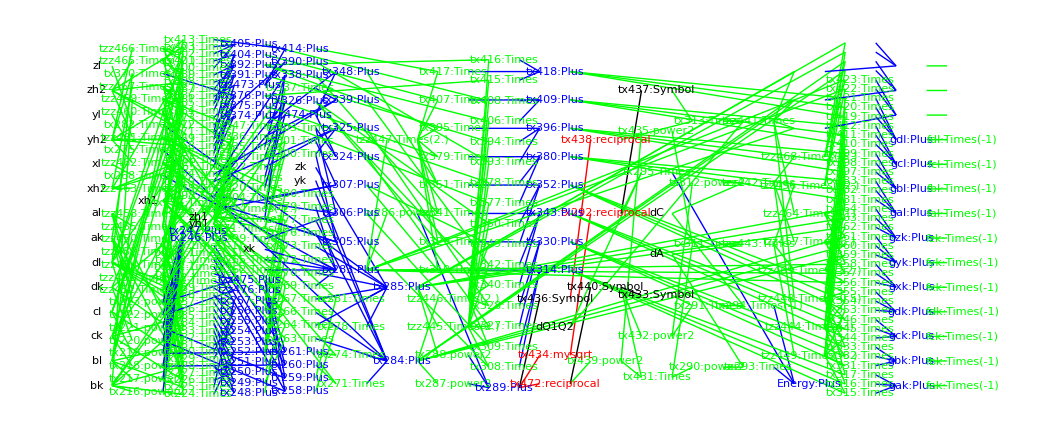

```mathematica
packGraph[nonbondRBPack]
```